# The Student’s Introduction to Mathematica

## A Handbook for Precalculus, Calculus, and Linear Algebra

Bruce F. Torrence, Eve A. Torrence, 2009

## Chapter 1: Getting Started

## 1.3 The First Computation

```mathematica
2+2
```

4

## 1.4 Commands for Basic Arithmetic

```mathematica
17+1
```

18

```mathematica
17-1
```

16

```mathematica
123456789*123456789
```

15241578750190521

```mathematica
123456789 123456789
```

15241578750190521

```mathematica
123456789^2
```

15241578750190521

```mathematica
9.1/256.127
```

0.0355292

Mathematica provides exact answers where possible:

```mathematica
34/4
```

17/2

## 1.5 Input and Output

There are input cells and output cells. Each input-output pair is grouped with a larger bracket, called grouping brackets.

```mathematica
(1/2)^6
```

1/64

## 1.6 The Basic Math Assistant Palette

Use Basic Math Assistant pallet to type math expressions in the input cell.

```mathematica
17^19
```

239072435685151324847153

```mathematica
17^19
```

239072435685151324847153

```mathematica
(1+x)^8
```

(1+x)^8

```mathematica
50653^(1/3)
```

37

```mathematica
50653^(1/3)
```

37

```mathematica
37^3
```

50653

```mathematica
√50653≤225
```

False

```mathematica
√50653≤226
```

True

```mathematica
√50653==50653^(1/2)
```

True

## 1.7 Decimal In, Decimal Out

Sometimes it’s hard to grasp the magnitude of an exact answer.

```mathematica
17^19/19^17
```

239072435685151324847153/5480386857784802185939

```mathematica
59875^(1/3)
```

5 479^(1/3)

Add decimal point to force Mathematica to provide an approximate answer.

```mathematica
17.0^19/19^17
```

43.6233

```mathematica
59875.0^(1/3)
```

39.1215

```mathematica
17.^19/19^17
```

43.6233

```mathematica
59875.^(1/3)
```

39.1215

```mathematica
30/2
```

15

## 1.8 Use Parentheses to Group Terms

Only use round parentheses for grouping terms.

```mathematica
3*(4+1)
```

15

```mathematica
3*4+1
```

13

```mathematica
(-3)^2
```

9

```mathematica
-3^2
```

-9

```mathematica
(3+1)/2
```

2

```mathematica
3+1/2
```

7/2

```mathematica
(3+1)/2
```

2

```mathematica
3+1/2
```

7/2

```mathematica
25(2+2)
```

100

## 1.9 Three Well-Known Constants

```mathematica
π
```

π

```mathematica
π+0.
```

3.14159

ESC+p+ESC for π, ESC+ee+ESC for ⅇ, ESC+ii+ESC for ⅈ
Also, type Pi for π, E for ⅇ, and I for ⅈ

```mathematica
I^2
```

-1

```mathematica
Log[E]
```

1

```mathematica
Cos[Pi]
```

-1

```mathematica
π^(1/3)
```

π^(1/3)

```mathematica
π^(1/3)
```

π^(1/3)

```mathematica
Pi==π
```

True

## 1.10 Typing Commands in Mathematica

### Numerical approximation

By default, numerical approximation command has six significant digits.

```mathematica
N[π]
```

3.14159

```mathematica
17^30
```

8193465725814765556554001028792218849

```mathematica
N[17^30]
```

8.19347×10^36

```mathematica
N[1/2^50]
```

8.88178×10^-16

You can specify the number of significant digits.

```mathematica
N[17^30,20]
```

8.1934657258147655566×10^36

```mathematica
N[π,500]
```

3.1415926535897932384626433832795028841971693993751058209749445923078164062862089986280348253421170679821480865132823066470938446095505822317253594081284811174502841027019385211055596446229489549303819644288109756659334461284756482337867831652712019091456485669234603486104543266482133936072602491412737245870066063155881748815209209628292540917153643678925903600113305305488204665213841469519415116094330572703657595919530921861173819326117931051185480744623799627495673518857527248912279381830119491

### Trigonometric Functions

```mathematica
Cos[π/4]
```

1/(√2)

```mathematica
Sin[π/12]
```

(-1+√3)/(2 √2)

```mathematica
ArcSin[(-1+√3)/(2 √2)]
```

π/12

```mathematica
Tan[π/12]
```

2-√3

```mathematica
Sec[π/12]
```

√2 (-1+√3)

```mathematica
Csc[π/12]
```

√2 (1+√3)

```mathematica
Sin[45 π/180]
```

1/(√2)

```mathematica
Sin[45°]
```

1/(√2)

```mathematica
Sin[45Degree]
```

1/(√2)

```mathematica
N[π/180]
```

0.0174533

```mathematica
N[°]
```

0.0174533

### Logarithms

Natural logarithm is `Log` function.

```mathematica
Log[ⅇ]
```

1

```mathematica
Log[ⅇ^45]
```

45

```mathematica
N[Log[π],30]
```

1.14472988584940017414342735135

Logarithm with other base is computed as follows.

```mathematica
Log[10,1000]
```

3

```mathematica
Log[2,512]
```

9

```mathematica
2^9
```

512

### Factoring Integers

You can factor any integer as a product of prime numbers.

```mathematica
FactorInteger[4832875]
```

{{5,3},{23,1},{41,2}}

```mathematica
5^3 23 41^2
```

4832875

```mathematica
FactorInteger[4832875]//MatrixForm
```

(5 | 3
23 | 1
41 | 2)

### Factoring and Expanding Polynomials

```mathematica
Factor[t^2-9]
```

(-3+t) (3+t)

```mathematica
Factor[64-128x+48 x^2+144 x^3-292 x^4+288 x^5-171 x^6+61 x^7-12 x^8+x^9]
```

(-2+x)^6 (1+x+x^3)

```mathematica
Expand[(-2+x)^6 (1+x+x^3)]
```

64-128 x+48 x^2+144 x^3-292 x^4+288 x^5-171 x^6+61 x^7-12 x^8+x^9

### Plotting Functions

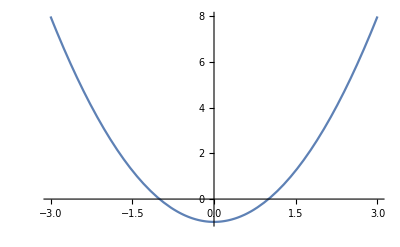

```mathematica
Plot[x^2-1,{x,-3,3}]
```

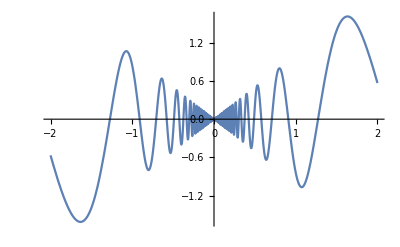

```mathematica
Plot[x Cos[10/x],{x,-2,2}]
```

### Manipulate

```mathematica
Manipulate[x^2-1,{x,-3,3}]
```

```mathematica
Manipulate[Plot[α x Cos[10/x],{x,-2,2},PlotRange->2],{α,-2,2}]
```

### Square Root Function

```mathematica
√144
```

12

```mathematica
Sqrt[144]
```

12

### Real and Imaginary Parts of Complex Numbers

```mathematica
Re[2+3ⅈ]
```

2

```mathematica
Im[2+3ⅈ]
```

3

```mathematica
Re[(2+3ⅈ)^6]
```

2035

### Extracting Digits from a Number

```mathematica
IntegerDigits[2010]
```

{2,0,1,0}

```mathematica
IntegerDigits[2010]//MatrixForm
```

(2
0
1
0)

Lists are ubiquitous in Mathematica. For example, we can add 1 to every member of a list by simply typing this:

```mathematica
1+{2,0,1,0}
```

{3,1,2,1}

```mathematica
1+{2,0,1,0}//MatrixForm
```

(3
1
2
1)

Assemble a list of digits into a number:

```mathematica
FromDigits[{2,0,1,0}]
```

2010

### Programming

```mathematica
FromDigits[1+IntegerDigits[2010]]
```

3121

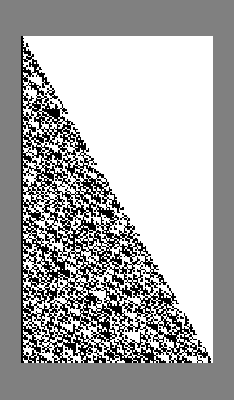

```mathematica
ArrayPlot[NestList[Function[x,IntegerDigits[Floor[3/2 FromDigits[x,2]],2]],{1,0},200],Background->Gray]
```

### Naming Things

Among Greek characters, only π has a built-in value. Other letters can make good names. Start variable names with lowercase letters to avoid confusion with Mathematica reserved name.

```mathematica
θ=π/6
```

π/6

```mathematica
θ
```

π/6

```mathematica
Sin[θ]
```

1/2

```mathematica
Sin[2θ]
```

(√3)/2

```mathematica
Tan[4θ]
```

-√3

It is important to clear an assignment when you are done with it.

```mathematica
Clear[θ]
```

```mathematica
θ
```

θ

```mathematica
p=N[π,40]
```

3.141592653589793238462643383279502884197

```mathematica
p*2^2
```

12.56637061435917295385057353311801153679

```mathematica
Clear[p]
```

```mathematica
distance=540*miles
```

540 miles

```mathematica
time=6*hour
```

6 hour

```mathematica
rate=distance/time
```

(90 miles)/hour

```mathematica
Clear[distance,time,rate]
```

```mathematica
Length[Names["*"]]
```

7022

## Chapter 2: Working with Mathematica

## 2.2 Adding Text to Notebooks

Equation typeset without using an inline cell: f(x)-x=0

Equation typeset with using an inline cell: f(x)-x=0

## 2.8 Tips for Working Effectively

```mathematica
23^20/20^21
```

1716155831334586342923895201/2097152000000000000000000000

```mathematica
N[%]
```

0.818327

```mathematica
Sin[π/12]//N
```

0.258819

```mathematica
(x-1)(2+3x)(6-x)//Expand
```

-12-4 x+19 x^2-3 x^3

```mathematica
First@{2,4,6,8}
```

2

```mathematica
TraditionalForm@(Sin[x]^2)
```

sin^2(x)

Suppressing output:

```mathematica
x=π/12
```

π/12

```mathematica
x=π/12;
```

```mathematica
x=3;
Expand[(x-y)^8]
```

6561-17496 y+20412 y^2-13608 y^3+5670 y^4-1512 y^5+252 y^6-24 y^7+y^8

```mathematica
Clear[x];Expand[(x-y)^8]
```

x^8-8 x^7 y+28 x^6 y^2-56 x^5 y^3+70 x^4 y^4-56 x^3 y^5+28 x^2 y^6-8 x y^7+y^8

```mathematica
1000!//Short
```

4023872600770937735437024339230039857193«2488»0000000000000000000000000000000000000000

```mathematica
20!//Timing
```

{0.00007,2432902008176640000}

```mathematica
1000000!;//Timing
```

{0.829019,Null}

## 2.9 Getting Help from Mathematica

```mathematica
?N
```

## 2.10 Loading Packages

Load external packages from this website:
https://library.wolfram.com/infocenter/MathSource/AppliedMathematics/ComputerScience/

List standard packages of Mathematica:

```mathematica
SetDirectory[$InstallationDirectory];
SetDirectory["AddOns"];
SetDirectory["Packages"];
FileNames[]
```

{ANOVA,Audio,BarCharts,Benchmarking,BlackBodyRadiation,Calendar,Combinatorica,ComputationalGeometry,ComputerArithmetic,Developer,EquationTrekker,ErrorBarPlots,Experimental,FiniteFields,FourierSeries,FunctionApproximations,Geodesy,GraphUtilities,GUIKit,HierarchicalClustering,Histograms,HypothesisTesting,LinearRegression,MultivariateStatistics,Music,NonlinearRegression,Notation,NumericalCalculus,NumericalDifferentialEquationAnalysis,PhysicalConstants,PieCharts,PlotLegends,PolyhedronOperations,Polytopes,PrimalityProving,Quaternions,RegressionCommon,ResonanceAbsorptionLines,Splines,StandardAtmosphere,StatisticalPlots,Units,VariationalMethods,VectorAnalysis,VectorFieldPlots,WorldPlot,XML}

To use a particular package use this command:

```mathematica
Needs["Units`"]
```

```mathematica
$Packages
```

{Units`,DocumentationSearch`,ProcessLink`,EntityFramework`WolframAlphaEntityStore`,EntityFramework`Utilities`,EntityFramework`ToFromEntity`,EntityFramework`Registry`,EntityFramework`Prefetch`,EntityFramework`Preferences`,EntityFramework`Predicates`,EntityFramework`OperatorForms`,EntityFramework`InterpreterCache`,EntityFramework`Formatting`,EntityFramework`Filter`,EntityFramework`FileKeyValueStore`,EntityFramework`EntityValue`,EntityFramework`EntityStore`,EntityFramework`EntityList`,EntityFramework`EntityFunctions`,EntityFramework`EntityFunction`,EntityFramework`DefaultEntityTypes`,EntityFramework`DataUtilities`,EntityFramework`DataFunctions`,EntityFramework`CustomEntity`,EntityFramework`Caching`,EntityFramework`BatchApplied`,EntityFramework`,CURLLink`URLResponseTime`,CURLLink`Utilities`,CURLInfo`,CURLLink`Cookies`,CURLLink`HTTP`,OAuthSigning`,CURLLink`URLFetch`,CURLLink`,Macros`,DocumentationSearch`Skeletonizer`,JLink`,GetFEKernelInit`,UnsupportedMessages`,RemoteEvaluate`,JSONTools`,URLUtilities`,KeychainLink`,ResourceFunctionHelpers`,UnitTable`,CloudObject`CreateUUID`,CloudObjectLoader`,NaturalLanguage`,WolframCGL`,WebAudioSearchLoader`,Templating`,NeuralNetworks`,NeuralFunctions`,MobileMessaging`,Interpreter`,IntegratedServices`,IconizeLoader`,HTTPHandling`,GeoTools`,GeometrySearchLoader`,Forms`,FormNotebook`,ExternalEvaluate`,Cryptography`,Blockchain`,Authentication`,SystemTools`,SecureShellLink`,MailLink`,IMAPLink`,ExternalStorage`,CloudDialogs`,WolframAppCatalog`,ResourceLocator`,PacletManager`,PersistenceLocations`,System`,Global`}

```mathematica
Convert[LightYear,Mile]
```

5.87863×10^12 Mile

```mathematica
Convert[16Gallon,Teaspoon]
```

12288. Teaspoon

```mathematica
Convert[1.75Liter,Jigger]
```

39.4497 Jigger

```mathematica
Convert[90Mile/Hour,Foot/Second]
```

(132 Foot)/Second

```mathematica
Names["Units`*"]//Short
```

{Abampere,Abcoulomb,Abfarad,Abhenry,«268»,Yocto,Yotta,Zepto,Zetta}

```mathematica
Take[Names["Units`*"],40;;70]
```

{BTU,Bucket,Bushel,Butt,Cable,Caliber,Calorie,Candela,Candle,Carat,Celsius,Cental,Centi,Centigrade,Centimeter,Century,CGS,Chain,ChevalVapeur,Cicero,Convert,ConvertTemperature,Cord,Coulomb,Cubit,Curie,Dalton,Day,Deca,Decade,Deci}

```mathematica
?Butt
```

```mathematica
?ConvertTemperature
```

```mathematica
ConvertTemperature[212,Fahrenheit,Celsius]
```

100

```mathematica
Convert[Butt,Gallon]
```

126. Gallon

## Chapter 3: Functions and Their Graphs

## 3.1 Defining a Function

```mathematica
Log[1]
```

0

```mathematica
f[x_]:=x^2+2x-4
```

```mathematica
f[1]
```

-1

```mathematica
f[π]
```

-4+2 π+π^2

```mathematica
inv[x_]:=1/x
```

```mathematica
inv[45]
```

1/45

```mathematica
g[x_]:=N[inv[x]]
```

```mathematica
g[45]
```

0.0222222

Why we use SetDelayed instead of Set operator when defining a function? Look in Immediate and Delayed Definitions tutorial in the Documentation.

```mathematica
x=RandomInteger[100];{x,x,x}
```

{75,75,75}

```mathematica
x:=RandomInteger[100];{x,x,x}
```

{76,29,100}

```mathematica
?f
```

```mathematica
Clear[f]
```

```mathematica
?f
```

Clear all user-defined symbols:

```mathematica
Clear["Global`*"]
```

## 3.2 Plotting a Function

```mathematica
Clear[f];
f[x_]:=x^2-2x+4
```

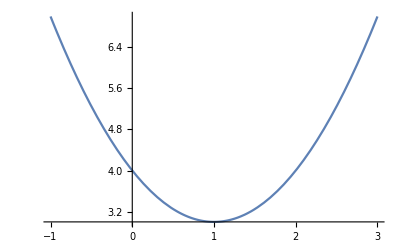

```mathematica
Plot[f[x],{x,-1,3}]
```

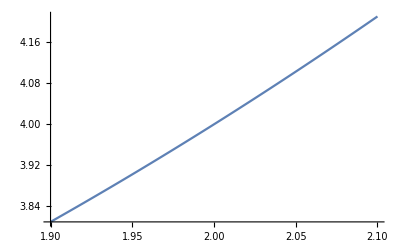

```mathematica
Plot[f[x],{x,1.9,2.1}]
```

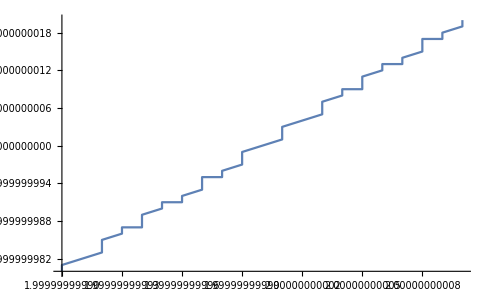

```mathematica
With[{δ=10^-10},Plot[f[x],{x,2-δ,2+δ}]]
```

The command With does not store delta after the execution of internal code.

```mathematica
δ
```

δ

```mathematica
Clear[f];
f[x_]:=(x^5-4 x^2+1)/(x-1/2)
```

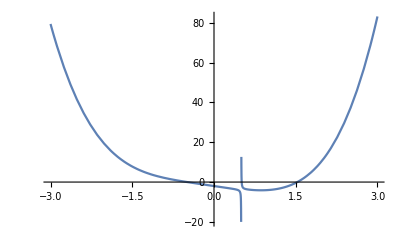

```mathematica
Plot[f[x],{x,-3,3}]
```

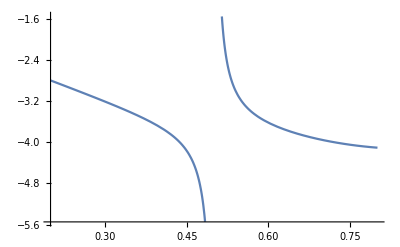

```mathematica
With[{δ=0.3},Plot[f[x],{x,1/2-δ,1/2+δ}]]
```

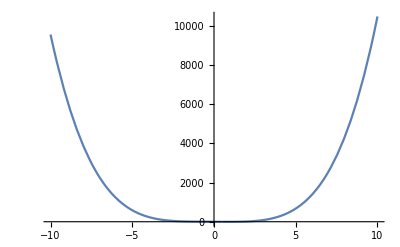

```mathematica
Plot[f[x],{x,-10,10}]
```

Mathematica has difficulty in plotting real-valued functions with negative roots:

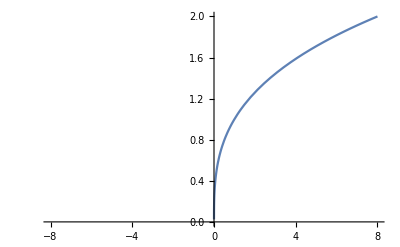

```mathematica
Plot[x^(1/3),{x,-8,8}]
```

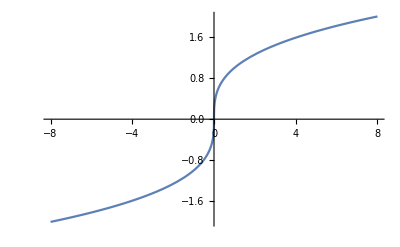

```mathematica
Plot[CubeRoot[x],{x,-8,8}]
```

Or pressing ESC cbrt ESC

```mathematica
Plot[x^(1/3),{x,-8,8}]
```

-Graphics-

```mathematica
Plot[Surd[x,3],{x,-8,8}]
```

-Graphics-

Or alternatively, press ESC surd ESC

```mathematica
Plot[x^(1/3),{x,-8,8}]
```

-Graphics-

### Exercises

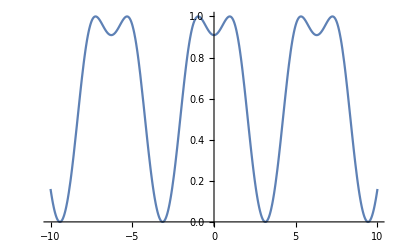

```mathematica
Plot[Sin[1+Cos[x]],{x,-10,10}]
```

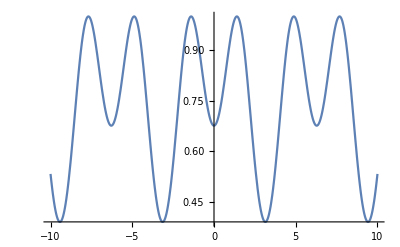

```mathematica
Plot[Sin[1.4+Cos[x]],{x,-10,10}]
```

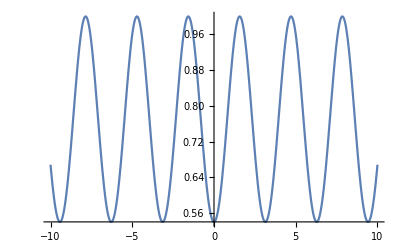

```mathematica
Plot[Sin[π/2+Cos[x]],{x,-10,10}]
```

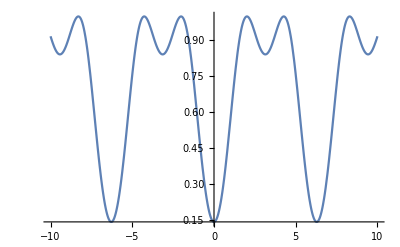

```mathematica
Plot[Sin[2+Cos[x]],{x,-10,10}]
```

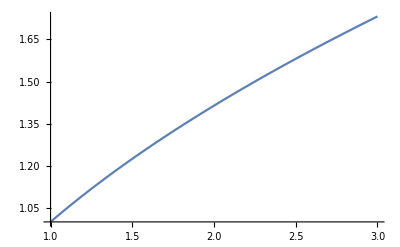

```mathematica
With[{δ=10^0},Plot[√x,{x,2-δ,2+δ}]]
```

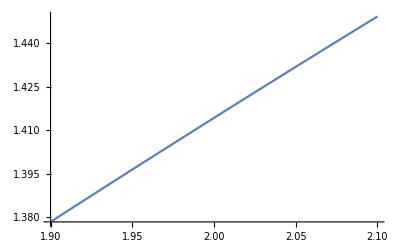

```mathematica
With[{δ=10^-1},Plot[√x,{x,2-δ,2+δ}]]
```

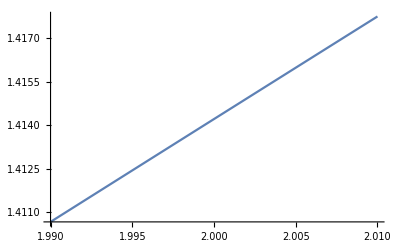

```mathematica
With[{δ=10^-2},Plot[√x,{x,2-δ,2+δ}]]
```

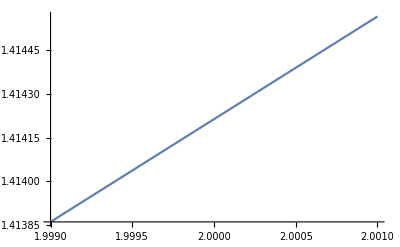

```mathematica
With[{δ=10^-3},Plot[√x,{x,2-δ,2+δ}]]
```

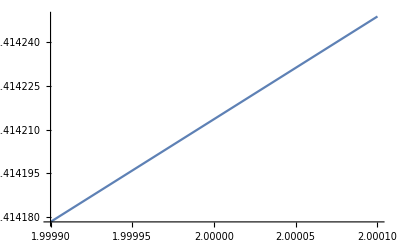

```mathematica
With[{δ=10^-4},Plot[√x,{x,2-δ,2+δ}]]
```

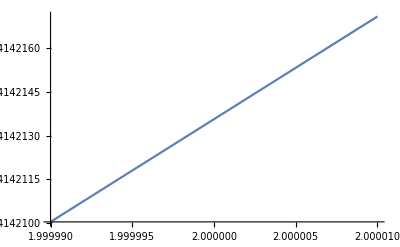

```mathematica
With[{δ=10^-5},Plot[√x,{x,2-δ,2+δ}]]
```

```mathematica
√2//N
```

1.41421

```mathematica
With[{δ=10^-20},Plot[√x,{x,2-δ,2+δ}]]
```

Plot::plld: Endpoints for x in {x,199999999999999999999/100000000000000000000,200000000000000000001/100000000000000000000} must have distinct machine-precision numerical values.

Plot[√x,{x,2-1/100000000000000000000,2+1/100000000000000000000}]

```mathematica
f[x_]:=(x^(1/5))^4;
```

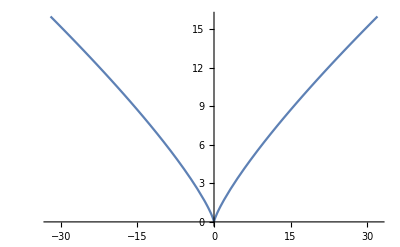

```mathematica
Plot[f[x],{x,-32,32}]
```

```mathematica
f[32]
```

16

## 3.3 Using Mathematica’s Plot Options

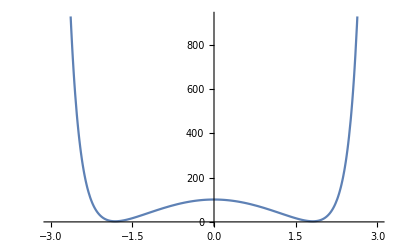

```mathematica
Plot[100 Cos[x]+ⅇ^(x^2),{x,-3,3}]
```

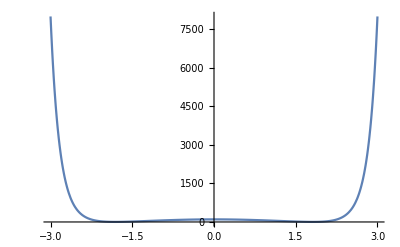

```mathematica
Plot[100 Cos[x]+ⅇ^(x^2),{x,-3,3},PlotRange->Full]
```

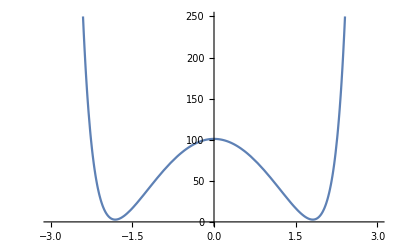

```mathematica
Plot[100 Cos[x]+ⅇ^(x^2),{x,-3,3},PlotRange->{0,250}]
```

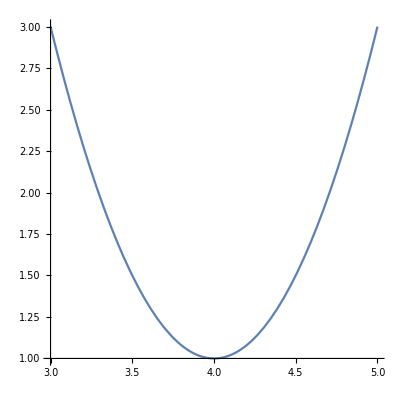

```mathematica
Plot[2(x-4)^2+1,{x,3,5},AspectRatio->Automatic]
```

Height to width ratio of 9/16:

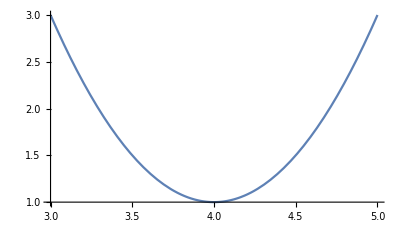

```mathematica
Plot[2(x-4)^2+1,{x,3,5},AspectRatio->9/16]
```

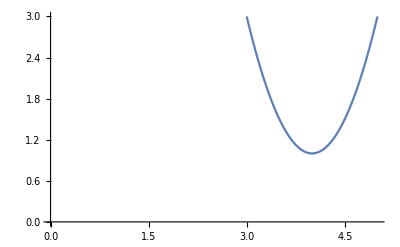

```mathematica
Plot[2(x-4)^2+1,{x,3,5},AxesOrigin->{0,0}]
```

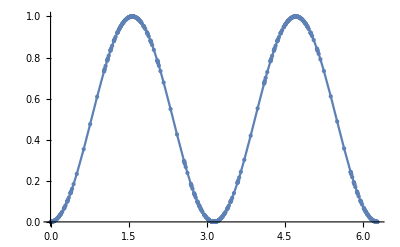

```mathematica
Plot[Sin[x]^2,{x,0,2π},Mesh->All]
```

Regularly spaced points:

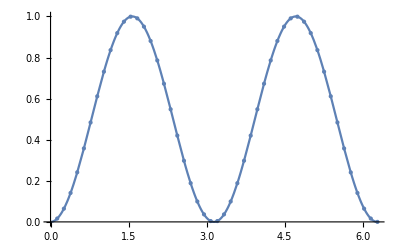

```mathematica
Plot[Sin[x]^2,{x,0,2π},Mesh->Full]
```

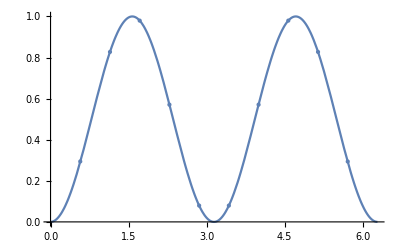

```mathematica
Plot[Sin[x]^2,{x,0,2π},Mesh->10]
```

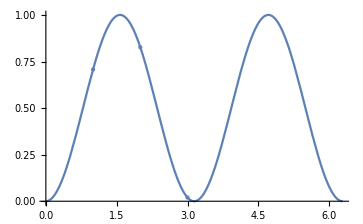

```mathematica
Plot[Sin[x]^2,{x,0,2π},Mesh->{{1,2,3}}]
```

Mesh values is a list of x coordinates:

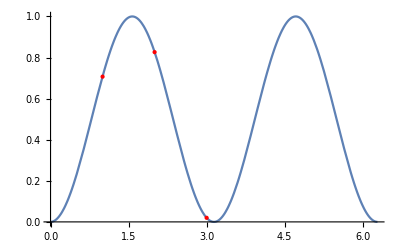

```mathematica
Plot[Sin[x]^2,{x,0,2π},MeshFunctions->{#1&},Mesh->{{1,2,3}},MeshStyle->Red]
```

Mesh values is a list of y coordinates:

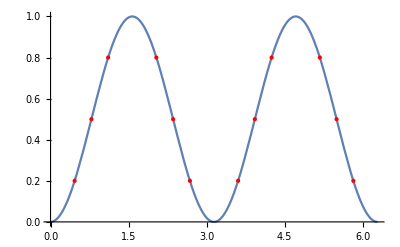

```mathematica
Plot[Sin[x]^2,{x,0,2π},MeshFunctions->{#2&},Mesh->{{0.2,0.5,0.8}},MeshStyle->Red]
```

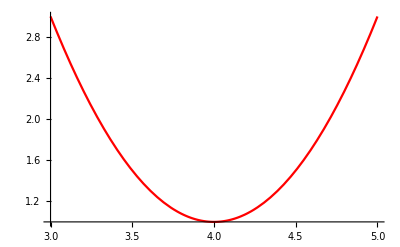

```mathematica
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Red]
```

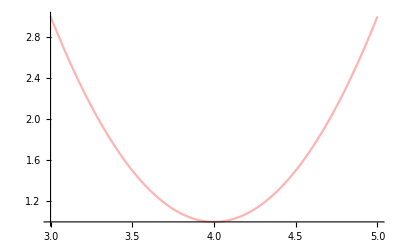

```mathematica
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Lighter[Red,.7]]
```

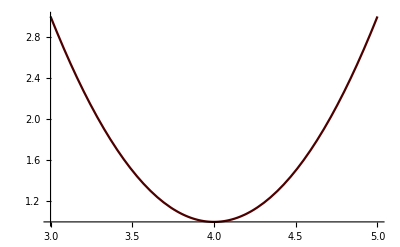

```mathematica
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Darker[Red,.7]]
```

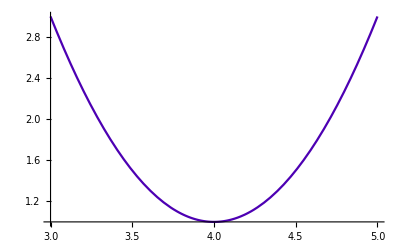

```mathematica
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Blend[{Blue,Red},.3]]
```

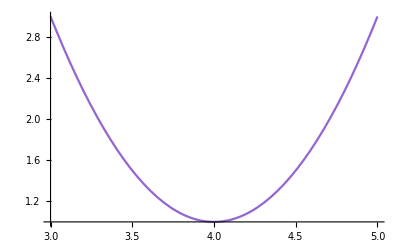

```mathematica
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Lighter[Blend[{Blue,Red},.3],.4]]
```

Multiple PlotStyle options are done by using Directive:

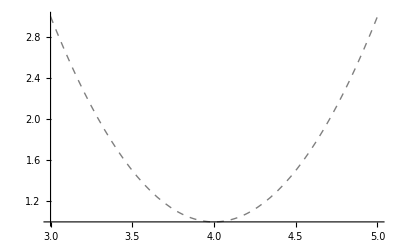

```mathematica
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Directive[Thick,Gray,Dashed]]
```

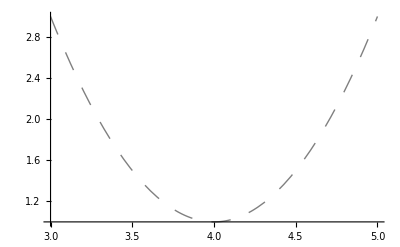

```mathematica
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Directive[Thick,Gray,Dashing[Large]]]
```

Break the plot into dashed segments each of which is 2% of the width of the entire graphic with spaces between consecutive dashes to be 1% of the width of the graphic.

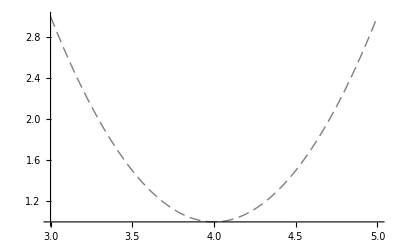

```mathematica
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Directive[Thick,Gray,Dashing[{.02,.01}]]]
```

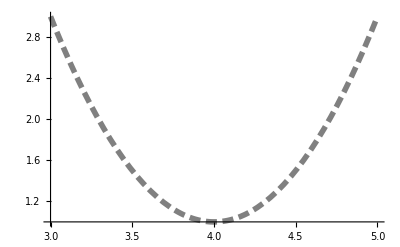

```mathematica
Plot[2(x-4)^2+1,{x,3,5},PlotStyle->Directive[Thickness[.01],Gray,Dashing[{.02,.01}]]]
```

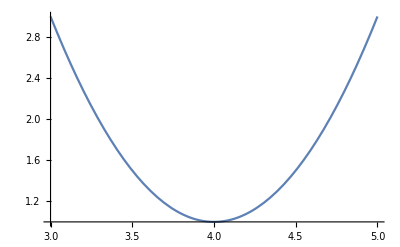

```mathematica
Plot[2(x-4)^2+1,{x,3,5},AxesStyle->{Directive[Red,12],Blue}]
```

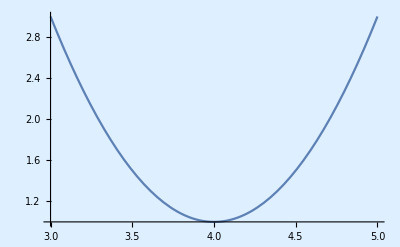

```mathematica
Plot[2(x-4)^2+1,{x,3,5},Background->LightBlue]
```

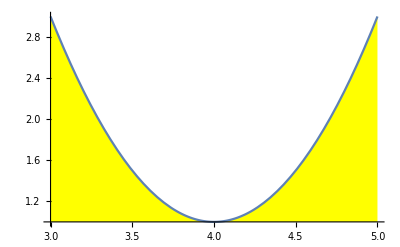

```mathematica
Plot[2(x-4)^2+1,{x,3,5},Filling->Axis,FillingStyle->Yellow]
```

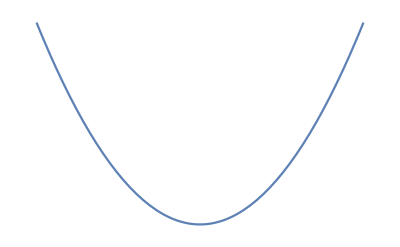

```mathematica
Plot[2(x-4)^2+1,{x,3,5},Axes->False]
```

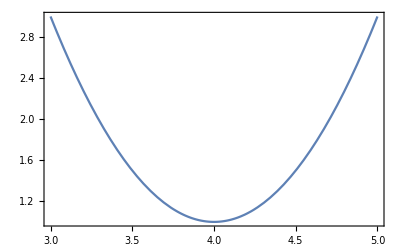

```mathematica
Plot[2(x-4)^2+1,{x,3,5},Frame->True]
```

```mathematica
Plot[2(x-4)^2+1,{x,3,5},AxesStyle->Arrowheads[0.05]]
```

-Graphics-

```mathematica
Plot[2(x-4)^2+1,{x,3,5},AxesStyle->Arrowheads[{-0.05,0.05}]]
```

-Graphics-

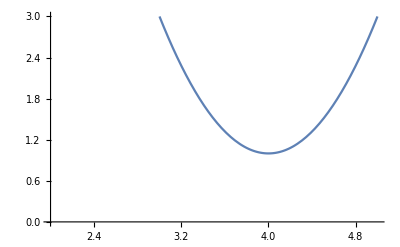

```mathematica
Plot[2(x-4)^2+1,{x,3,5},AxesStyle->Arrowheads[.05],AxesOrigin->{2,0}]
```

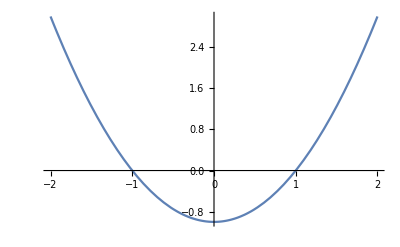

```mathematica
Plot[x^2-1,{x,-2,2},AxesStyle->Arrowheads[{-.05,.05}]]
```

Increase PlotRange to place arrowheads farther from the center:

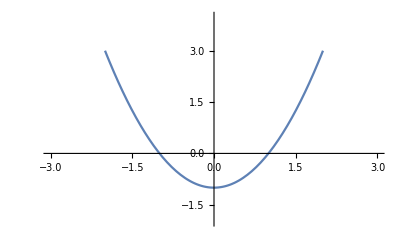

```mathematica
Plot[x^2-1,{x,-2,2},AxesStyle->Arrowheads[{-.05,.05}],PlotRange->{{-3,3},{-2,4}}]
```

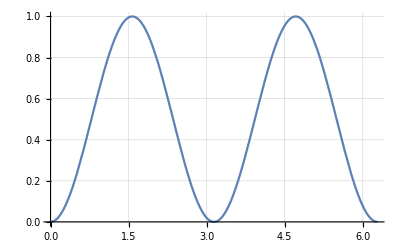

```mathematica
Plot[Sin[x]^2,{x,0,2π},GridLines->Automatic]
```

```mathematica
Plot[Sin[x]^2,{x,0,2π},GridLines->Automatic,GridLinesStyle->Directive[Thin,Gray,Dotted]]
```

-Graphics-

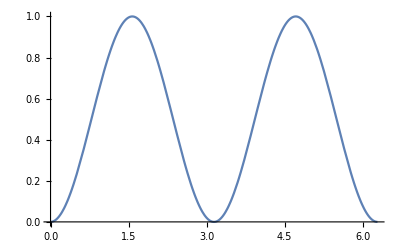

```mathematica
Plot[Sin[x]^2,{x,0,2π},GridLines->{{π/2,π,3 π/2,2π},{.2,.4,.6,.8,1}}]
```

```mathematica
Range[0,1,.1]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
Plot[Sin[x]^2,{x,0,2π}, GridLinesStyle->Lighter[Green,.8],GridLines->{Range[0,2π,π/8],Range[0,1,.1]}]
```

-Graphics-

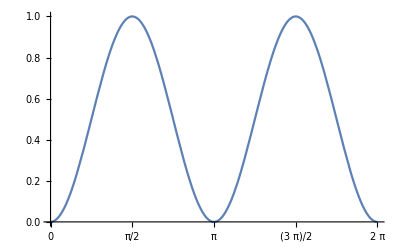

```mathematica
Plot[Sin[x]^2,{x,0,2π},GridLines->{Range[0,2π,π/8],Range[0,1,.1]},Ticks->{Range[0,2π,π/2],Automatic}]
```

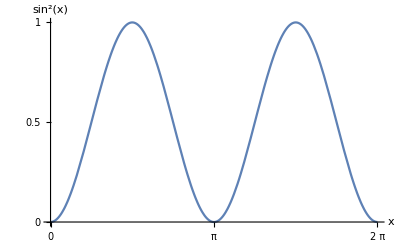

```mathematica
Plot[Sin[x]^2,{x,0,2π},Ticks->{{0,π,2π},{0,.5,1}},AxesLabel->{x,Sin[x]^2}]
```

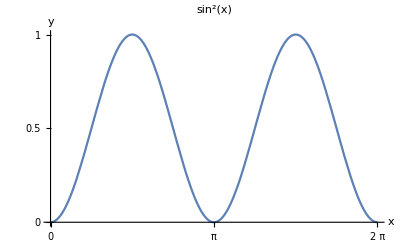

```mathematica
Plot[Sin[x]^2,{x,0,2π},Ticks->{{0,π,2π},{0,.5,1}},AxesLabel->{x,y},PlotLabel->Sin[x]^2]
```

Labels with “=” sign or more than one word should be entered as a String:

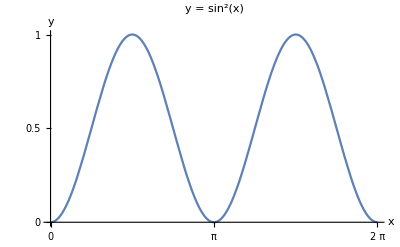

```mathematica
Plot[Sin[x]^2,{x,0,2π},Ticks->{{0,π,2π},{0,.5,1}},AxesLabel->{x,y},PlotLabel->"y = sin^2(x)"]
```

An alternative to labelling for any expression:

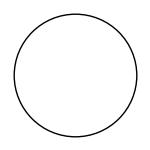
-Graphics-a circle

```mathematica
g=Graphics[Circle[],ImageSize->150];
Labeled[g,Text["a circle"]]
Clear[g]
```

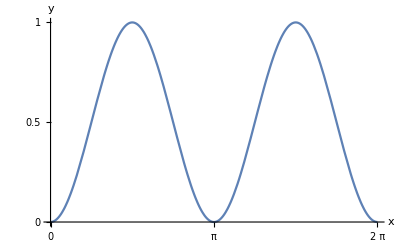
-Graphics-y = sin^2(x)

```mathematica
p=Plot[Sin[x]^2,{x,0,2π},Ticks->{{0,π,2π},{0,.5,1}},AxesLabel->{x,y}];
Labeled[p,Text["y = sin^2(x)"],Right]
```

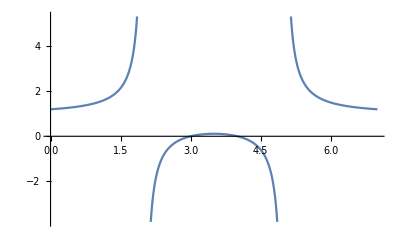

```mathematica
Plot[((x-3)(x-4))/((x-2)(x-5)),{x,0,7}]
```

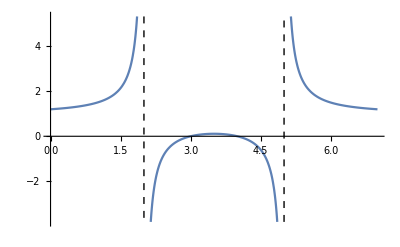

```mathematica
Plot[((x-3)(x-4))/((x-2)(x-5)),{x,0,7},Exclusions->{x==2,x==5},ExclusionsStyle->Dashed]
```

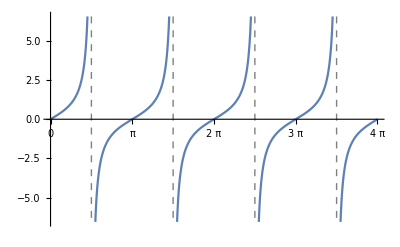

```mathematica
Plot[Tan[x],{x,0,4π},Exclusions->{Cos[x]==0},ExclusionsStyle->Directive[Gray,Dashed],Ticks->{Range[0,4π,π/2],Automatic}]
```

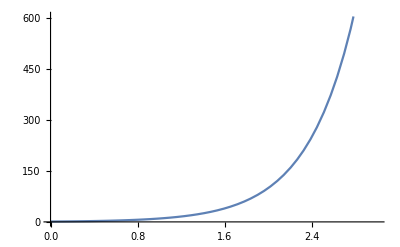

```mathematica
Plot[10^x,{x,0,3}]
```

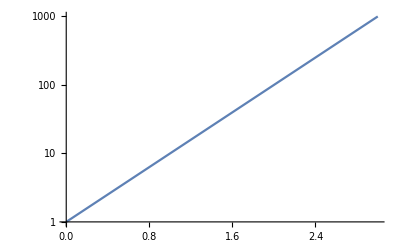

```mathematica
LogPlot[10^x,{x,0,3}]
```

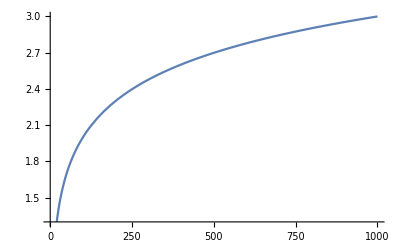

```mathematica
Plot[Log[10,x],{x,1,1000}]
```

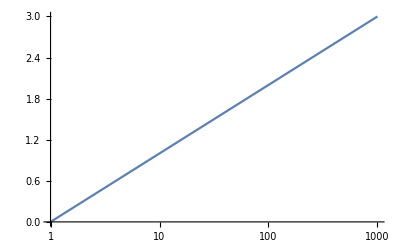

```mathematica
LogLinearPlot[Log[10,x],{x,1,1000}]
```

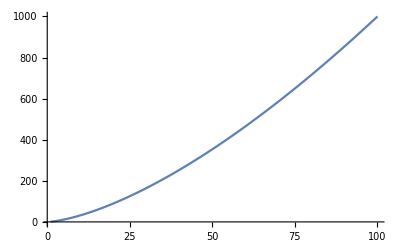

```mathematica
Plot[x^(3/2),{x,1,100}]
```

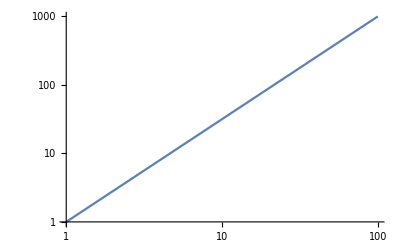

```mathematica
LogLogPlot[x^(3/2),{x,1,100}]
```

### Exercises

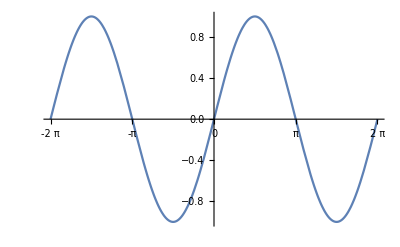

```mathematica
Plot[Sin[x],{x,-2π,2π},GridLines->{Range[-2π,2π,π/4],Range[-1,1,.2]},GridLinesStyle->Lighter[Gray],Ticks->{Range[-2π,2π,π],Automatic}]
```

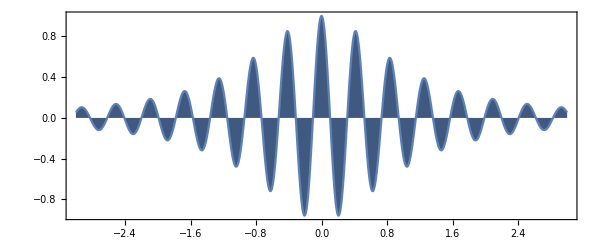

```mathematica
Plot[Cos[15x]/(1+x^2),{x,-3,3},Axes->{True,False},Frame->{{True,False},{True,False}},FrameStyle->GrayLevel[.5],Filling->Axis,FillingStyle->Hue[.6,.5,.5],PlotRange->All,AspectRatio->Automatic]
```

```mathematica
RGBColor[.2,.8,.8]
```

RGBColor[0.2, 0.8, 0.8]

```mathematica
Hue[.6,.5,.5]
```

Hue[0.6, 0.5, 0.5]

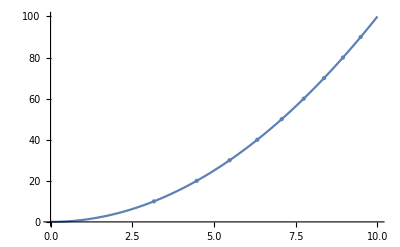

```mathematica
Plot[x^2,{x,0,10},Mesh->9,MeshFunctions->{#2&},GridLines->{√Range[0,100,10],Range[0,100,10]}]
```

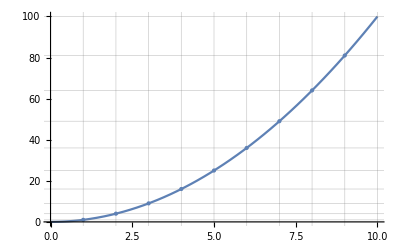

```mathematica
Plot[x^2,{x,0,10},Mesh->9,MeshFunctions->{#1&},GridLines->{Range[0,10,1],(Range[0,10,1])^2}]
```

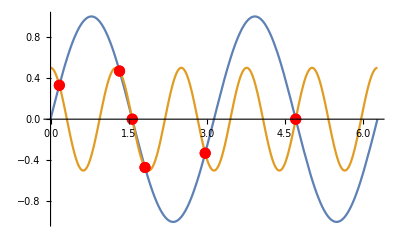

```mathematica
Plot[{Sin[2x],1/2 Cos[5x]},{x,0,2π},Mesh->{{0}},MeshFunctions->{Sin[2#1]-1/2 Cos[5#1]&},MeshStyle->Directive[PointSize[0.02],Red]]
```

## 3.4 Investigating Functions with Manipulate

```mathematica
Manipulate[x^2,{x,1,10}]
```

```mathematica
Manipulate[x^2,{x,1,50,5}]
```

```mathematica
Manipulate[Plot[x Sin[1/x],{x,0,r}],{r,.1,2}]
```

```mathematica
Manipulate[Plot[x Sin[1/x],{x,0,r}],{{r,.2,"right endpoint"},10^-10,2}]
```

```mathematica
Manipulate[Plot[x Sin[x],{x,-10,10},PlotStyle->Directive[Thickness[t],Dashing[{d}],Blend[{Red,Blue},b]]],{{t,.01,"Thickness"},.001,.02},{{d,.02,"Dash Size"},0,.04},{{b,.5,"Percent Blue"},0,1}]
```

```mathematica
Manipulate[Plot[α(x-b)^2+c,{x,-5,5},PlotRange->5,PlotLabel->"y=α(x-b)^2+c"],
{α,-1,1},{{b,-1},-3,3},{{c,2},-3,3}]
```

```mathematica
Manipulate[
Plot[Sin[4/x],{x,-2π,2π},PlotPoints->pp,MaxRecursion->mr,Mesh->m],
{{pp,64,"PlotPoints"},{4,8,16,32,64}},
{{mr,4,"MaxRecursion"},{0,1,2,3,4}},{{m,Full,"Mesh"},{Full,All,None}}]
```

Force SetterBar option to display choices as a buttons rather than in a dropdown menu:

```mathematica
Manipulate[
Plot[f[x],{x,0,4π},Ticks->{Range[0,4π,π/2],Automatic},PlotLabel->f[x]],
{{f,Tan,"function"},{Sin,Cos,Sec,Csc,Tan,Cot},ControlType->SetterBar}]
```

```mathematica
Manipulate[
Plot[x Sin[x],{x,-20,20},AxesOrigin->pt,PlotRange->20],
{{pt,{0,0},"Move the axes: "},{-20,-20},{20,20}},ControlPlacement->Left]
```

```mathematica
Manipulate[
Plot[x Sin[x],{x,-20,20},AxesOrigin->pt,PlotRange->20],
{{pt,{0,0}},Locator}]
```

```mathematica
Manipulate[
Plot[Sin[x]/x,{x,0,20},PlotStyle->color],
{color,Blue}]
```

```mathematica
Animate[Plot[Sin[x+a],{x,0,10}],{a,0,5}]
```

```mathematica
OpenerView[{Style["click the triangle","Text"],Style["Huh,you did it!","Section"]}]
```

```mathematica
ListAnimate[Table[Plot[Sin[n x],{x,0,10}],{n,5}]]
```

```mathematica
FlipView[Table[Plot[Sin[n x],{x,0,10}],{n,5}]]
```

```mathematica
PopupView[Table[Plot[BesselJ[n,x],{x,0,10}],{n,5}]]
```

```mathematica
SlideView[Table[ContourPlot[y^2==x^3+i x,{x,-3,3},{y,-3,3}],{i,-2,2}]]
```

```mathematica
TabView[{"sine"->Plot[Sin[x],{x,0,2π}],"cosine"->Plot[Cos[x],{x,0,2π}]},ImageSize->Automatic]
```

12

### Excercises

```mathematica
Manipulate[pt,{{pt,{0,0},"(x,y): "},{0,0},{1,1}}]
```

```mathematica
Manipulate[pt,"XY1"->{pt,{-1,-1},{1,1}}]
```

```mathematica
Manipulate[
Plot[Sin[x],{x,0,2π},AspectRatio->ar,ImageSize->{Automatic,128}],
{{ar,1,"Aspect ratio"},1/5,5}]
```

```mathematica
Manipulate[
Plot[Sin[x],{x,0,2π},Background->RGBColor[r,g,b]],
{{r,0.66,"Red"},0,1},
{{g,0.82,"Green"},0,1},
{{b,0.64,"Blue"},0,1}]
```

```mathematica
Manipulate[
Plot[Sin[x],{x,0,2π},Background->Hue[h,s,b]],
{{h,0.11,"Hue"},0,1},
{{s,0.24,"Saturation"},0,1},
{{b,0.90,"Brightness"},0,1}]
```

```mathematica
"This is a string"~~" and so is this."//FullForm
```

"This is a string and so is this."

```mathematica
Manipulate[Style["The square root of "~~ToString[x]~~" is "~~ToString[N[√x]]~~".","Subsubsection"],{{x,2},1,10}]
```

```mathematica
Manipulate[
Plot[Sin[x],{x,-π,π},Epilog->{PointSize[Medium],Red,Point[{k,Sin[k]}]},PlotLabel->"sin("~~ToString[k]~~")="~~ToString[N[Sin[k]]]],
{{k,0,"x"},-π,π}]
```

```mathematica
gaussian2D[x_,y_,s_,a_,b_]:=1/(2π s^2)ⅇ^(-((x-a)^2+(y-b)^2)/(2 s^2));
Manipulate[
Plot3D[gaussian2D[x,y,s,a,b],{x,-3,3},{y,-3,3},PlotRange->Full,AxesLabel->Automatic],
{{s,1,"standard deviation"},0.5,10},
{{a,0,"x_0"},-1,1},
{{b,0,"y_0"},-1,1}]
```

```mathematica
Manipulate[
Plot3D[gaussian2D[x,y,s,o[[1]],o[[2]]],{x,-3,3},{y,-3,3},PlotRange->Full,AxesLabel->Automatic],
{{s,1,"standard deviation"},0.5,3},
{{o,{0,0},"(x_0,y_0)"},{-3,-3},{3,3}},ControlPlacement->Left]
```

```mathematica
Clear[gaussian2D]
```

```mathematica
ListPointPlot3D[Table[gaussian2D[x,y,1,0,0],{x,-3,3,.3},{y,-3,3,.3}],Filling->Bottom,PlotRange->Full]
```

-Graphics3D-

```mathematica
Manipulate[
ListPointPlot3D[Table[gaussian2D[x,y,s,o[[1]],o[[2]]],{x,-3,3,.3},{y,-3,3,.3}],Filling->Bottom,PlotRange->Full,AxesLabel->{y,x,z}],
{{s,1,"standard deviation"},0.5,3},
{{o,{0,0},"(x_0,y_0)"},{-3,-3},{3,3}},ControlPlacement->Left]
```

```mathematica
Clear[gaussian2D]
```

```mathematica
Manipulate[
ToExpression[SymbolName[option]~~"::usage"],
{option,Map[First,Options[Plot]]}]
```

```mathematica
Manipulate[
ToExpression[SymbolName[option]~~"::usage"],
{option,Map[First,Options[Grid]]}]
```

```mathematica
TabView[{"Riddle"->Style["I'm a wave that does not move, and to you I want to prove, that if you knock I'm hard as rock and if you kick me I'll stick to your sock.",Italic, "Text"],
"Answer"->Style["\t\t Ice!","Section"]}]
```

12

## 3.5 Producing a Table of Values

```mathematica
f[x_]:=x^2;
Table[f[x],{x,1,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[f[x],{x,0,50,5}]
```

{0,25,100,225,400,625,900,1225,1600,2025,2500}

```mathematica
Table[f[x],{x,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[f[x],{x,{1,7,12,20}}]
```

{1,49,144,400}

```mathematica
data=Table[{x,f[x]},{x,5}]
```

{{1,1},{2,4},{3,9},{4,16},{5,25}}

```mathematica
Grid[data]
```

1 | 1
2 | 4
3 | 9
4 | 16
5 | 25

```mathematica
Text@Grid[data,Alignment->Right]
```

1 | 1
2 | 4
3 | 9
4 | 16
5 | 25

Add headings to the columns of a table by prepending an additional row:

```mathematica
tableContents=Prepend[data,{"x","x^2"}]
```

{{x,x^2},{1,1},{2,4},{3,9},{4,16},{5,25}}

Center vertical dividers, no top horizontal divider, one horizontal divider after the first line:

```mathematica
Text@Grid[tableContents,Alignment->Right,Dividers->{Center,{False,True}},Spacings->2]
```

x | x^2
1 | 1
2 | 4
3 | 9
4 | 16
5 | 25

Render only the second vertical divider and the second horizontal divider:

```mathematica
Text@Grid[tableContents,Alignment->Right,Dividers->{2->True,2->True},Spacings->2]
```

x | x^2
1 | 1
2 | 4
3 | 9
4 | 16
5 | 25

```mathematica
Clear[data];
data=Table[{10^n,f[10^n]},{n,0,5}]
```

{{1,1},{10,100},{100,10000},{1000,1000000},{10000,100000000},{100000,10000000000}}

```mathematica
Text@Grid[Prepend[data,{"x","x^2"}],Alignment->Right,Dividers->All,Spacings->2]
```

x | x^2
1 | 1
10 | 100
100 | 10000
1000 | 1000000
10000 | 100000000
100000 | 10000000000

```mathematica
Clear[data];
data=Table[{x,x^2,2^x},{x,10}]
```

{{1,1,2},{2,4,4},{3,9,8},{4,16,16},{5,25,32},{6,36,64},{7,49,128},{8,64,256},{9,81,512},{10,100,1024}}

```mathematica
Text@Grid[Prepend[data,{"x","x^2","2^x"}],
Alignment->Right,Dividers->{Center,{False,True}},Spacings->2]
```

x | x^2 | 2^x
1 | 1 | 2
2 | 4 | 4
3 | 9 | 8
4 | 16 | 16
5 | 25 | 32
6 | 36 | 64
7 | 49 | 128
8 | 64 | 256
9 | 81 | 512
10 | 100 | 1024

```mathematica
Manipulate[
Text@Grid[{{"x","x^2"},{x,x^2}},Dividers->All,ItemSize->5],{{x,5.3},1,10,.1}]
```

```mathematica
Manipulate[
Text@Grid[{{"C","F"},{c,1.8c+32}},Dividers->All,ItemSize->5],
{{c,0},-40,100,1}]
```

### Exercises

```mathematica
Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
Partition[Range[100],10]
```

{{1,2,3,4,5,6,7,8,9,10},{11,12,13,14,15,16,17,18,19,20},{21,22,23,24,25,26,27,28,29,30},{31,32,33,34,35,36,37,38,39,40},{41,42,43,44,45,46,47,48,49,50},{51,52,53,54,55,56,57,58,59,60},{61,62,63,64,65,66,67,68,69,70},{71,72,73,74,75,76,77,78,79,80},{81,82,83,84,85,86,87,88,89,90},{91,92,93,94,95,96,97,98,99,100}}

```mathematica
Text@Grid@Partition[Range[100],20]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100

```mathematica
Text@Grid@Table@Range[Range[1,81,20],Range[20,100,20]]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100

```mathematica
Text@Grid@Table[Range[n,n+19],{n,1,81,20}]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100

```mathematica
{Style[4,Red],Style[4,72],Style[4,"Title"],Style[4,FontFamily->"Helvetica",FontWeight->"Bold"]}
```

{4,4,4,4}

```mathematica
Style[Grid@Table[{n,n^2,n^3,n^4},{n,5}],FontFamily->"Comic Sans MS",FontColor->Blue]
```

1 | 1 | 1 | 1
2 | 4 | 8 | 16
3 | 9 | 27 | 81
4 | 16 | 64 | 256
5 | 25 | 125 | 625

Use Format menu to apply style elements:

```mathematica
Grid@Table[{n,n^2,n^3,n^4},{n,5}]
```

1 | 1 | 1 | 1
2 | 4 | 8 | 16
3 | 9 | 27 | 81
4 | 16 | 64 | 256
5 | 25 | 125 | 625

Many predicate commands end in Q:

```mathematica
?PrimeQ
```

```mathematica
?*Q
```

```mathematica
Grid@Partition[Table[If[PrimeQ[n],Style[n,Red],n],{n,100}],10]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70
71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90
91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100

```mathematica
Grid@Partition[Table[If[SquareFreeQ[n],Style[n,Blue,Underlined],n],{n,100}],10]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70
71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90
91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100

```mathematica
Grid@Partition[Table[If[PrimePowerQ[n],Style[n,Orange,Italic],n],{n,100}],10]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40
41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60
61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70
71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90
91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100

```mathematica
Sum[n^3,{n,20}]
```

44100

```mathematica
Clear[f,x];
f[x_]:=Sum[i^x,{i,20}];
Grid[Table[{StringForm["∑_(i = 1)^20 i^(``)",x],f[x]},{x,10}],Dividers->Gray,Spacings->{2, 2}]
```

∑_(i = 1)^20 i^(RowBox[{) | 210
∑_(i = 1)^20 i^(RowBox[{) | 2870
∑_(i = 1)^20 i^(RowBox[{) | 44100
∑_(i = 1)^20 i^(RowBox[{) | 722666
∑_(i = 1)^20 i^(RowBox[{) | 12333300
∑_(i = 1)^20 i^(RowBox[{) | 216455810
∑_(i = 1)^20 i^(RowBox[{) | 3877286700
∑_(i = 1)^20 i^(RowBox[{) | 70540730666
∑_(i = 1)^20 i^(RowBox[{) | 1299155279940
∑_(i = 1)^20 i^(RowBox[{) | 24163571680850

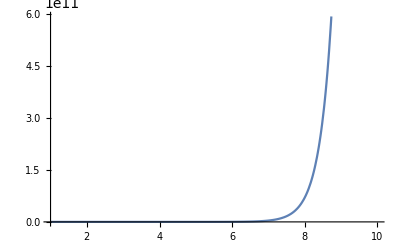

```mathematica
Plot[f[x],{x,1,10}]
```

```mathematica
emptyTable=Partition[Table[" ",{100}],10];
Grid[emptyTable,Dividers->Gray]
```

|   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |

```mathematica
Grid[emptyTable,Dividers->Dotted]
```

|   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |

```mathematica
Grid[emptyTable,Dividers->Thick]
```

|   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |

```mathematica
Grid[emptyTable,Dividers->Directive[Thin,Orange]]
```

|   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |

```mathematica
Grid[emptyTable,Dividers->{{Black,{Gray},Black},None}]
```

|   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |

```mathematica
Grid[emptyTable,Dividers->{{Black,{Gray},Black},{Black,Black,{None},Black}}]
```

|   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |

```mathematica
Grid[emptyTable,Dividers->{{True,{Gray},True},{True,True,{False},True}}]
```

|   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |

```mathematica
Grid[emptyTable,Dividers->{{Black,{Gray},Black},{Black,Black,{None},Black}},
Background->{None,{Lighter[Gray,.7],{Lighter[Blue,.9],Lighter[Yellow,.9]}}}]
```

|   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |  
  |   |   |   |   |   |   |   |   |

```mathematica
Clear[gridData];
gridData=Table[{10^n,10.^n},{n,-5,5}];
Grid@gridData
```

1/100000 | 0.00001
1/10000 | 0.0001
1/1000 | 0.001
1/100 | 0.01
1/10 | 0.1
1 | 1.
10 | 10.
100 | 100.
1000 | 1000.
10000 | 10000.
100000 | 100000.

```mathematica
With[{
gridData=Table[{10^ToString[n],10.^n},{n,-5,5}]},
Text@Grid[gridData,
Dividers->{Black,{Black,{Gray},Black}},
Background->{{Blue,None},{{Lighter[Blue,.9],Lighter[Yellow,.9]}}},
Alignment->{{Left,"."},Baseline},
ItemStyle->{{{{FontFamily->"Helvetica",FontColor->White}},Black},None}
]]
```

10^-5 | 0.00001
10^-4 | 0.0001
10^-3 | 0.001
10^-2 | 0.01
10^-1 | 0.1
10^0 | 1.
10^1 | 10.
10^2 | 100.
10^3 | 1000.
10^4 | 10000.
10^5 | 100000.

```mathematica
Manipulate[
Grid[{{
(* top left *)
Plot[Sin[x],{x,-π,π},
AspectRatio->Automatic,
Ticks->{{-π,-π/2,π/2,π},{-1,1}},
Epilog->{Red,PointSize[.03],Point[{x0,Sin[x0]}]}],
(* top right *)
Style["Full View","Subsubsection"]
},{
(* bottom left *)
Plot[Sin[x],{x,x0-δ,x0+δ},
Axes->False,
GridLines->Automatic,
Frame->True,
Epilog->{Red,PointSize[.03],Point[{x0,Sin[x0]}]}],
(* bottom right *)
Style["Zoom View","Subsubsection"]
}}],
(* Manipulate controls *)
{{x0,0.,"Center"},-2,2},{{δ,1.,"Zoom Level"},2,10^-10}]
```

## 3.6 Working with Piecewise Defined Functions

Esc + pw + Esc to create a single bracket of a piecewise defined function. Then Ctrl+, to produce a grid. For a new row, press Ctrl+Enter

```mathematica
f[x_]:=Piecewise[{{x, 0≤x≤1}, {-x, -1<x<0}, {1, True}}]
```

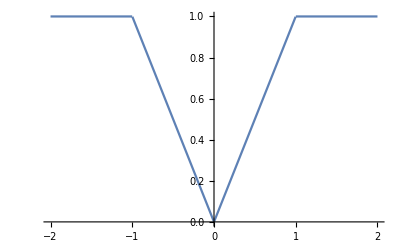

```mathematica
Plot[f[x],{x,-2,2}]
```

```mathematica
f[x_]:=Piecewise[{{x,0≤x≤1},{-x,-1<x<0}},1]
```

```mathematica
Plot[f[x],{x,-2,2}]
```

-Graphics-

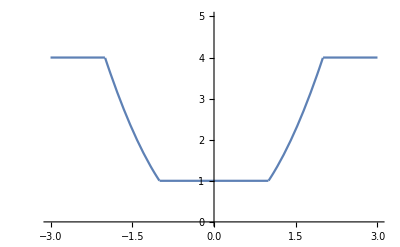

```mathematica
g[x_]:=Piecewise[{{x^2, (-2≤x≤-1)||(1≤x≤2)}, {1, -1<x<1}, {4, True}}]
Plot[g[x],{x,-3,3},PlotRange->{0,5}]
```

```mathematica
g[x_]:=Piecewise[{{x^2, 1≤Abs[x]≤2}, {1, Abs[x]<1}, {4, True}}]
Plot[g[x],{x,-3,3},PlotRange->{0,5}]
```

-Graphics-

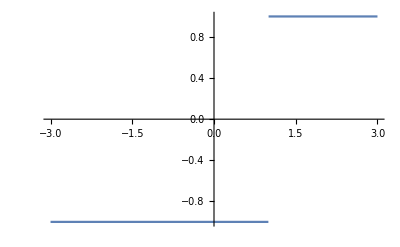

```mathematica
Plot[Piecewise[{{1, x≥1}, {-1, x<1}}],{x,-3,3}]
```

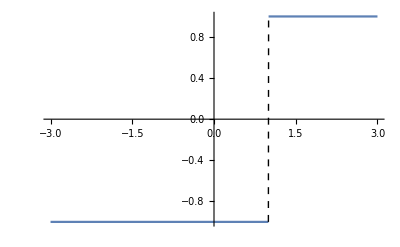

```mathematica
Plot[Piecewise[{{1, x≥1}, {-1, x<1}}],{x,-3,3},ExclusionsStyle->Dashed]
```

```mathematica
Plot[Piecewise[{{1, x≥1}, {-1, True}}],{x,-3,3},ExclusionsStyle->Dashed]
```

-Graphics-

### Exercises

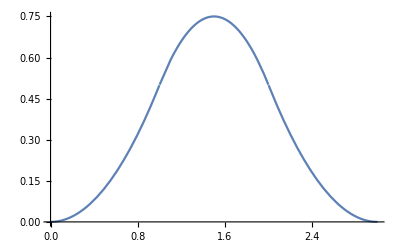

```mathematica
Plot[Piecewise[{{0, x<0}, {x^2/2, 0≤x<1}, {-x^2+3 x-3/2, 1≤x<2}, {1/2 (3-x)^2, 2≤x<3}, {0, 3≤x}}],{x,0,3}]
```

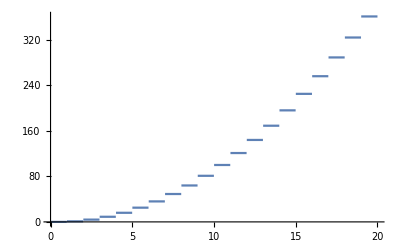

```mathematica
Plot[Piecewise[Table[{n^2,n≤x<n+1},{n,0,19}]],{x,0,20},Exclusions->Range[19]]
```

## 3.7 Plotting Implicitly Defined Functions

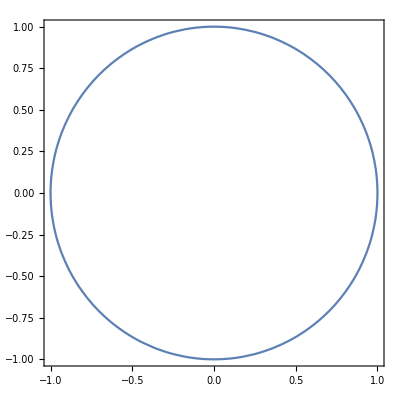

```mathematica
ContourPlot[x^2+y^2==1,{x,-1,1},{y,-1,1}]
```

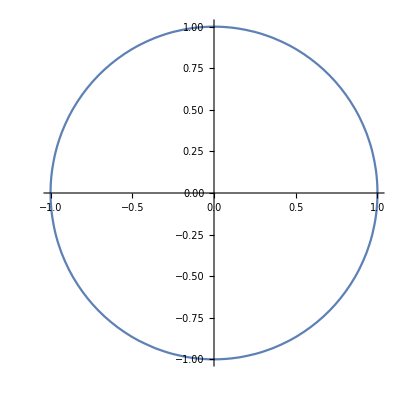

```mathematica
ContourPlot[x^2+y^2==1,{x,-1,1},{y,-1,1},Frame->False,Axes->True]
```

The default AspectRatio→1 is misleading:

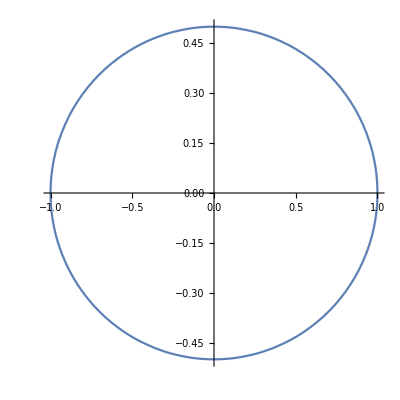

```mathematica
ContourPlot[x^2+4 y^2==1,{x,-1,1},{y,-.5,.5},Frame->False,Axes->True]
```

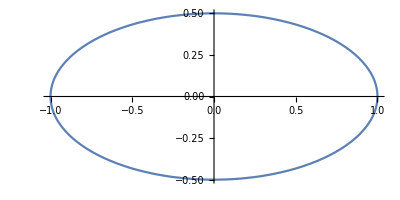

```mathematica
ContourPlot[x^2+4 y^2==1,{x,-1,1},{y,-.5,.5},Frame->False,Axes->True,AspectRatio->Automatic]
```

The plotting algorithm may produce jagged lines:

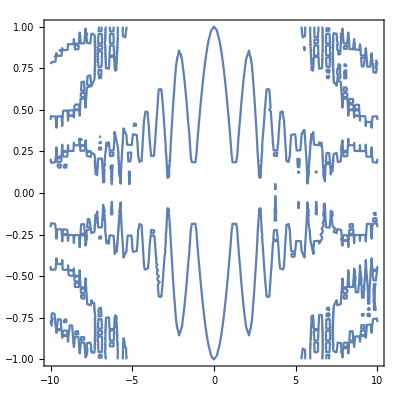

```mathematica
ContourPlot[Sin[x^2]+y^2==Cos[x y],{x,-10,10},{y,-1,1}]
```

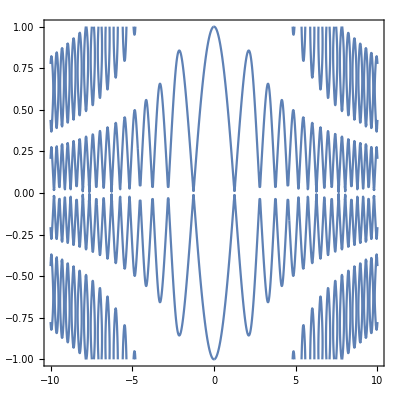

```mathematica
ContourPlot[Sin[x^2]+y^2==Cos[x y],{x,-10,10},{y,-1,1},PlotPoints->100]
```

Produce a list of equations to plot simultaneously:

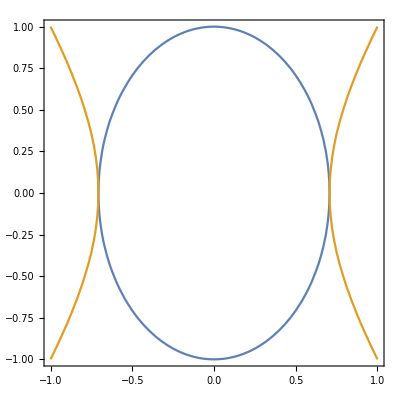

```mathematica
ContourPlot[{2 x^2+y^2==1,2 x^2-y^2==1},{x,-1,1},{y,-1,1}]
```

```mathematica
Manipulate[
ContourPlot[2 x^2-y^2==1,{x,-2,2},{y,-2,2},
PlotPoints->plotPoints,MaxRecursion->maxRecursion,Mesh->mesh,MeshStyle->Directive[PointSize[Medium],Red]],
{{plotPoints,4},{2,3,4,8}},{{maxRecursion,2},{0,1,2,3}},{mesh,{Full,All}}]
```

### Exercises

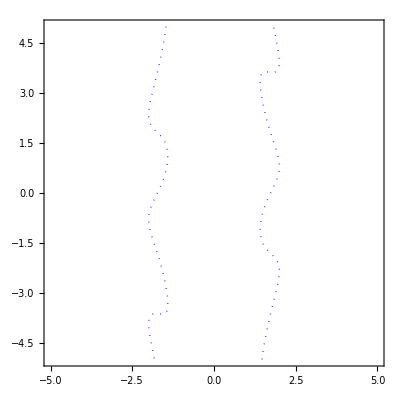

```mathematica
ContourPlot[x^2-Sin[x y]==3,{x,-5,5},{y,-5,5},ContourStyle->Directive[Thick,Blue,Dotted]]
```

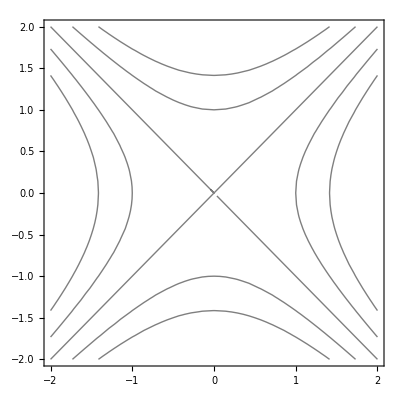

```mathematica
ContourPlot[x^2-y^2,{x,-2,2},{y,-2,2},Contours->{-2,-1,0,1,2},ContourShading->False]
```

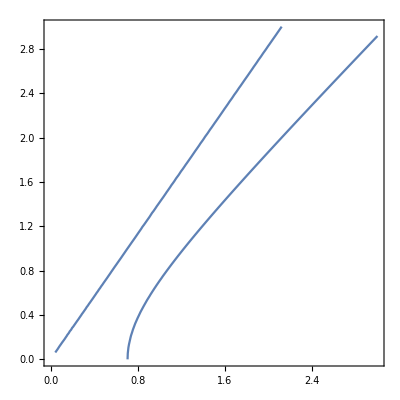

```mathematica
ContourPlot[Piecewise[{{x^2-y^2,x≥y},{1-x^2/y^2,x≤y}}]==1/2,{x,0,3},{y,0,3}]
```

## 3.8 Combining Graphics

### Superimposing Plots

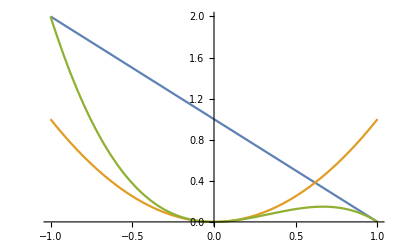

```mathematica
Clear[f,g];
f[x_]:=1-x;
g[x_]:=x^2;
Plot[{f[x],g[x],f[x] g[x]},{x,-1,1}]
```

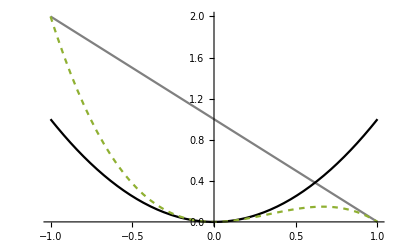

```mathematica
Plot[Tooltip[{f[x],g[x],f[x] g[x]}],{x,-1,1},PlotStyle->{Gray,Black,Dashing[{.01}]}]
```

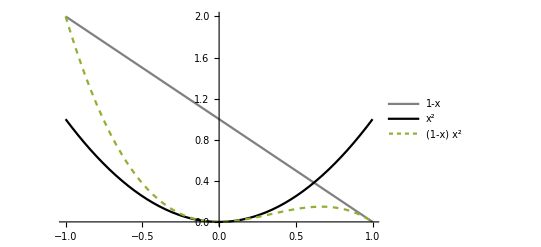

```mathematica
Plot[Tooltip[{f[x],g[x],f[x] g[x]}],{x,-1,1},PlotStyle->{Gray,Black,Dashing[{.01}]},PlotLegends->{f[x],g[x],f[x] g[x]}]
```

```mathematica
Plot[Tooltip[{f[x],g[x],f[x] g[x]}],{x,-1,1},PlotStyle->{Gray,Black,Dashing[{.01}]},PlotLegends->Placed[{f[x],g[x],f[x] g[x]},Bottom]]
```

-Graphics-

```mathematica
Plot[Tooltip[{f[x],g[x],f[x] g[x]}],{x,-1,1},PlotStyle->{Gray,Black,Dashing[{.01}]},PlotLabels->Placed[Automatic,Below]]
```

-Graphics-

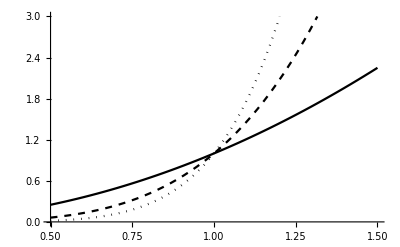

```mathematica
Plot[{x^2,x^4,x^6},{x,.5,1.5},PlotRange->{0,3}, PlotStyle->{Black,Directive[Dashed,Black],Directive[Dotted,Black]}]
```

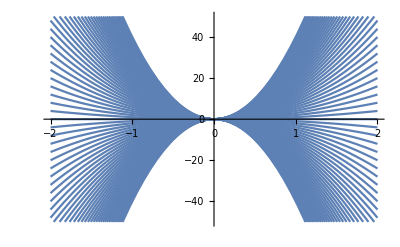

```mathematica
Plot[Table[n x^2,{n,-40,40}],{x,-2,2},PlotRange->50]
```

Wrap Table in Evaluate to reduce the time of computation. Evaluate forces Plot to first evaluate its initial argument before plugging in any values of x, otherwise Plot re-evaluates the expression for each x.

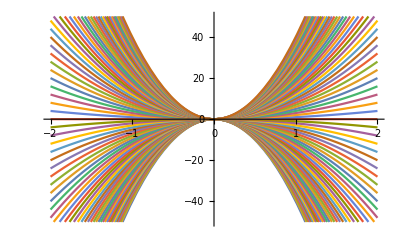

```mathematica
Plot[Evaluate[Table[n x^2,{n,-40,40}]],{x,-2,2},PlotRange->50]
```

### Producing Filled Plots

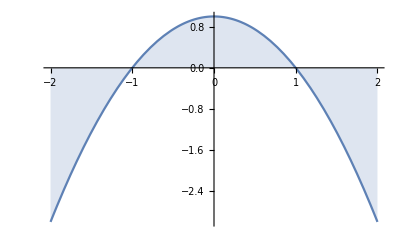

```mathematica
Plot[1-x^2,{x,-2,2},Filling->Axis]
```

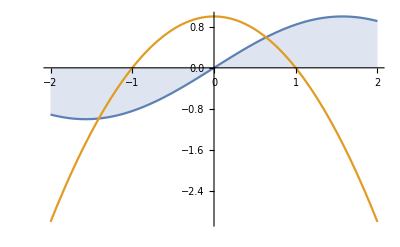

```mathematica
Plot[{Sin[x],1-x^2},{x,-2,2},Filling->{1->Axis}]
```

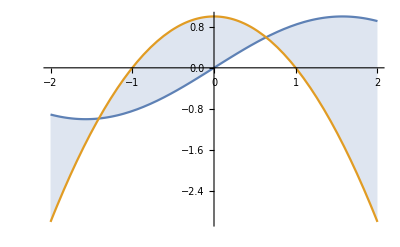

```mathematica
Plot[{Sin[x],1-x^2},{x,-2,2},Filling->{1->{2}}]
```

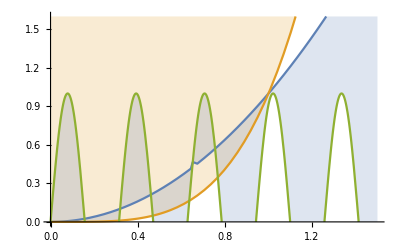

```mathematica
Plot[{x^2,x^4,Sin[20x]},{x,0,1.5},PlotRange->{0,1.6},Filling->{1->{3},2->Top}]
```

### Superimposing Graphics

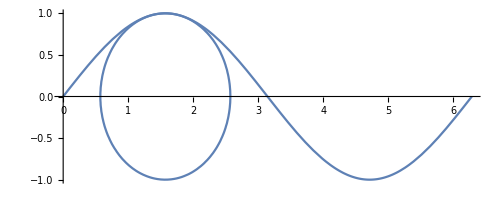

```mathematica
p1=Plot[Sin[x],{x,0,2π},AspectRatio->Automatic];
p2=ContourPlot[(x-π/2)^2+y^2==1,{x,0,3},{y,-1,1}];
Show[p1,p2]
```

Plot domain and option setting will be inherited from the first image listed within Show:

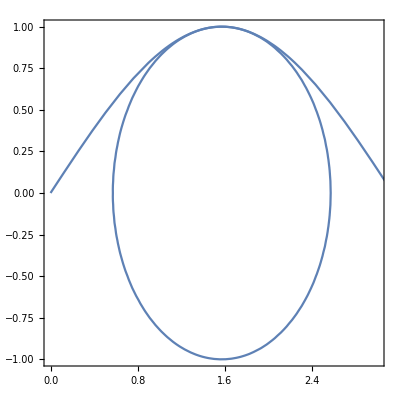

```mathematica
Show[p2,p1]
```

The first graphic is rendered first, the second overlaid on top of it:

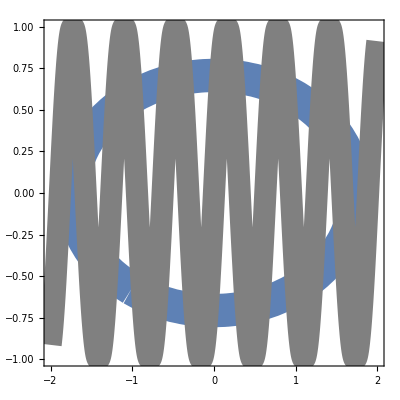

```mathematica
ellipse=ContourPlot[x^2/3+2 y^2==1,{x,-2,2},{y,-1,1},ContourStyle->Thickness[.06]];
squiggle=Plot[Sin[10x],{x,-2,2},PlotStyle->Directive[Gray,Thickness[.04]]];
Show[ellipse,squiggle]
```

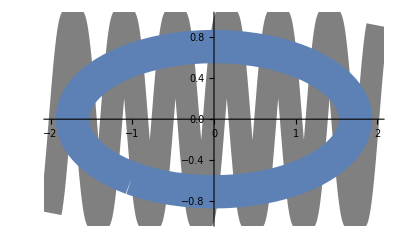

```mathematica
Show[squiggle,ellipse]
```

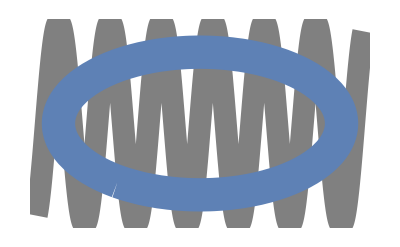

```mathematica
Show[squiggle,ellipse,Axes->False]
```

### Graphics Side-by-Side

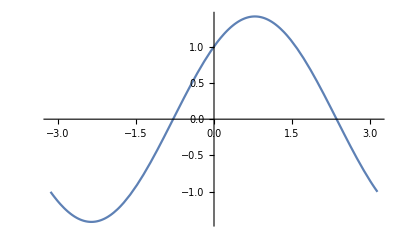
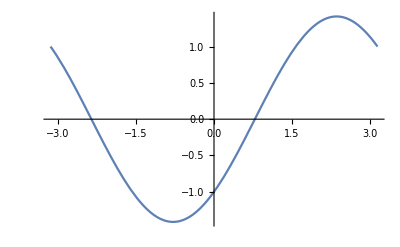

```mathematica
{Plot[Sin[x]+Cos[x],{x,-π,π}],Plot[Sin[x]-Cos[x],{x,-π,π}]}
```

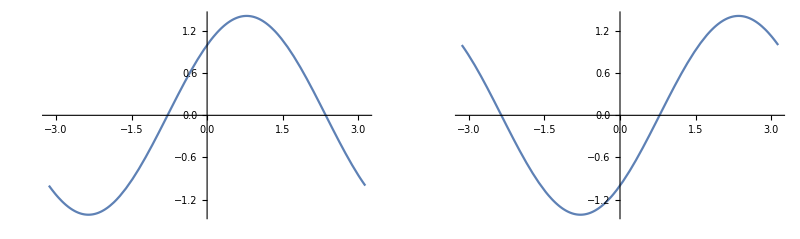

```mathematica
GraphicsRow[%]
```

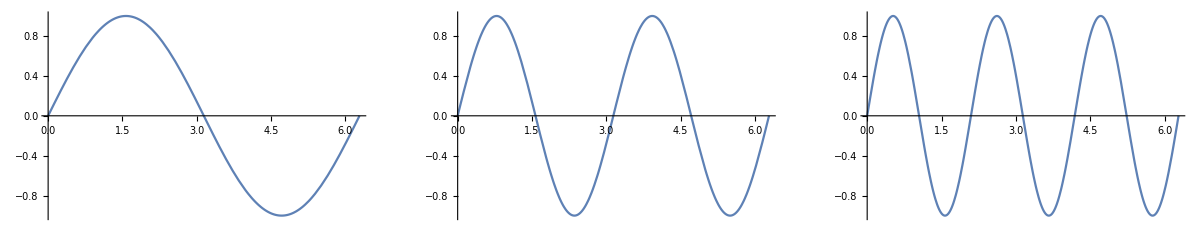

```mathematica
GraphicsRow[Table[Plot[Sin[m x],{x,0,2π}],{m,3}],Frame->All,FrameStyle->Dotted]
```

### Graphics in a Grid

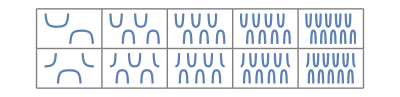

```mathematica
GraphicsGrid[{
Table[Plot[Csc[m x],{x,0,2π},Axes->False],{m,5}],
Table[Plot[Sec[m x],{x,0,2π},Axes->False],{m,5}]},
Frame->All,FrameStyle->Gray]
```

### Exercises

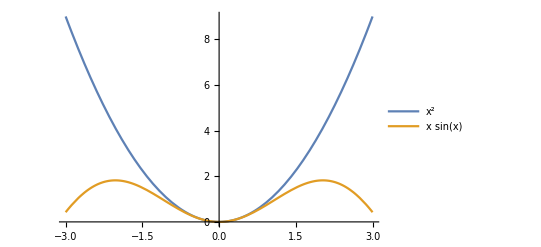

```mathematica
Plot[{x^2,x Sin[x]},{x,-3,3},PlotLegends->"Expressions"]
```

```mathematica
Plot[{x^2,x Sin[x]},{x,-3,3},PlotLabels->Automatic]
```

-Graphics-

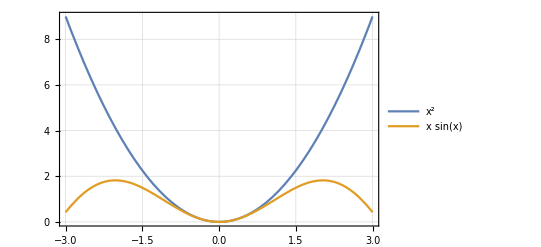

```mathematica
Plot[{x^2,x Sin[x]},{x,-3,3},PlotTheme->"Detailed"]
```

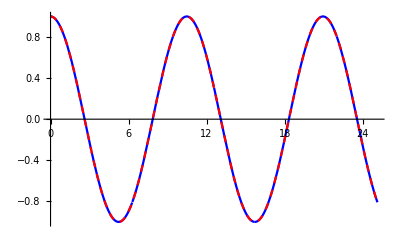

```mathematica
Plot[{(Sin[.4 t]+Sin[1.6t])/(2 Sin[t]),Cos[.6t]},{t,0,8π},PlotStyle->{Blue,Directive[Red,Dashed]}]
```

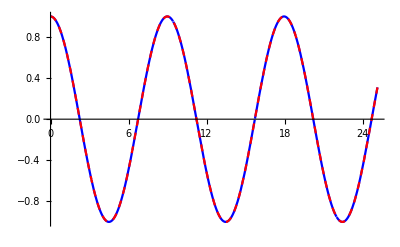

```mathematica
Plot[{(Sin[.3 t]+Sin[1.7t])/(2 Sin[t]),Cos[.7t]},{t,0,8π},PlotStyle->{Blue,Directive[Red,Dashed]}]
```

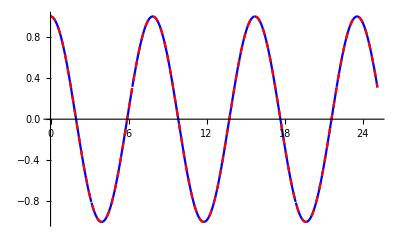

```mathematica
Plot[{(Sin[.2 t]+Sin[1.8t])/(2 Sin[t]),Cos[.8t]},{t,0,8π},PlotStyle->{Blue,Directive[Red,Dashed]}]
```

```mathematica
Manipulate[
Plot[{Sin[k t]/(2 Sin[t]),Sin[(2-k)t]/(2 Sin[t]),Cos[(1-k)t]},{t,0,8π},PlotRange->2,PlotStyle->{Darker[Gray],Darker[Pink],Directive[Thick,Black]},GridLines->{Range[0,8π,π],{}},Ticks->{Range[0,8π,π],Automatic},Filling->{1->Axis,2->Axis}],{{k,.4},0,2}]
```

```mathematica
Limit[Sin[.4t]/(2 Sin[t]),t->5π]
```

-0.2

```mathematica
Limit[Sin[1.6t]/(2 Sin[t]),t->5π]
```

-0.8

```mathematica
plotOpts=Options[Plot];
SetOptions[Plot,Ticks->None,AxesOrigin->{0,0},ImageSize->150];
myStyle[txt_]:=Style[txt,"Subsubsection",14];
Grid[{
{myStyle["Plot of p*x^n looks like:"],myStyle["When:"],myStyle["Plot of -p*x^n looks like:"],myStyle["When:"]},

{Plot[x^2,{x,0,4}],myStyle["n>1"],Plot[-x^2,{x,0,4}],myStyle["n>1"]},

{Plot[x,{x,0,4}],myStyle["n=1"],Plot[-x,{x,0,4}],myStyle["n=1"]},

{Plot[x^(.5),{x,0,4}],myStyle["0<n<1"],Plot[-x^(.5),{x,0,4}],myStyle["0<n<1"]},

{Plot[x^-1,{x,0,4}],myStyle["n<0"],Plot[-x^-1,{x,0,4}],myStyle["n<0"]}
},Dividers->{{Gray,False,Gray,False,Gray},Gray},Spacings->3]
```

Plot of p*x^n looks like: | When: | Plot of -p*x^n looks like: | When:
-Graphics- | n>1 | -Graphics- | n>1
-Graphics- | n=1 | -Graphics- | n=1
-Graphics- | 0<n<1 | -Graphics- | 0<n<1
-Graphics- | n<0 | -Graphics- | n<0

## 3.9 Enhancing Your Graphics

```mathematica
Plot[{Sin[x],ArcSin[x]},{x,-π/2,π/2},PlotStyle->{Automatic,Dashed},AspectRatio->Automatic,AxesLabel->{x,y}]
```

```mathematica
Line[{{0,0},{1,1},{2,0}}]
```

Line[{{0,0},{1,1},{2,0}}]

```mathematica
Graphics[Line[{{0,0},{1,1},{2,0}}]]
```

-Graphics-

```mathematica
Graphics[{Directive[Thick,Dashed],Line[{{0,0},{1,1},{2,0}}]}]
```

-Graphics-

```mathematica
Graphics[{Directive[Thick,Dashed],Line[{{0,0},{1,1},{2,0}}]},Axes->True]
```

-Graphics-

```mathematica
Graphics[{
{Directive[Thick,Gray],Line[Table[{x,Sin[x]},{x,0,6.3,.1}]]},
{Directive[Dashed,Blue],Line[{{2,0},{2,Sin[2]},{0,Sin[2]}}]},
{Directive[PointSize[.02],Yellow],Point[{2,Sin[2]}]}
},Axes->True]
```

-Graphics-

```mathematica
Plot[Sin[x],{x,0,2π},AspectRatio->Automatic,
Epilog->{Directive[Dashed,Blue],Line[{{2,0},{2,Sin[2]},{0,Sin[2]}}]}
]
```

-Graphics-

```mathematica
Manipulate[Plot[Sin[t],{t,0,2π},Ticks->{Range[0,2π,π/6],Sin[Range[-π/2,π/2,π/6]]},
Epilog->{{Dashed,Line[{{x,0},{x,Sin[x]},{0,Sin[x]}}]},
{Red,PointSize[.015],Point[{x,Sin[x]}]}}],{{x,(2π)/3},0,2π}]
```

Get rid of the Output label:

```mathematica
Print@Plot[Sin[x]^5-Cos[x^5],{x,-3,3}]
```

-Graphics-

### Exercises

```mathematica
Graphics[{
Circle[{0,0},{4,2}],
Rectangle[{-1,-1},{1,1}]
},Frame->True]
```

-Graphics-

```mathematica
Graphics[{Red,Disk[]}]
```

-Graphics-

```mathematica
Graphics[{Lighter[Blend[{Blue,Red},.3],.4],Disk[]}]
```

-Graphics-

```mathematica
Manipulate[
Graphics[{Lighter[Blend[{Blue,Red},b],l],Disk[]}],
{{b,.3,"Blue/Red"},0,1},
{{l,.4,"Brightness"},0,1}
]
```

```mathematica
Manipulate[
Graphics[{
{Blue,Disk[]},
{Opacity[opacity],Disk[{1,0},1]}
}],
{{opacity,.5,"Opacity"},0,1}
]
```

```mathematica
Manipulate[
Graphics[{
{Blue,Disk[]},
{Directive[Orange,Opacity[opacity]],Disk[{1,0},1]}
}],
{{opacity,.5,"Opacity"},0,1}
]
```

```mathematica
Manipulate[
Graphics[{
Thickness[.02],
Circle[{0,0},{1,r},{π,2π}]
}],
{{r,.6,"Radius"},.01,1}
]
```

```mathematica
Manipulate[Graphics[{
{Yellow,Disk[{0,0},1.3]},
Disk[{-.3,.5},{.1,.2}],
Disk[{.3,.5},{.1,.2}],
{Thickness[.02],Line[{{-.5,1.5-h},{-.1,h}}]},
{Thickness[.02],Line[{{.5,1.5-h},{.1,h}}]},
{Thickness[.02],Circle[{0,0},{1,r},{π,2π}]}
}],{{r,.8,"mouth"},.01,1},{{h,.65,"eyebrows"},.5,1}]
```

```mathematica
Graphics[Circle[{0,0},{2,3}],Axes->True]
```

-Graphics-

```mathematica
ellipse[k_,n_]:=Circle[{0,0},{√((k(n-k+1))/(n+2)),√(((n-k+1) (n-k+2))/((n+1) (n+2)))}];
Graphics[Table[ellipse[k,20],{k,20}],Axes->True]
```

-Graphics-

```mathematica
Graphics[ellipse[1,20],Axes->True]
```

-Graphics-

```mathematica
ellipse[1,20]
```

Circle[{0,0},{√(10/11),√(10/11)}]

```mathematica
Text@Grid[
Table[{k,√((k(20-k+1))/(20+2))//N},{k,20}],
Dividers->All,
Alignment->".",
Spacings->3,
Background->{None,{10->Lighter[Gray],11->Lighter[Gray]}}]
```

1 | 0.953463
2 | 1.31426
3 | 1.5667
4 | 1.7581
5 | 1.90693
6 | 2.0226
7 | 2.11058
8 | 2.17423
9 | 2.21565
10 | 2.23607
11 | 2.23607
12 | 2.21565
13 | 2.17423
14 | 2.11058
15 | 2.0226
16 | 1.90693
17 | 1.7581
18 | 1.5667
19 | 1.31426
20 | 0.953463

## 3.10 Working with Data

```mathematica
data={{0, 149.5}, {2, 141.7}, {4, 134.7}, {6, 128.3}, {8, 122.6}, {10, 117.4}, {12, 112.7}, {14, 108.5}, {16, 104.7}, {18, 101.3}, {20, 98.2}, {22, 95.4}, {24, 92.9}, {26, 90.5}, {28, 88.5}, {30, 86.6}};
```

```mathematica
data
```

{{0,149.5},{2,141.7},{4,134.7},{6,128.3},{8,122.6},{10,117.4},{12,112.7},{14,108.5},{16,104.7},{18,101.3},{20,98.2},{22,95.4},{24,92.9},{26,90.5},{28,88.5},{30,86.6}}

```mathematica
ListPlot[data]
```

-Graphics-

```mathematica
ListPlot[{{1,1},{2,3},{3,2},{4,3}}]
```

-Graphics-

```mathematica
ListPlot[{{1,1},{2,3},{3,2},{4,3}},Joined->True,PlotMarkers->\[MathematicaIcon],AxesOrigin->{0,0},PlotRange->{0,3.5}]
```

-Graphics-

```mathematica
scatterplot=ListPlot[Tooltip[data],AxesLabel->{"min","temperature (°F)"},
PlotStyle->Directive[PointSize[Small],Blue],
Filling->Axis,AxesOrigin->{-1,80}]
```

-Graphics-

```mathematica
fitLine=Fit[data,{1,x},x]
```

141.332-2.03257 x

```mathematica
fitQuadratic=Fit[data,{1,x,x^2},x]
```

148.465-3.56107 x+0.0509498 x^2

```mathematica
Plot[fitQuadratic,{x,0,30},Epilog->Point[data]]
```

-Graphics-

```mathematica
Show[scatterplot,Plot[{fitLine,fitQuadratic},{x,0,30},Filling->True]]
```

-Graphics-

```mathematica
Show[scatterplot,Plot[fitLine,{x,0,30}],PlotLabel->Style[fitLine,12]]
Show[scatterplot,Plot[fitQuadratic,{x,0,30}],PlotLabel->Style[fitQuadratic,12]]
```

-Graphics-

-Graphics-

```mathematica
GraphicsRow[
Table[Show[scatterplot,Plot[f,{x,0,30}],PlotLabel->f],
{f,{fitLine,fitQuadratic}}]
]
```

-Graphics-

```mathematica
FindFit[data,a+b c^x,{a,b,{c,.5}},x]
```

{a→69.348,b→80.1489,c→0.95015}

```mathematica
Show[scatterplot,Plot[69.348+80.1489 0.95015^x,{x,0,30}]]
```

-Graphics-

```mathematica
Plot[69.348+80.1489 0.95015^x,{x,0,200},AxesOrigin->{0,60}]
```

-Graphics-

### Exercises

```mathematica
data={{1, 1.2}, {2, 2.3}, {3, 3.6}, {4, 4.9}, {5, 5.9}};
```

```mathematica
ListPlot[data]
```

-Graphics-

```mathematica
fitLinear=Fit[data,{1,x},x]
```

-0.02+1.2 x

```mathematica
Plot[fitLinear,{x,0,5},Epilog->Point[data]]
```

-Graphics-

```mathematica
FindFit[data,p x^n,{p,{n,1}},x]
```

{p→1.18974,n→1.00295}

```mathematica
fitPolinomial=1.18974 x^1.00295;
```

```mathematica
Plot[fitPolinomial,{x,0,5},AxesOrigin->{0,0},Epilog->Point[data]]
```

-Graphics-

```mathematica
Text@Grid[Prepend[Table[{x,data⟦x,2⟧,fitLinear,data⟦x,2⟧-fitLinear},{x,data⟦All,1⟧}],{"x","y","Predicted","Residual"}],Alignment->Right]
```

x | y | Predicted | Residual
1 | 1.2 | 1.18 | 0.02
2 | 2.3 | 2.38 | -0.08
3 | 3.6 | 3.58 | 0.02
4 | 4.9 | 4.78 | 0.12
5 | 5.9 | 5.98 | -0.08

```mathematica
Text@Grid[Prepend[Table[{x,data⟦x,2⟧,fitPolinomial,data⟦x,2⟧-fitPolinomial},{x,data⟦All,1⟧}],{"x","y","Predicted","Residual"}],Alignment->Right]
```

x | y | Predicted | Residual
1 | 1.2 | 1.18974 | 0.01026
2 | 2.3 | 2.38435 | -0.0843505
3 | 3.6 | 3.58081 | 0.0191937
4 | 4.9 | 4.77846 | 0.121538
5 | 5.9 | 5.97701 | -0.0770106

```mathematica
residualPlot[data_,function_,{x_,xmin_,xmax_},opts___Rule]:=Show[
ListPlot[{data,Table[{x,function},{x,data⟦All,1⟧}]},Filling->{1->{2}},FillingStyle->{Red,Green},PlotMarkers->{"⋆",""},opts],
Plot[function,{x,xmin,xmax}]
]
```

```mathematica
residualPlot[data,3-.25x+.125 x^2,{x,0,6},Axes->False,Frame->True,PlotRange->{{0,6},{-1,7}}]
```

-Graphics-

```mathematica
Clear[data,residualPlot,fitLinear,fitQuadratic,fitPolinomial,fitExponential,fitLine]
```

```mathematica
Manipulate[
Graphics[{Directive[Thick,Blue],Circle[{pt[[1]],pt[[2]]},.1]},Axes->True,PlotRange->1],
{{pt,{0,0}},Locator,Appearance->None}]
```

## 3.11 Managing Data - An Introduction to Lists

```mathematica
myList=Table[2^k,{k,10}]
```

{2,4,8,16,32,64,128,256,512,1024}

```mathematica
myList[[5]]
```

32

Press Esc + [[ and Esc + ]] to produce double square bracket symbols which have the same meaning:

```mathematica
myList⟦5⟧
```

32

```mathematica
myList_⟦5⟧
```

32

```mathematica
myList[[-2]]
```

512

```mathematica
myList[[1;;4]]
```

{2,4,8,16}

```mathematica
First[myList]
```

2

```mathematica
Last[myList]
```

1024

```mathematica
{1,2,3,4}+1
```

{2,3,4,5}

```mathematica
2*myList
```

{4,8,16,32,64,128,256,512,1024,2048}

```mathematica
Log[2,myList]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
??Listable
```

Two-dimensional data is stored as a list of lists:

```mathematica
data={{1, 214}, {11, 378}, {21, 680}, {31, 1215}, {41, 2178}, {51, 3907}}
```

{{1,214},{11,378},{21,680},{31,1215},{41,2178},{51,3907}}

```mathematica
data⟦3⟧
```

{21,680}

Extract the item in row 3, column 2:

```mathematica
data⟦3,2⟧
```

680

Extract an entire column of a two dimensional table:

```mathematica
data⟦All,2⟧
```

{214,378,680,1215,2178,3907}

```mathematica
data⟦All,{1,2}⟧
```

{{1,214},{11,378},{21,680},{31,1215},{41,2178},{51,3907}}

```mathematica
Log[data]//Grid
```

0 | Log[214]
Log[11] | Log[378]
Log[21] | Log[680]
Log[31] | Log[1215]
Log[41] | Log[2178]
Log[51] | Log[3907]

```mathematica
newData=data;
newData⟦All,2⟧=Log[data⟦All,2⟧];
newData//Grid
```

1 | Log[214]
11 | Log[378]
21 | Log[680]
31 | Log[1215]
41 | Log[2178]
51 | Log[3907]

```mathematica
Transpose[{data⟦All,1⟧,Log[data⟦All,2⟧]}]//Grid
```

1 | Log[214]
11 | Log[378]
21 | Log[680]
31 | Log[1215]
41 | Log[2178]
51 | Log[3907]

```mathematica
data=Table[{x,RandomInteger[10],RandomReal[10],RandomComplex[]},{x,6}];
Grid[data,Dividers->Gray]
```

1 | 0 | 4.57016 | 0.657064+0.909674 ⅈ
2 | 10 | 2.94016 | 0.490239+0.60406 ⅈ
3 | 4 | 2.87644 | 0.641445+0.227411 ⅈ
4 | 5 | 9.38003 | 0.155836+0.544219 ⅈ
5 | 5 | 2.73898 | 0.280043+0.870437 ⅈ
6 | 1 | 9.21179 | 0.758334+0.463406 ⅈ

```mathematica
data
```

{{1,0,4.57016,0.657064+0.909674 ⅈ},{2,10,2.94016,0.490239+0.60406 ⅈ},{3,4,2.87644,0.641445+0.227411 ⅈ},{4,5,9.38003,0.155836+0.544219 ⅈ},{5,5,2.73898,0.280043+0.870437 ⅈ},{6,1,9.21179,0.758334+0.463406 ⅈ}}

```mathematica
newData=Transpose[{data⟦All,1⟧,Log[data⟦All,3⟧]}];
Grid[newData,Dividers->Gray]
```

1 | 1.51955
2 | 1.07847
3 | 1.05655
4 | 2.23858
5 | 1.00759
6 | 2.22048

### Exercises

```mathematica
data⟦All,{2,4}⟧//Grid
```

0 | 0.657064+0.909674 ⅈ
10 | 0.490239+0.60406 ⅈ
4 | 0.641445+0.227411 ⅈ
5 | 0.155836+0.544219 ⅈ
5 | 0.280043+0.870437 ⅈ
1 | 0.758334+0.463406 ⅈ

```mathematica
data⟦4;;,{2,3}⟧//Grid
```

5 | 9.38003
5 | 2.73898
1 | 9.21179

```mathematica
Transpose[{data⟦4;;,2⟧,Log[data⟦4;;,3⟧]}]//Grid
```

5 | 2.23858
5 | 1.00759
1 | 2.22048

## 3.12 Importing Data

```mathematica
Short[CountryData[],3]
```

{Afghanistan,Aland Islands,Albania,Algeria,American Samoa,Andorra,Angola,Anguilla,Antigua and Barbuda,Argentina,Armenia,Aruba,Australia,Austria,Azerbaijan,Bahamas,Bahrain,Bangladesh,Barbados,Belarus,Belgium,Belize,Benin,Bermuda,Bhutan,Bolivia,Caribbean Netherlands,Bosnia and Herzegovina,Botswana,Bouvet Island,Brazil,British Indian Ocean Territory,British Virgin Islands,Brunei,Bulgaria,Burkina Faso,Burundi,Cambodia,Cameroon,Canada,Cape Verde,Cayman Islands,Central African Republic,Chad,Chile,China,Christmas Island,Cocos Keeling Islands,Colombia,Comoros,Cook Islands,Costa Rica,Croatia,Cuba,Curacao,Cyprus,Czech Republic,Democratic Republic of the Congo,Denmark,Djibouti,Dominica,Dominican Republic,East Timor,Ecuador,Egypt,El Salvador,Equatorial Guinea,Eritrea,Estonia,Ethiopia,Falkland Islands,Faroe Islands,Fiji,Finland,France,French Guiana,French Polynesia,French Southern And Antarctic lands,Gabon,Gambia,Gaza Strip,Georgia,Germany,Ghana,Gibraltar,Greece,Greenland,Grenada,Guadeloupe,Guam,Guatemala,Guernsey,Guinea,Guinea-Bissau,Guyana,Haiti,Honduras,Hong Kong,Hungary,Iceland,India,Indonesia,Iran,Iraq,Ireland,Isle of Man,Israel,Italy,Ivory Coast,Jamaica,Japan,Jersey,Jordan,Kazakhstan,Kenya,Kiribati,Kosovo,Kuwait,«13»,Malawi,Malaysia,Maldives,Mali,Malta,Marshall Islands,Martinique,Mauritania,Mauritius,Mayotte,Mexico,Micronesia,Moldova,Monaco,Mongolia,Montenegro,Montserrat,Morocco,Mozambique,Myanmar,Namibia,Nauru,Nepal,Netherlands,New Caledonia,New Zealand,Nicaragua,Niger,Nigeria,Niue,Norfolk Island,Northern Mariana Islands,North Korea,Norway,Oman,Pakistan,Palau,Panama,Papua New Guinea,Paraguay,Peru,Philippines,Pitcairn Islands,Poland,Portugal,Puerto Rico,Qatar,Republic of the Congo,Réunion,Romania,Russia,Rwanda,Saint Barthelemy,Saint Helena, Ascension and Tristan da Cunha,Saint Kitts and Nevis,Saint Lucia,Saint Martin,Saint Pierre and Miquelon,Saint Vincent and the Grenadines,Samoa,San Marino,São Tomé and Príncipe,Saudi Arabia,Senegal,Serbia,Seychelles,Sierra Leone,Singapore,Sint Maarten,Slovakia,Slovenia,Solomon Islands,Somalia,South Africa,South Georgia and the South Sandwich Islands,South Korea,South Sudan,Spain,Sri Lanka,Sudan,Suriname,Svalbard,Eswatini,Sweden,Switzerland,Syria,Taiwan,Tajikistan,Tanzania,Thailand,Togo,Tokelau,Tonga,Trinidad and Tobago,Tunisia,Turkey,Turkmenistan,Turks and Caicos Islands,Tuvalu,Uganda,Ukraine,United Arab Emirates,United Kingdom,United States,United States Minor Outlying Islands,United States Virgin Islands,Uruguay,Uzbekistan,Vanuatu,Vatican City,Venezuela,Vietnam,Wallis and Futuna Islands,West Bank,Western Sahara,Yemen,Zambia,Zimbabwe}

```mathematica
CountryData[]//Length
```

249

```mathematica
Short[CountryData["Properties"],3]
```

{AdultPopulation,AgriculturalProducts,AgriculturalValueAdded,Airports,AlternateNames,AlternateStandardNames,«211»,UnpavedAirportLengths,UnpavedAirports,UnpavedRoadLength,ValueAdded,WaterArea,WaterwayLength}

```mathematica
CountryData["UnitedStates","Population"]
```

331449281 people

```mathematica
CountryData["UnitedStates",{"Population",1970}]
```

209513340 people

```mathematica
DateListPlot[CountryData["Kuwait",{"Population",{1970,2006}}]]
```

-Graphics-

```mathematica
CountryData["Germany","GDP"]
```

3.84641×10^12 $

```mathematica
CountryData["Greenland","OilConsumption"]
```

4000. bbl oil/day

```mathematica
Table[{c,CountryData[c,"GDP"],CountryData[c,"OilConsumption"]},{c,CountryData[]⟦1;;6⟧}]//Grid
```

Afghanistan | 1.98071×10^10 $ | 5000. bbl oil/day
Aland Islands | Missing[NotAvailable] | Missing[NotAvailable]
Albania | 1.47996×10^10 $ | 34000. bbl oil/day
Algeria | 1.45164×10^11 $ | 299000. bbl oil/day
American Samoa | 6.38×10^8 $ | 4000. bbl oil/day
Andorra | 3.15414×10^9 $ | Missing[NotAvailable]

```mathematica
Text@Grid[
Prepend[
Table[{c,CountryData[c,"GDP"],CountryData[c,"OilConsumption"]},{c,CountryData[]⟦1;;6⟧}],
Table[Style[x,FontWeight->"Bold"],{x,{"Country","Gross Domestic Product (US dollars)","Oil Consumption (Barrels per day)"}}]
],Dividers->{Center,{False,True}},Spacings->2,Alignment->{{Left,Center}}]
```

Country | Gross Domestic Product (US dollars) | Oil Consumption (Barrels per day)
Afghanistan | 1.98071×10^10 $ | 5000. bbl oil/day
Aland Islands | Missing[NotAvailable] | Missing[NotAvailable]
Albania | 1.47996×10^10 $ | 34000. bbl oil/day
Algeria | 1.45164×10^11 $ | 299000. bbl oil/day
American Samoa | 6.38×10^8 $ | 4000. bbl oil/day
Andorra | 3.15414×10^9 $ | Missing[NotAvailable]

```mathematica
ListLogLogPlot[Table[{CountryData[c,"GDP"],CountryData[c,"OilConsumption"]},{c,CountryData[]}]]
```

-Graphics-

```mathematica
ListLogLogPlot[Table[{CountryData[c,"Population"],CountryData[c,"OilConsumption"]},{c,CountryData[]}]]
```

-Graphics-

```mathematica
ListLogLogPlot[
Table[
Tooltip[
{CountryData[c,"GDP"],CountryData[c,"OilConsumption"]},
CountryData[c,"Name"]],
{c,CountryData[]}]]
```

-Graphics-

```mathematica
CountryData["Greece","Shape"]
```

-Graphics-

```mathematica
GraphicsGrid[
Partition[
Table[
Tooltip[
CountryData[c,"Shape"],
CountryData[c,"Name"]],
{c,CountryData["G8"]}],
4],
Dividers->All,
ImageSize->640]
```

-Graphics-

```mathematica
FinancialData["GE"]
```

63.25 $

```mathematica
DateListPlot[FinancialData["GE","Jan. 1, 2000"]]
```

-Graphics-

```mathematica
FinancialData[]//Length
```

57700

```mathematica
AstronomicalData["Earth","OrbitPeriod"]
```

3.1558149×10^7 s

```mathematica
AstronomicalData[]//Length
```

156771

```mathematica
ChemicalData[]//Length
```

44089

```mathematica
data=Table[
{
AstronomicalData[p,"OrbitPeriod"],
AstronomicalData[p,"SemimajorAxis"]
},
{p,AstronomicalData["Planet"]}];
ListLogLogPlot[data,AspectRatio->.3,ImageSize->500]
```

-Graphics-

```mathematica
data
```

{{7.600544×10^6 s,5.790918×10^10 m},{1.9414149×10^7 s,1.082089×10^11 m},{3.1558149×10^7 s,1.4959789×10^11 m},{5.9355036×10^7 s,2.2793664×10^11 m},{3.7435566×10^8 s,7.7841203×10^11 m},{9.2929236×10^8 s,1.4267254×10^12 m},{2.65137×10^9 s,2.87097222×10^12 m},{5.2004186×10^9 s,4.49825291×10^12 m}}

```mathematica
QuantityMagnitude[data]
```

{{7.600544×10^6,5.790918×10^10},{1.9414149×10^7,1.082089×10^11},{3.1558149×10^7,1.4959789×10^11},{5.9355036×10^7,2.2793664×10^11},{3.7435566×10^8,7.7841203×10^11},{9.2929236×10^8,1.4267254×10^12},{2.65137×10^9,2.87097222×10^12},{5.2004186×10^9,4.49825291×10^12}}

```mathematica
f=Function[x,a x^b]/.FindFit[QuantityMagnitude[data],a x^b,{a,b},x]
```

Function[x,1.496719×10^6 x^0.6667237]

```mathematica
Show[Plot[f[x],{x,0,10^10},PlotStyle->Red],ListPlot[data]]
```

-Graphics-

```mathematica
data=Import["https://web.archive.org/web/20090221083315if_/http://www.census.gov:80/genealogy/names/dist.male.first"];
```

```mathematica
data//Length
```

1219

```mathematica
Grid@data⟦;;5⟧
```

JAMES | 3.318 | 3.318 | 1
JOHN | 3.271 | 6.589 | 2
ROBERT | 3.143 | 9.732 | 3
MICHAEL | 2.629 | 12.361 | 4
WILLIAM | 2.451 | 14.812 | 5

```mathematica
Text@
Grid[
Join[{
{"Most Popular Male First Names from the 1990 Census",SpanFromLeft},
{"Name","Frequency (%)","Cumulative Frequency (%)","Rank"}},
data⟦1;;10⟧],Dividers->Gray]
```

Most Popular Male First Names from the 1990 Census |  |  | 
Name | Frequency (%) | Cumulative Frequency (%) | Rank
JAMES | 3.318 | 3.318 | 1
JOHN | 3.271 | 6.589 | 2
ROBERT | 3.143 | 9.732 | 3
MICHAEL | 2.629 | 12.361 | 4
WILLIAM | 2.451 | 14.812 | 5
DAVID | 2.363 | 17.176 | 6
RICHARD | 1.703 | 18.878 | 7
CHARLES | 1.523 | 20.401 | 8
JOSEPH | 1.404 | 21.805 | 9
THOMAS | 1.38 | 23.185 | 10

```mathematica
ListPlot[data⟦All,3⟧,Joined->True]
```

-Graphics-

```mathematica
pic=Import[
"https://romanakchurin.com/images/ai/perceptron-network.png",ImageSize->320]
```

-Graphics-

```mathematica
Short[InputForm[pic],3]
```

Image[NumericArray[{{{132, 116, 100}, {130, 114, 99}, {132, 116, 101}, {135, 119, 104}, {132, 116, 101}, {126, 110, 94}, {126, 110, 94}, <<169>>, {18, 21, 27}, {16, 19, 24}, {15, 18, 23}, {15, 18, 25}}, <<179>>}, "UnsignedInteger8"], <<4>>]

```mathematica
data2=Import["https://web.archive.org/web/20080623060532/http://colleges.usnews.rankingsandreviews.com/usnews/edu/college/rankings/brief/t1libartco_brief.php","Data"];
```

```mathematica
data2=data2⟦2,5,2,2⟧;
```

```mathematica
data2//Length
```

127

```mathematica
Grid[data2⟦5;;10⟧,Alignment->{{Right,Left}}]
```

3. | Swarthmore College (PA)
4. | Wellesley College (MA)
5. | Carleton College (MN)
5. | Middlebury College (VT)
7. | Pomona College (CA)
7. | Bowdoin College (ME)

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
baseballData=Import["data/NLBB.salaries.2005.xls"];
```

There are three sheets in the Excel spreadsheet:

```mathematica
baseballData//Length
```

3

```mathematica
Text@Grid[First[baseballData]⟦;;10⟧,Alignment->Left]
```

National League Baseball Salaries (2005) |  |  | 
 |  |  | 
Team | Name | Salary | Position
 |  |  | 
Arizona Diamondbacks | Aquino, Greg | 325000. | Pitcher
Arizona Diamondbacks | Bruney, Brian | 322500. | Pitcher
Arizona Diamondbacks | Choate, Randy | 550000. | Pitcher
Arizona Diamondbacks | Cintron, Alex | 360000. | Shortstop
Arizona Diamondbacks | Clark, Tony | 750000. | First Baseman
Arizona Diamondbacks | Clayton, Royce | 1.35×10^6 | Shortstop

```mathematica
Histogram[First[baseballData]⟦5;;-4,3⟧]
```

-Graphics-

```mathematica
$ImportFormats
```

{3DS,ACO,Affymetrix,AgilentMicroarray,AIFF,ApacheLog,ArcGRID,AU,AVI,Base64,BDF,Binary,Bit,BMP,BSON,Byte,BYU,BZIP2,CDED,CDF,Character16,Character32,Character8,CIF,Complex128,Complex256,Complex64,CSV,CUR,DAE,DBF,DICOM,DIF,DIMACS,Directory,DOT,DXF,EDF,EML,EPS,ExpressionJSON,ExpressionML,FASTA,FASTQ,FCS,FITS,FLAC,GenBank,GeoJSON,GeoTIFF,GIF,GPX,Graph6,Graphlet,GraphML,GRIB,GTOPO30,GXL,GZIP,HarwellBoeing,HDF,HDF5,HIN,HTML,HTTPRequest,HTTPResponse,ICC,ICNS,ICO,ICS,Ini,Integer128,Integer16,Integer24,Integer32,Integer64,Integer8,JavaProperties,JavaScriptExpression,JCAMP-DX,JPEG,JPEG2000,JSON,JSONLD,JVX,KML,LaTeX,LEDA,List,LWO,M4A,MAT,MathML,MBOX,MCTT,MDB,MESH,MGF,MIDI,MMCIF,MO,MOL,MOL2,MP3,MPS,MTP,MTX,MX,MXNet,NASACDF,NB,NDK,NetCDF,NEXUS,NOFF,NQuads,NTriples,OBJ,ODS,OFF,OGG,OpenEXR,Package,Pajek,PBM,PCAP,PCX,PDB,PDF,PGM,PHPIni,PLY,PNG,PNM,PPM,PXR,PythonExpression,QuickTime,Raw,RawBitmap,RawJSON,RDFXML,Real128,Real32,Real64,RIB,RLE,RSS,RTF,SCT,SDF,SDTS,SDTSDEM,SFF,SHP,SMA,SME,SMILES,SND,SP3,SPARQLQuery,SPARQLResultsJSON,SPARQLResultsXML,SPARQLUpdate,Sparse6,STL,String,SurferGrid,SXC,Table,TAR,TerminatedString,TeX,Text,TGA,TGF,TIFF,TIGER,TLE,TriG,TSV,Turtle,UBJSON,UnsignedInteger128,UnsignedInteger16,UnsignedInteger24,UnsignedInteger32,UnsignedInteger64,UnsignedInteger8,USGSDEM,UUE,VCF,VCS,VTK,WARC,WAV,Wave64,WDX,WebP,WLNet,WMLF,WXF,XBM,XHTML,XHTMLMathML,XLS,XLSX,XML,XPORT,XYZ,ZIP}

```mathematica
$ImportFormats//Length
```

211

### Exercises

```mathematica
ElementData[]//Length
```

118

```mathematica
ElementData["Properties"]
```

{Abbreviation,AdiabaticIndex,AllotropeNames,AllotropicMultiplicities,AlternateNames,AlternateStandardNames,AtomicMass,AtomicNumber,AtomicRadius,Block,BoilingPoint,BrinellHardness,BulkModulus,CASNumber,Color,CommonCompoundNames,CovalentRadius,CriticalPressure,CriticalTemperature,CrustAbundance,CrystalStructure,CuriePoint,DecayMode,Density,DiscoveryCountries,DiscoveryYear,ElectricalConductivity,ElectricalType,ElectronAffinity,ElectronConfiguration,ElectronConfigurationString,Electronegativity,ElectronShellConfiguration,FusionHeat,GasAtomicMultiplicities,Group,HalfLife,HumanAbundance,IconColor,IonizationEnergies,IsotopeAbundances,KnownIsotopes,LatticeAngles,LatticeConstants,Lifetime,LiquidDensity,MagneticType,MassMagneticSusceptibility,MeltingPoint,Memberships,MeteoriteAbundance,MohsHardness,MolarMagneticSusceptibility,MolarVolume,Name,NeelPoint,NeutronCrossSection,NeutronMassAbsorption,OceanAbundance,Period,Phase,PoissonRatio,QuantumNumbers,Radioactive,RefractiveIndex,Resistivity,Series,ShearModulus,SolarAbundance,SoundSpeed,SpaceGroupName,SpaceGroupNumber,SpecificHeat,StableIsotopes,StandardName,SuperconductingPoint,ThermalConductivity,ThermalExpansion,UniverseAbundance,UnstableIsotopes,Valence,VanDerWaalsRadius,VaporizationHeat,VickersHardness,VolumeMagneticSusceptibility,YoungModulus}

```mathematica
elements=Table[{ElementData[e,"Name"],ElementData[e,"AtomicMass"],ElementData[e,"MolarVolume"]},{e,ElementData[]}];
```

```mathematica
Text@Grid[Prepend[elements⟦1;;5⟧,{"Element","Atomic weight","Molar volume"}],Dividers->Gray]
```

Element | Atomic weight | Molar volume
hydrogen | 1.008 u | 0.011 m^3/mol
helium | 4.002602 u | 0.0224 m^3/mol
lithium | 6.94 u | 0.000013 m^3/mol
beryllium | 9.0121831 u | 4.88×10^-6 m^3/mol
boron | 10.81 u | 4.39×10^-6 m^3/mol

```mathematica
ListPlot[elements⟦All,{2,3}⟧,AxesLabel->{"Atomic weight","Molar volume"}]
```

-Graphics-

```mathematica
ListPlot[
Table[
Tooltip[
{ElementData[e,"AtomicMass"],ElementData[e,"MolarVolume"]},
ElementData[e,"Name"]
],
{e,ElementData[]}
]
]
```

-Graphics-

```mathematica
data=Import["https://web.archive.org/web/20090314114528if_/http://www.census.gov:80/genealogy/names/dist.female.first"];
data//Length
```

4275

```mathematica
Grid@data⟦;;10⟧
```

MARY | 2.629 | 2.629 | 1
PATRICIA | 1.073 | 3.702 | 2
LINDA | 1.035 | 4.736 | 3
BARBARA | 0.98 | 5.716 | 4
ELIZABETH | 0.937 | 6.653 | 5
JENNIFER | 0.932 | 7.586 | 6
MARIA | 0.828 | 8.414 | 7
SUSAN | 0.794 | 9.209 | 8
MARGARET | 0.768 | 9.976 | 9
DOROTHY | 0.727 | 10.703 | 10

```mathematica
Text@
Grid[
Join[{
{"Most Popular Female First Names from the 1990 Census",SpanFromLeft},
{"Name","Frequency (%)","Cumulative Frequency (%)","Rank"}},
data⟦1;;10⟧],Dividers->Gray]
```

Most Popular Female First Names from the 1990 Census |  |  | 
Name | Frequency (%) | Cumulative Frequency (%) | Rank
MARY | 2.629 | 2.629 | 1
PATRICIA | 1.073 | 3.702 | 2
LINDA | 1.035 | 4.736 | 3
BARBARA | 0.98 | 5.716 | 4
ELIZABETH | 0.937 | 6.653 | 5
JENNIFER | 0.932 | 7.586 | 6
MARIA | 0.828 | 8.414 | 7
SUSAN | 0.794 | 9.209 | 8
MARGARET | 0.768 | 9.976 | 9
DOROTHY | 0.727 | 10.703 | 10

```mathematica
ListPlot[data⟦All,3⟧,Joined->True]
```

-Graphics-

```mathematica
data=Import["https://fred.stlouisfed.org/data/FEDFUNDS.txt","Table"]⟦65;;⟧;
data//Length
```

817

```mathematica
Grid@data⟦;;10⟧
```

DATE | VALUE
1954-07-01 | 0.8
1954-08-01 | 1.22
1954-09-01 | 1.07
1954-10-01 | 0.85
1954-11-01 | 0.83
1954-12-01 | 1.28
1955-01-01 | 1.39
1955-02-01 | 1.29
1955-03-01 | 1.35

```mathematica
DateListPlot[Rest[data],AxesLabel->{"Year","Value"}]
```

-Graphics-

```mathematica
Select[CountryData["Properties"],StringMatchQ[#,___~~"Product"~~___]&]
```

{AgriculturalProducts,ElectricityProduction,IndustrialProductionGrowth,NaturalGasProduction,OilProduction}

```mathematica
Select[ChemicalData[#,"StandardName"]&/@ChemicalData[],StringMatchQ[#,___~~"ButylEther"~~___,IgnoreCase->True]&]
```

{AllylButylEther,EthyleneGlycolButylEther,GlycidylIsobutylEther,DiTertButylEther,DibutylEther,SecButylEther,PropyleneGlycolButylEther,DiethyleneGlycolButylEther,EthyleneGlycolDibutylEther,DiPropyleneGlycolButylEther,DiPropyleneGlycolTertButylEther,BoronTrifluorideDibutylEtherate,4ChlorobutylEther,TriethyleneGlycolMonobutylEther,VanillylButylEther,DiethyleneGlycolDibutylEther,Benzyl4BromobutylEther,TriPropyleneGlycolButylEther,BenzoinIsobutylEther,2,4,5TPropyleneGlycolButylEtherEster,PolyEthyleneGlycolButylEther,PolyPropyleneGlycolMonobutylEther,PolyEthyleneGlycolRanpropyleneGlycolMonobutylEther}

```mathematica
Length[Select[CityData[{All,"UnitedStates"}],QuantityMagnitude[CityData[#,"Population"]]>100000&]]
```

314

```mathematica
Select[{1,2,Missing["NotAvailable"],4},NumberQ[#]&]
```

{1,2,4}

```mathematica
Cases[{1,2,Missing["NotAvailable"],4},Except[Missing[_]]]
```

{1,2,4}

```mathematica
Length[Select[CountryData[],NumberQ[QuantityMagnitude[CountryData[#,"OilConsumption"]]]&]]
```

211

```mathematica
Length[Select[CountryData[],NumberQ[QuantityMagnitude[CountryData[#,"Population"]]]&]]
```

248

```mathematica
Length[
Select[
CountryData[],
NumberQ[QuantityMagnitude[CountryData[#,"OilConsumption"]]]&&
NumberQ[QuantityMagnitude[CountryData[#,"Population"]]]&]]
```

211

```mathematica
Sort[{10,7,9,8}]
```

{7,8,9,10}

```mathematica
countryList=Select[CountryData[],NumberQ[QuantityMagnitude[CountryData[#,"OilConsumption"]]]&&NumberQ[QuantityMagnitude[CountryData[#,"Population"]]]&];
```

```mathematica
Table[{c,CountryData[c,"Population"],CountryData[c,"OilConsumption"]},{c,countryList}];
```

```mathematica
Sort[%,#1⟦3⟧>#2⟦3⟧&]⟦1;;10⟧//Grid
```

United States | 331449281 people | 2.068×10^7 bbl oil/day
China | 1439323774 people | 7.85×10^6 bbl oil/day
Japan | 126476458 people | 4.785×10^6 bbl oil/day
India | 1380004385 people | 2.94×10^6 bbl oil/day
Russia | 145934460 people | 2.9×10^6 bbl oil/day
Germany | 83783945 people | 2.569×10^6 bbl oil/day
Brazil | 212559409 people | 2.52×10^6 bbl oil/day
Saudi Arabia | 34813867 people | 2.38×10^6 bbl oil/day
Canada | 37742157 people | 2.26×10^6 bbl oil/day
South Korea | 51269183 people | 2.175×10^6 bbl oil/day

```mathematica
Table[{c,(365*CountryData[c,"OilConsumption"])/CountryData[c,"Population"]},{c,countryList}];
```

```mathematica
Sort[%,#1⟦2⟧>#2⟦2⟧&]⟦1;;10⟧//Grid
```

Gibraltar | 260.01 bbl oil/(person day)
United States Virgin Islands | 254.675 bbl oil/(person day)
Montserrat | 73.0146 bbl oil/(person day)
Saint Pierre and Miquelon | 62.9853 bbl oil/(person day)
Singapore | 55.901 bbl oil/(person day)
Faroe Islands | 37.3478 bbl oil/(person day)
Luxembourg | 34.4839 bbl oil/(person day)
Nauru | 33.6902 bbl oil/(person day)
Bahamas | 31.5577 bbl oil/(person day)
Bermuda | 29.3064 bbl oil/(person day)

```mathematica
Position[{a,b,c,d},c]
```

{{3}}

```mathematica
Sort[Table[{c,(365*CountryData[c,"OilConsumption"])/CountryData[c,"Population"]},{c,countryList}],#1⟦2⟧>#2⟦2⟧&];
```

```mathematica
Position[%,"UnitedStates"]
```

{{19,1,2}}

```mathematica
Clear[countryList,data,allData,newData]
```

## 3.13 Working with Difference Equations

s[n_Integer] is a safety feature, preventing the inadvertent use of the function on non-integer input. Note the use of the Set operator in the piecewise-defined function which prevents the recursive call for already evaluated values:

```mathematica
Clear[s,n];
s[n_Integer]:=Piecewise[{{s[1]=3, n==1}, {s[n]=2 s[n-1], n>1}}]
```

```mathematica
s[4]
```

24

```mathematica
?s
```

```mathematica
s[5]
```

48

```mathematica
Clear[s]
```

```mathematica
?s
```

```mathematica
Clear[s,n];
s[n_Integer]:=Piecewise[{{s[1]=2, n==1}, {s[n]=3 s[n-1]-.05 s[n-1]^2, n>1}}]
```

```mathematica
s[20]
```

37.0838

Recursion limit in Mathematica prevents a function from calling itself more than 256 times.

```mathematica
$RecursionLimit
```

256

```mathematica
{s[250],s[500],s[750],s[1000]}
```

{39.1038,39.3646,39.481,39.5505}

Increase the recursion limit to 1024

```mathematica
$RecursionLimit=1024
```

1024

```mathematica
Text@Grid[Table[{n,s[n]},{n,10}],Alignment->{{Right,Left}},Spacings->2]
```

1 | 2
2 | 5.8
3 | 15.718
4 | 34.8012
5 | 43.8474
6 | 35.4125
7 | 43.5353
8 | 35.8398
9 | 43.2948
10 | 36.1624

```mathematica
ListPlot[Table[{n,s[n]},{n,50}],AxesLabel->{"n","s_n"},AxesOrigin->{0,0},PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[Table[{n,s[n]},{n,50}],AxesLabel->{"n","s_n"},AxesOrigin->{0,0},PlotRange->All,Joined->True]
```

-Graphics-

```mathematica
NestList[3#-.05#^2&,2,9]
```

{2,5.8,15.718,34.8012,43.8474,35.4125,43.5353,35.8398,43.2948,36.1624}

```mathematica
Clear[s,n];
s[n_Integer]:=Piecewise[{{s[1]=100, n==1}, {s[n]=1.05 s[n-1], n>1}}]
```

```mathematica
s[20]
```

252.695

```mathematica
ListPlot[data=Table[{n,s[n]},{n,30}],AxesLabel->{"n","s_n"},AxesOrigin->{0,0},PlotRange->All]
```

-Graphics-

```mathematica
f=Function[n,p b^n]/.FindFit[data,p*b^n,{p,b},n]
```

Function[n,95.2381 1.05^n]

```mathematica
Show[Plot[f[n],{n,0,30},PlotStyle->Red],ListPlot[data],AxesLabel->{"n","s_n"},AxesOrigin->{0,0},PlotRange->All]
```

-Graphics-

```mathematica
Clear[f,p,b,n,s,data]
```

## Chapter 4: Algebra

## 4.1 Factoring and Expanding Polynomials

```mathematica
Clear[f,x];
f[x_]:=12-3x-12 x^3+3 x^4
```

```mathematica
Plot[f[x],{x,-2,5}]
```

-Graphics-

```mathematica
Factor[f[x]]
```

3 (-4+x) (-1+x) (1+x+x^2)

```mathematica
Expand[%]
```

12-3 x-12 x^3+3 x^4

```mathematica
Plot[-1+3x+x^2,{x,-5,3}]
```

-Graphics-

Factor command will not extract irrational or complex factors if the coefficients are all integers:

```mathematica
Factor[-1+3x+x^2]
```

-1+3 x+x^2

Place a decimal point after any coefficient to get approximations to the real roots:

```mathematica
Factor[-1.+3x+x^2]
```

1. (-0.302776+1. x) (3.30278+1. x)

```mathematica
Factor[x^2-0.25]
```

1. (-0.5+1. x) (0.5+1. x)

```mathematica
Factor[x^2-1/4]
```

1/4 (-1+2 x) (1+2 x)

### Exercises

```mathematica
Clear[f];
```

```mathematica
f[x_]:=1+5x+2 x^3+10 x^4;
Plot[f[x],{x,-1,1}]
```

-Graphics-

```mathematica
Factor[f[x]]
Clear[f]
```

(1+5 x) (1+2 x^3)

```mathematica
Clear[x,m,n];
Factor[1+x^n+x^m+x^(n+m)]
```

(1+x^m) (1+x^n)

```mathematica
Factor[1+x+x^3+x^4]
```

(1+x)^2 (1-x+x^2)

```mathematica
Factor[1+x^3]
```

(1+x) (1-x+x^2)

```mathematica
Factor[1+x^n]
```

1+x^n

```mathematica
Factor[1-x^4]
```

-(-1+x) (1+x) (1+x^2)

```mathematica
Factor[1-x^(2n)]
```

-(-1+x^n) (1+x^n)

## 4.2 Finding Roots of Polynomials with Solve and NSolve

```mathematica
NSolve[-1+3x+x^2==0,x]
```

{{x→-3.30278},{x→0.302776}}

```mathematica
NSolve[-1+3x+x^2==0,x,15]
```

{{x→-3.30277563773199},{x→0.302775637731995}}

```mathematica
NSolve[-1+3x+x^2==0,x,15]//Grid
```

x→-3.30277563773199
x→0.302775637731995

```mathematica
Solve[-1+3x+x^2==0,x]//Grid
```

x→1/2 (-3-√13)
x→1/2 (-3+√13)

```mathematica
Clear[a,b,c,x];
Solve[a x^2+b x+c==0,x]//Grid
```

x→(-b-√(b^2-4 a c))/(2 a)
x→(-b+√(b^2-4 a c))/(2 a)

```mathematica
Plot[x+3 x^2+x^3,{x,-3,1}]
```

-Graphics-

```mathematica
Factor[x+3 x^2+x^3]
```

x (1+3 x+x^2)

```mathematica
NSolve[x+3 x^2+x^3==0,x]
```

{{x→-2.61803},{x→-0.381966},{x→0.}}

```mathematica
Plot[1+x+3 x^2+x^3,{x,-3,1}]
```

-Graphics-

```mathematica
Factor[1+x+3 x^2+x^3]
```

1+x+3 x^2+x^3

```mathematica
Factor[1.+x+3 x^2+x^3]
```

1. (2.76929+1. x) (0.361103+0.230708 x+1. x^2)

```mathematica
NSolve[1+x+3 x^2+x^3==0,x]
```

{{x→-2.76929},{x→-0.115354-0.589743 ⅈ},{x→-0.115354+0.589743 ⅈ}}

```mathematica
sols=Solve[x^2-225==0,x]
```

{{x→-15},{x→15}}

```mathematica
sols⟦1⟧
```

{x→-15}

```mathematica
sols⟦2⟧
```

{x→15}

```mathematica
{a,b,c,d,e}⟦2⟧
```

b

```mathematica
{a,b,c,d,e}_⟦2⟧
```

b

To make a replacement for replacement rule, use “./”. It is a shorthand for a command ReplaceAll.

```mathematica
x^2/.x->3
```

9

```mathematica
x/.sols⟦1⟧
```

-15

```mathematica
x/.sols⟦2⟧
```

15

```mathematica
x^2/.sols⟦2⟧
```

225

```mathematica
x/.sols
```

{-15,15}

Generate output that is a list of solutions rather than a list of replacement rules:

```mathematica
x/.Solve[x^2-225==0,x]
```

{-15,15}

Test replacement rules whether an equation holds for a particular value of x:

```mathematica
x^2-225==0/.sols⟦1⟧
```

True

```mathematica
x^2-225==0/.x->10
```

False

```mathematica
f[x_]:=12+4x-15 x^2-5 x^3+3 x^4+x^5
```

```mathematica
Plot[f[x],{x,-4,3},Epilog->{PointSize[.02],Point[{x,0}]/.NSolve[f[x]==0,x]}]
```

-Graphics-

```mathematica
Grid[Solve[x^4-x-2==0,x],Alignment->Left]
```

x→-1
x→Root1.35Root[-2+#1-#1^2+#1^3&,1]1.3532099641993245
x→Root-0.177-1.20 ⅈRoot[-2+#1-#1^2+#1^3&,2]-0.17660498209966216
x→Root-0.177+1.20 ⅈRoot[-2+#1-#1^2+#1^3&,3]-0.17660498209966216

```mathematica
Grid[Solve[x^4-x-2==0,x],Alignment->Left]//N
```

x→-1.
x→1.35321
x→-0.176605-1.20282 ⅈ
x→-0.176605+1.20282 ⅈ

```mathematica
Grid[Solve[x^3-15x+2==0,x],Alignment->Left]
```

x→Root-3.94Root[2-15 #1+#1^3&,1]-3.938003499857037
x→Root0.133Root[2-15 #1+#1^3&,2]0.13349192256847456
x→Root3.80Root[2-15 #1+#1^3&,3]3.804511577288562

```mathematica
Grid[Solve[x^3-15x+2==0,x],Alignment->Left]//N
```

x→-3.938
x→0.133492
x→3.80451

```mathematica
Grid[NSolve[x^3-15x+2==0,x],Alignment->Left]
```

x→-3.938
x→0.133492
x→3.80451

```mathematica
Solve[x^5-x+1==0,x]
```

{{x→Root-1.17Root[1-#1+#1^5&,1]-1.1673039782614187},{x→Root-0.181-1.08 ⅈRoot[1-#1+#1^5&,2]-0.1812324444698754},{x→Root-0.181+1.08 ⅈRoot[1-#1+#1^5&,3]-0.1812324444698754},{x→Root0.765-0.352 ⅈRoot[1-#1+#1^5&,4]0.7648844336005847},{x→Root0.765+0.352 ⅈRoot[1-#1+#1^5&,5]0.7648844336005847}}

```mathematica
Grid[NSolve[x^5-x+1==0],Alignment->Left]
```

x→-1.1673
x→-0.181232-1.08395 ⅈ
x→-0.181232+1.08395 ⅈ
x→0.764884-0.352472 ⅈ
x→0.764884+0.352472 ⅈ

```mathematica
Clear[b,c,x];
Grid[Solve[x^3+b x+c==0,x],Alignment->Left]
```

x→-((2/3)^(1/3) b)/((-9 c+√3 √(4 b^3+27 c^2))^(1/3))+((-9 c+√3 √(4 b^3+27 c^2))^(1/3))/(2^(1/3) 3^(2/3))
x→((1+ⅈ √3) b)/(2^(2/3) 3^(1/3) (-9 c+√3 √(4 b^3+27 c^2))^(1/3))-((1-ⅈ √3) (-9 c+√3 √(4 b^3+27 c^2))^(1/3))/(2 2^(1/3) 3^(2/3))
x→((1-ⅈ √3) b)/(2^(2/3) 3^(1/3) (-9 c+√3 √(4 b^3+27 c^2))^(1/3))-((1+ⅈ √3) (-9 c+√3 √(4 b^3+27 c^2))^(1/3))/(2 2^(1/3) 3^(2/3))

```mathematica
Clear[e,m,c];
Solve[e==m c^2,m]
```

{{m→e/c^2}}

```mathematica
Solve[x^2-0.25==0,x]
```

{{x→-0.5},{x→0.5}}

```mathematica
Solve[x^2-1/4==0,x]
```

{{x→-1/2},{x→1/2}}

### Exercises

```mathematica
Clear[f,x];
f[x_]:=1+5x+2 x^3+10 x^4;
Solve[f[x]==0,x]
```

{{x→-1/5},{x→(-1/2)^(1/3)},{x→-1/2^(1/3)},{x→-(-1)^(2/3)/2^(1/3)}}

```mathematica
NSolve[f[x]==0,x]
```

{{x→-0.793701},{x→-0.2},{x→0.39685-0.687365 ⅈ},{x→0.39685+0.687365 ⅈ}}

```mathematica
Clear[f,x];
f[x_]:=x^3-15x+2;
Solve[f[x]==0,x]//N
```

{{x→-3.938},{x→0.133492},{x→3.80451}}

```mathematica
NSolve[f[x]==0,x]
```

{{x→-3.938},{x→0.133492},{x→3.80451}}

```mathematica
Clear[a,b,c,p,q,w,x,y,z];
Solve[z^2-q z-1/27 p^3==0,z]
```

{{z→1/2 (q-(√(4 p^3+27 q^2))/(3 √3))},{z→1/6 (3 q+(√(4 p^3+27 q^2))/(√3))}}

```mathematica
(z^2-q z-1/27 p^3)/z/.z->w^3/.w->1/6 (3 y+√3 √(4 p+3 y^2))//Simplify
```

-q+p y+y^3

```mathematica
%/.{p->b-a^2/3,q->(-2 a^3+9a b-27c)/27,y->x+a/3}//Simplify
```

c+x (b+x (a+x))

```mathematica
Collect[%,x]
```

c+b x+a x^2+x^3

```mathematica
Solve[w==1/6 (3 y+√3 √(4 p+3 y^2)),y]
```

{{y→(-p+3 w^2)/(3 w)}}

```mathematica
(-p+3 w^2)/(3 w)/.w->(1/18 (9 q+√3 √(4 p^3+27 q^2)))^(1/3)//Simplify
```

(-6 p+2^(1/3) 3^(2/3) (9 q+√(12 p^3+81 q^2))^(2/3))/(3 2^(2/3) 3^(1/3) (9 q+√(12 p^3+81 q^2))^(1/3))

```mathematica
x=%-a/3/.{p->b-a^2/3,q->(-2 a^3+9a b-27c)/27}//Simplify
```

1/18 (-6 a+(6 2^(1/3) (a^2-3 b))/((-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))+3 2^(2/3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))

```mathematica
x^3+a x^2+b x+c//Simplify
```

0

```mathematica
Clear[a,b,c,x];
x/.Solve[x^3+a x^2+b x+c==0,x]⟦1⟧
```

-a/3-(2^(1/3) (-a^2+3 b))/(3 (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))+((-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(3 2^(1/3))

## 4.3 Solving Equations and Inequalities with Reduce

```mathematica
Reduce[x^2==100,x]
```

x==-10||x==10

```mathematica
Solve[a x==b,x]
```

{{x→b/a}}

```mathematica
Reduce[a x==b,x]
```

(b==0&&a==0)||(a≠0&&x==b/a)

```mathematica
Solve[Cos[x]==0,x]
```

{{x→ConditionalExpression[-π/2+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[π/2+2 π C[1],C[1]∈ℤ]}}

```mathematica
Reduce[Cos[x]==0,x]
```

C[1]∈ℤ&&(x==-π/2+2 π C[1]||x==π/2+2 π C[1])

```mathematica
Reduce[x^2-1>0,x]
```

x<-1||x>1

```mathematica
Reduce[x^3-4 x^2+2x-1>0,x]
```

x>Root3.51Root[-1+2 #1-4 #1^2+#1^3&,1]3.511547141694532

```mathematica
Reduce[x^3-4 x^2+2x-1>0,x]//N
```

x>3.51155

```mathematica
Reduce[x^3-4 x^2+2x-1>0,x,Cubics->True]
```

x>1/3 (4+(83/2-(3 √321)/2)^(1/3)+(1/2 (83+3 √321))^(1/3))

```mathematica
Plot[(x^2-7x+3)/(√(x^3-4 x^2+2x-1)),{x,0,5}]
```

-Graphics-

```mathematica
Reduce[Cos[x]==0,x]//TraditionalForm
```

1∈ℤ∧(x==2 π 1-π/2∨x==2 π 1+π/2)

```mathematica
Reduce[a x==b,x]//TraditionalForm
```

(b==0∧a==0)∨(a≠0∧x==b/a)

```mathematica
Reduce[Sin[1+Cos[x]]==1,x]//TraditionalForm
```

(1|2)∈ℤ∧(x==2 π 2-cos^-1(1/2 (4 π 1+π-2))∨x==2 π 2+cos^-1(1/2 (4 π 1+π-2)))

```mathematica
Reduce[Sin[1+Cos[x]]==1,x]⟦1⟧
```

(C[1]|C[2])∈ℤ

```mathematica
ans=Reduce[Sin[1+Cos[x]]==1,x]⟦2⟧
```

x==-ArcCos[1/2 (-2+π+4 π C[1])]+2 π C[2]||x==ArcCos[1/2 (-2+π+4 π C[1])]+2 π C[2]

```mathematica
{ToRules[ans]}
```

{{x→-ArcCos[1/2 (-2+π+4 π C[1])]+2 π C[2]},{x→ArcCos[1/2 (-2+π+4 π C[1])]+2 π C[2]}}

```mathematica
rules=Flatten[Table[{ToRules[ans]}/.{C[1]->0,C[2]->k},{k,-1,1}],1]
```

{{x→-2 π-ArcCos[1/2 (-2+π)]},{x→-2 π+ArcCos[1/2 (-2+π)]},{x→-ArcCos[1/2 (-2+π)]},{x→ArcCos[1/2 (-2+π)]},{x→2 π-ArcCos[1/2 (-2+π)]},{x→2 π+ArcCos[1/2 (-2+π)]}}

```mathematica
Plot[Sin[1+Cos[x]],{x,-10,10},Epilog->{PointSize[.02],Point[{x,1}]/.rules}]
```

-Graphics-

```mathematica
Reduce[x^3-x+2==0,x,Cubics->True]
```

x==-(9-√78)^(1/3)/3^(2/3)-1/(3 (9-√78))^(1/3)||x==((1+ⅈ √3) (9-√78)^(1/3))/(2 3^(2/3))+(1-ⅈ √3)/(2 (3 (9-√78))^(1/3))||x==((1-ⅈ √3) (9-√78)^(1/3))/(2 3^(2/3))+(1+ⅈ √3)/(2 (3 (9-√78))^(1/3))

### Exercises

```mathematica
Reduce[x^2+2x-3>0,x]
```

x<-3||x>1

```mathematica
PolynomialQuotient[(x^3+5 x^2+4x+5)^2,x^2+2x-3,x]
```

58+34 x+20 x^2+8 x^3+x^4

```mathematica
Plot[{(x^3+5 x^2+4x+5)/(√(x^2+2x-3)),√(58+34 x+20 x^2+8 x^3+x^4)},{x,0,5},AxesOrigin->{0,0},PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
Reduce[{Cos[y] Cos[x Cos[y]],-x Cos[x Cos[y]] Sin[y]}=={0,0},{x,y},Reals]
```

((C[1]|C[2])∈ℤ&&C[1]≤0&&((x≤1/2 (-π+4 π C[1])&&(y==-ArcCos[(-π+4 π C[1])/(2 x)]+2 π C[2]||y==ArcCos[(-π+4 π C[1])/(2 x)]+2 π C[2]))||(x≥1/2 (π-4 π C[1])&&(y==-ArcCos[(-π+4 π C[1])/(2 x)]+2 π C[2]||y==ArcCos[(-π+4 π C[1])/(2 x)]+2 π C[2]))))||((C[1]|C[2])∈ℤ&&C[1]≥1&&((x≤1/2 (π-4 π C[1])&&(y==-ArcCos[(-π+4 π C[1])/(2 x)]+2 π C[2]||y==ArcCos[(-π+4 π C[1])/(2 x)]+2 π C[2]))||(x≥1/2 (-π+4 π C[1])&&(y==-ArcCos[(-π+4 π C[1])/(2 x)]+2 π C[2]||y==ArcCos[(-π+4 π C[1])/(2 x)]+2 π C[2]))))||((C[1]|C[2])∈ℤ&&C[1]≤-1&&((x≤1/2 (π+4 π C[1])&&(y==-ArcCos[(π+4 π C[1])/(2 x)]+2 π C[2]||y==ArcCos[(π+4 π C[1])/(2 x)]+2 π C[2]))||(x≥1/2 (-π-4 π C[1])&&(y==-ArcCos[(π+4 π C[1])/(2 x)]+2 π C[2]||y==ArcCos[(π+4 π C[1])/(2 x)]+2 π C[2]))))||((C[1]|C[2])∈ℤ&&C[1]≥0&&((x≤1/2 (-π-4 π C[1])&&(y==-ArcCos[(π+4 π C[1])/(2 x)]+2 π C[2]||y==ArcCos[(π+4 π C[1])/(2 x)]+2 π C[2]))||(x≥1/2 (π+4 π C[1])&&(y==-ArcCos[(π+4 π C[1])/(2 x)]+2 π C[2]||y==ArcCos[(π+4 π C[1])/(2 x)]+2 π C[2]))))||(C[1]∈ℤ&&x==0&&(y==-π/2+2 π C[1]||y==π/2+2 π C[1]))

```mathematica
Solve[{Cos[y] Cos[x Cos[y]],-x Cos[x Cos[y]] Sin[y]}=={0,0},{x,y},Reals]
```

{{y→ConditionalExpression[-ArcCos[(-π+4 π C[1])/(2 x)]+2 π C[2],((C[1]|C[2])∈ℤ&&-π+2 x+4 π C[1]≥0&&C[1]≤0)||((C[1]|C[2])∈ℤ&&-π+2 x+4 π C[1]≤0&&C[1]≥1)||((C[1]|C[2])∈ℤ&&C[1]≥1&&π+2 x-4 π C[1]≥0)||((C[1]|C[2])∈ℤ&&C[1]≤0&&π+2 x-4 π C[1]≤0)]},{y→ConditionalExpression[ArcCos[(-π+4 π C[1])/(2 x)]+2 π C[2],((C[1]|C[2])∈ℤ&&-π+2 x+4 π C[1]≥0&&C[1]≤0)||((C[1]|C[2])∈ℤ&&-π+2 x+4 π C[1]≤0&&C[1]≥1)||((C[1]|C[2])∈ℤ&&C[1]≥1&&π+2 x-4 π C[1]≥0)||((C[1]|C[2])∈ℤ&&C[1]≤0&&π+2 x-4 π C[1]≤0)]},{y→ConditionalExpression[-ArcCos[(π+4 π C[1])/(2 x)]+2 π C[2],((C[1]|C[2])∈ℤ&&π+2 x+4 π C[1]≥0&&C[1]≤-1)||((C[1]|C[2])∈ℤ&&π+2 x+4 π C[1]≤0&&C[1]≥0)||((C[1]|C[2])∈ℤ&&C[1]≥0&&-π+2 x-4 π C[1]≥0)||((C[1]|C[2])∈ℤ&&C[1]≤-1&&-π+2 x-4 π C[1]≤0)]},{y→ConditionalExpression[ArcCos[(π+4 π C[1])/(2 x)]+2 π C[2],((C[1]|C[2])∈ℤ&&π+2 x+4 π C[1]≥0&&C[1]≤-1)||((C[1]|C[2])∈ℤ&&π+2 x+4 π C[1]≤0&&C[1]≥0)||((C[1]|C[2])∈ℤ&&C[1]≥0&&-π+2 x-4 π C[1]≥0)||((C[1]|C[2])∈ℤ&&C[1]≤-1&&-π+2 x-4 π C[1]≤0)]},{x→ConditionalExpression[0,C[1]∈ℤ],y→ConditionalExpression[-π/2+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[0,C[1]∈ℤ],y→ConditionalExpression[π/2+2 π C[1],C[1]∈ℤ]}}

```mathematica
sols1=Table[{0,-π/2+2 π c},{c,-2,2}]
```

{{0,-(9 π)/2},{0,-(5 π)/2},{0,-π/2},{0,(3 π)/2},{0,(7 π)/2}}

```mathematica
sols2=Table[{0,π/2+ 2π c},{c,-2,2}]
```

{{0,-(7 π)/2},{0,-(3 π)/2},{0,π/2},{0,(5 π)/2},{0,(9 π)/2}}

```mathematica
ListPlot[Join[sols1,sols2],Ticks->{None,Range[-4π,4π,π]}]
```

-Graphics-

```mathematica
ContourPlot[{Cos[y] Cos[x Cos[y]]==0,-x Cos[x Cos[y]] Sin[y]==0},{x,-6,6},{y,-6,6},ContourStyle->{Blue,Directive[Red,Opacity[.5]]}]
```

-Graphics-

```mathematica
Clear[sols1,sols2]
```

```mathematica
Reduce[(8 x y^2)/((1-y^2)^2)==(4 x)/(1-y^2),{x,y}]
```

(x==0&&-1+y^2≠0)||y==-1/(√3)||y==1/(√3)

```mathematica
Solve[(8 x y^2)/((1-y^2)^2)==(4 x)/(1-y^2),{x,y}]
```

{{x→0},{y→-1/(√3)},{y→1/(√3)}}

```mathematica
Reduce[(8 x y^2)/((1-y^2)^2)==(4 x)/(1-y^2),{x,y},Reals]
```

(x<0&&(y==-1/(√3)||y==1/(√3)))||(x==0&&(y<-1||-1<y<1||y>1))||(x>0&&(y==-1/(√3)||y==1/(√3)))

```mathematica
Solve[(8 x y^2)/((1-y^2)^2)==(4 x)/(1-y^2),{x,y},Reals]
```

{{x→ConditionalExpression[0,-1<y<-1/(√3)||y>1||-1/(√3)<y<1/(√3)||1/(√3)<y<1||y<-1]},{y→-1/(√3)},{y→1/(√3)}}

```mathematica
Reduce[(8 x y^2)/((1-y^2)^2)==(4 x)/(1-y^2),{y,x},Reals]
```

y==-1/(√3)||y==1/(√3)||((y<-1||-1<y<-1/(√3)||-1/(√3)<y<1/(√3)||1/(√3)<y<1||y>1)&&x==0)

```mathematica
Solve[(8 x y^2)/((1-y^2)^2)==(4 x)/(1-y^2),{y,x},Reals]
```

{{x→ConditionalExpression[0,-1<y<-1/(√3)||y>1||-1/(√3)<y<1/(√3)||1/(√3)<y<1||y<-1]},{y→-1/(√3)},{y→1/(√3)}}

```mathematica
ContourPlot[(8 x y^2)/((1-y^2)^2)==(4 x)/(1-y^2),{x,-2,2},{y,-2,2}]
```

-Graphics-

## 4.4 Understanding Complex Output

```mathematica
(-8)^(1/3)//N
```

1.+1.73205 ⅈ

```mathematica
Log[-2]
```

ⅈ π+Log[2]

```mathematica
ArcSin[2.]
```

1.5708-1.31696 ⅈ

```mathematica
Solve[x^2==-4,x]
```

{{x→-2 ⅈ},{x→2 ⅈ}}

```mathematica
Reduce[1+x+3 x^2+x^3==0,x,Cubics->True]
```

x==-1-(9-√57)^(1/3)/3^(2/3)-2/(3 (9-√57))^(1/3)||x==-1+((1+ⅈ √3) (9-√57)^(1/3))/(2 3^(2/3))+(1-ⅈ √3)/(3 (9-√57))^(1/3)||x==-1+((1-ⅈ √3) (9-√57)^(1/3))/(2 3^(2/3))+(1+ⅈ √3)/(3 (9-√57))^(1/3)

```mathematica
Reduce[ⅇ^x==-2,x,Reals]
```

False

```mathematica
Reduce[Sin[x]==2,x,Reals]
```

False

```mathematica
Reduce[x^2==-4,x,Reals]
```

False

```mathematica
Reduce[x^3==-8,x,Reals]
```

x==-2

```mathematica
Reduce[1+x+3 x^2+x^3==0,x,Reals,Cubics->True]
```

x==-1-(9-√57)^(1/3)/3^(2/3)-2/(3 (9-√57))^(1/3)

```mathematica
Reduce[x^3-15x+2==0,x,Reals,Cubics->True]
```

x==Root-3.94Root[2-15 #1+#1^3&,1]-3.938003499857037||x==Root0.133Root[2-15 #1+#1^3&,2]0.13349192256847453||x==Root3.80Root[2-15 #1+#1^3&,3]3.804511577288562

```mathematica
Reduce[x^3-15x+2==0,x,Reals,Cubics->True]//ComplexExpand
```

x==Root-3.94Root[2-15 #1+#1^3&,1]-3.938003499857037||x==Root0.133Root[2-15 #1+#1^3&,2]0.13349192256847453||x==Root3.80Root[2-15 #1+#1^3&,3]3.804511577288562

```mathematica
ComplexExpand[5/(-1+2ⅈ √31)^(1/3)+(-1+2ⅈ √31)^(1/3)]
```

√5 Cos[1/3 (π-ArcTan[2 √31])]+√5 Cos[1/3 (-π+ArcTan[2 √31])]+ⅈ (√5 Sin[1/3 (π-ArcTan[2 √31])]+√5 Sin[1/3 (-π+ArcTan[2 √31])])

```mathematica
Simplify[ (√5 Sin[1/3 (π-ArcTan[2 √31])]+√5 Sin[1/3 (-π+ArcTan[2 √31])])]
```

0

```mathematica
Reduce[x^3==1,x]
```

x==1||x==-(-1)^(1/3)||x==(-1)^(2/3)

```mathematica
%//ComplexExpand
```

x==1||x==-1/2-(ⅈ √3)/2||x==-1/2+(ⅈ √3)/2

```mathematica
ComplexExpand[(-8)^(1/3)]
```

1+ⅈ √3

```mathematica
Reduce[x^3==-8,x]
```

x==-2||x==1-ⅈ √3||x==1+ⅈ √3

```mathematica
x^p//FullForm
```

Power[x,p]

```mathematica
(-2)^(311/99)//N
```

-7.96732-3.79246 ⅈ

```mathematica
(-2)^(312/99)//N
```

-7.89809-4.07175 ⅈ

```mathematica
311/99<π<312/99
```

True

```mathematica
(-2)^π//N
```

-7.96618-3.7974 ⅈ

```mathematica
Graphics[{
{Thick,Blue,Line[{{0,0},{Re[x],Im[x]}}]/.NSolve[x^3==-8,x]},
{Red,PointSize[.03],Point[{Re[x],Im[x]}]/.NSolve[x^3==-8,x]}},
Axes->True,AxesLabel->{"real","imaginary"}]
```

-Graphics-

```mathematica
N[{(-2)^(311/99),(-2)^π,(-2)^(312/99)}]//Column
```

-7.96732-3.79246 ⅈ
-7.96618-3.7974 ⅈ
-7.89809-4.07175 ⅈ

```mathematica
pwrs=Table[(-2)^x,{x,-4,0,.01}];
Graphics[Line[Table[{Re[z],Im[z]},{z,pwrs}]],
Axes->True,AxesLabel->{"real","imaginary"}]
```

-Graphics-

```mathematica
(x-(-2))(x-(1+√3 ⅈ))(x-(1-√3 ⅈ))//Expand
```

8+x^3

```mathematica
Graphics[{Directive[Red,PointSize[.02]],Point[{Re[x],Im[x]}]/.NSolve[x^8+9 x^5-x-1==0,x]},Axes->True,PlotRange->2.5]
```

-Graphics-

### Exercises

```mathematica
Manipulate[Plot[c-6x+8 x^3,{x,-1.1,1.1},
PlotLabel->Reduce[c-6x+8 x^3==0,x,Reals],PlotRange->{-4,8}],{c,0.,4}]
```

```mathematica
Reduce[2-6x+8 x^3==0,x]
```

x==-1||x==1/2

```mathematica
Factor[2-6x+8 x^3]
```

2 (1+x) (-1+2 x)^2

```mathematica
Plot[Surd[x,5]^2,{x,-32,32}]
```

-Graphics-

```mathematica
Reduce[x^4-x==0,x]
```

x==0||x==1||x==-(-1)^(1/3)||x==(-1)^(2/3)

```mathematica
Reduce[x^4-x==0,x,Quartics->True]
```

x==0||x==1||x==-(-1)^(1/3)||x==(-1)^(2/3)

```mathematica
Reduce[x^4-x==0,x,Reals]
```

x==0||x==1

```mathematica
{-(-1)^(1/3),(-1)^(2/3)}//ComplexExpand
```

{-1/2-(ⅈ √3)/2,-1/2+(ⅈ √3)/2}

```mathematica
Reduce[x^4-x-1==0,x]
```

x==Root-0.724Root[-1-#1+#1^4&,1]-0.7244919590005157||x==Root1.22Root[-1-#1+#1^4&,2]1.2207440846057596||x==Root-0.248-1.03 ⅈRoot[-1-#1+#1^4&,3]-0.24812606280262192||x==Root-0.248+1.03 ⅈRoot[-1-#1+#1^4&,4]-0.24812606280262192

```mathematica
Reduce[x^4-x-1==0,x,Quartics->True]⟦1⟧
```

x==-1/2 √(-4 (2/(3 (9+√849)))^(1/3)+(1/2 (9+√849))^(1/3)/3^(2/3))-1/2 √(4 (2/(3 (9+√849)))^(1/3)-(1/2 (9+√849))^(1/3)/3^(2/3)-2/(√(-4 (2/(3 (9+√849)))^(1/3)+(1/2 (9+√849))^(1/3)/3^(2/3))))

```mathematica
Simplify[ComplexExpand[Reduce[x^4-x-1==0,x,Quartics->True]⟦1⟧]]
```

x==-(√(-8 (3/(9+√849))^(1/3)+(2 (9+√849))^(1/3))+ⅈ √(-8 (3/(9+√849))^(1/3)+(2 (9+√849))^(1/3)+12/(√(-8 (3/(9+√849))^(1/3)+(2 (9+√849))^(1/3)))))/(2 6^(1/3))

```mathematica
Solve[(x-2)^3==0,x]
```

{{x→2},{x→2},{x→2}}

```mathematica
Manipulate[Graphics[{Directive[Red,PointSize[.02]],Point[{Re[x],Im[x]}]/.NSolve[x^5+a x^4+b x^3+c x^2+d x+e==0,x]},Axes->True,PlotRange->2],
{{a,0},-2,2},{{b,0},-2,2},{{c,0},-2,2},{{d,1},-2,2},{{e,-1},-2,2}]
```

```mathematica
Manipulate[Graphics[{
{Thick,Blue,Line[{{0,0},{Re[x],Im[x]}}]/.NSolve[x^n+1==0,x]},
{Red,PointSize[.03],Point[{Re[x],Im[x]}]/.NSolve[x^n+1==0,x]}},Axes->True,AxesLabel->{"real","imaginary"},PlotRange->1,PlotLabel->"n roots of -1"],{{n,7},Range[10],ControlType->SetterBar}]
```

```mathematica
Manipulate[
Graphics[Line[Table[{Re[z],Im[z]},{z,Table[(-k)^x,{x,-4,0,.01}]}]],Axes->True,PlotRange->2],
{{k,2},.1,4}]
```

## 4.5 Working with Rational Functions

### Solving Equations

```mathematica
Solve[((x+3)(x-1))/(x-1)==0,x]
```

{{x→-3}}

### Solving Rational Expressions

```mathematica
Simplify[(1-x^5)/(1-x)]
```

1+x+x^2+x^3+x^4

```mathematica
Expand[(1-x)(1+x+x^2+x^3+x^4)]
```

1-x^5

```mathematica
Factor[x^4+5 x^3+8 x^2+7x+3]/(3 x^4+14 x^3+18 x^2+10x+3)
```

((1+x) (3+x) (1+x+x^2))/(3+10 x+18 x^2+14 x^3+3 x^4)

```mathematica
(x^4+5 x^3+8 x^2+7x+3)/Factor[3 x^4+14 x^3+18 x^2+10x+3]
```

(3+7 x+8 x^2+5 x^3+x^4)/((1+x) (3+x) (1+2 x+3 x^2))

```mathematica
Factor[x^4+5 x^3+8 x^2+7x+3]/Factor[3 x^4+14 x^3+18 x^2+10x+3]
```

(1+x+x^2)/(1+2 x+3 x^2)

```mathematica
Simplify[(x^4+5 x^3+8 x^2+7x+3)/(3 x^4+14 x^3+18 x^2+10x+3)]
```

(1+x+x^2)/(1+2 x+3 x^2)

### Formatting Output Using TraditionalForm

```mathematica
x-3
```

-3+x

```mathematica
x-3//TraditionalForm
```

x-3

Select Cell, then click on Cell->Convert To->TraditionalForm

```mathematica
x-3
```

x-3

### Vertical Asumptotes

```mathematica
k[x_]:=(x^4+3 x^3-x^2+5x-4)/(x^2-9);
Plot[k[x],{x,-10,10},Exclusions->{x^2-9==0},ExclusionsStyle->Directive[Gray,Dashed]]
```

-Graphics-

### Long Division of Polynomials

Every rational function (f(x))/(h(x)) can be expressed in the form q(x)+(r(x))/(h(x)), where q(x) and r(x) are polynomials, and r(x) has degree less than h(x). The term q(x) is called the quotient, and the numerator r(x) is called the remainder. When x gets sufficiently large, (r(x))/(h(x)) assumes values close to zero (since r(x) has lesser degree than h(x)), so the rational function (f(x))/(h(x)) and the polynomial q(x) are asymptotic to each other as x gets large.

```mathematica
k[x_]:=(x^4+3 x^3-x^2+5x-4)/(x^2-9)
```

```mathematica
num=Numerator[k[x]]
```

-4+5 x-x^2+3 x^3+x^4

```mathematica
den=Denominator[k[x]]
```

-9+x^2

```mathematica
q[x_]=PolynomialQuotient[num,den,x]
```

8+3 x+x^2

```mathematica
r[x_]=PolynomialRemainder[num,den,x]
```

68+32 x

```mathematica
Expand[(8+3 x+x^2)(-9+x^2)+68+32 x]
```

-4+5 x-x^2+3 x^3+x^4

```mathematica
Plot[{k[x],q[x]},{x,-15,15},Exclusions->{x^2-9==0},ExclusionsStyle->Directive[Gray,Dashed],PlotLegends->"Expressions"]
```

-Graphics-

### Partial Fractions

```mathematica
Apart[(x^4+3 x^3-x^2+5x-4)/(x^2-9)]
```

8+82/(3 (-3+x))+3 x+x^2+14/(3 (3+x))

```mathematica
Together[8+82/(3 (-3+x))+3 x+x^2+14/(3 (3+x))]
```

(-4+5 x-x^2+3 x^3+x^4)/((-3+x) (3+x))

### Exercises

```mathematica
Factor[-6-7 x-x^2+x^3+x^4]/(-2-x+x^2)
```

((-2+x) (1+x) (3+2 x+x^2))/(-2-x+x^2)

```mathematica
(-6-7 x-x^2+x^3+x^4)/Factor[-2-x+x^2]
```

(-6-7 x-x^2+x^3+x^4)/((-2+x) (1+x))

```mathematica
FactorTerms[(-6-7 x-x^2+x^3+x^4)/(-2-x+x^2)]
```

-6/(-2-x+x^2)-(7 x)/(-2-x+x^2)-x^2/(-2-x+x^2)+x^3/(-2-x+x^2)+x^4/(-2-x+x^2)

```mathematica
Factor[{-6-7 x-x^2+x^3+x^4,-2-x+x^2}]
```

{(-2+x) (1+x) (3+2 x+x^2),(-2+x) (1+x)}

```mathematica
Plot[{(-6-7 x-x^2+x^3+x^4)/(-2-x+x^2),x^2+2x+3},{x,-3,3},Exclusions->{-2-x+x^2==0},ExclusionsStyle->{Dotted,White},AxesOrigin->{0,0}]
```

-Graphics-

```mathematica
Reduce[-4-x+x^2==0,x]
```

x==1/2 (1-√17)||x==1/2 (1+√17)

```mathematica
PolynomialQuotient[-6-7 x-x^2+x^3+x^4,-4-x+x^2,x]
```

5+2 x+x^2

```mathematica
Plot[{(-6-7 x-x^2+x^3+x^4)/(-4-x+x^2),5+2x+x^2},{x,-10,10},Exclusions->{-4-x+x^2==0},ExclusionsStyle->Directive[Dashed,Gray]]
```

-Graphics-

## 4.6 Working with Other Expressions

### Simplifying things

```mathematica
Simplify[1-(Tan[x])^4]
```

Cos[2 x] Sec[x]^4

```mathematica
Simplify[1+(Tan[x])^4]
```

1+Tan[x]^4

```mathematica
Simplify[Log[ⅇ^x]]
```

Log[ⅇ^x]

```mathematica
Simplify[Log[ⅇ^x],x∈Reals]
```

x

```mathematica
Simplify[√(x^2)]
```

√(x^2)

```mathematica
Simplify[√(x^2),x>0]
```

x

```mathematica
Simplify[√(x^2),x<0]
```

-x

Use Assumptions to restrict variables for Simplify:

```mathematica
Simplify[Cos[k Pi]^m,Assumptions->Element[k,Integers]&&Mod[m,2]==0]
```

1

```mathematica
Clear[f,x];
f[x_]:=x^3-2x+9
```

```mathematica
Solve[f[x]==0,x]
```

{{x→Root-2.40Root[9-2 #1+#1^3&,1]-2.398428155423879},{x→Root1.20-1.52 ⅈRoot[9-2 #1+#1^3&,2]1.1992140777119396},{x→Root1.20+1.52 ⅈRoot[9-2 #1+#1^3&,3]1.1992140777119396}}

```mathematica
realroot=x/.%⟦1⟧
```

Root-2.40Root[9-2 #1+#1^3&,1]-2.398428155423879

```mathematica
f[realroot]
```

9-2 Root-2.40Root[9-2 #1+#1^3&,1]-2.398428155423879+(Root-2.40Root[9-2 #1+#1^3&,1]-2.398428155423879)^3

```mathematica
Simplify[%]
```

0

Try FullSimplify if Simplify does not work:

```mathematica
FullSimplify[4Sin[x]^2Cos[x]^2+4Sin[x]Cos[x]+1]
```

(Cos[x]+Sin[x])^4

### Manipulating Trigonometric Expressions

```mathematica
Clear[α,β,γ,x];
TrigExpand[Cos[α+β]]
```

Cos[α] Cos[β]-Sin[α] Sin[β]

```mathematica
TrigExpand[Cos[α+β+γ]]
```

Cos[α] Cos[β] Cos[γ]-Cos[γ] Sin[α] Sin[β]-Cos[β] Sin[α] Sin[γ]-Cos[α] Sin[β] Sin[γ]

```mathematica
TrigFactor[Cos[α]+Cos[β]]
```

2 Cos[α/2-β/2] Cos[α/2+β/2]

```mathematica
TrigReduce[1+(Tan[x])^4]
```

1/4 (3 Sec[x]^4+Cos[4 x] Sec[x]^4)

```mathematica
TrigReduce[Cos[x]^2]+2Cos[2x]+3
```

3+2 Cos[2 x]+1/2 (1+Cos[2 x])

```mathematica
Simplify[%]
```

1/2 (7+5 Cos[2 x])

```mathematica
TrigExpand[%]
```

7/2+(5 Cos[x]^2)/2-(5 Sin[x]^2)/2

A neat example demonstrating why cos(π/9) is a root of the polynomial f(x)=8 x^3-6x-1

```mathematica
Clear[α];
Cos[3α]//TrigExpand
```

Cos[α]^3-3 Cos[α] Sin[α]^2

```mathematica
(Cos[3α]//TrigExpand)/.Sin[α]^2->1-Cos[α]^2
```

Cos[α]^3-3 Cos[α] (1-Cos[α]^2)

```mathematica
(Cos[3α]//TrigExpand)/.Sin[α]^2->1-Cos[α]^2//Expand
```

-3 Cos[α]+4 Cos[α]^3

```mathematica
Reduce[8 x^3-6x-1==0,x,Cubics->True]⟦2⟧//ComplexExpand
```

x==Cos[π/9]

```mathematica
ArcTan[1/2]+ArcTan[1/3]//N
```

0.785398

```mathematica
π/4//N
```

0.785398

```mathematica
Clear[α,β];
ArcTan[α]+ArcTan[β]//TrigExpand
```

ArcTan[α]+ArcTan[β]

```mathematica
Clear[α,β];
Tan[ArcTan[α]+ArcTan[β]]//TrigExpand
```

α/(√(1+α^2) √(1+β^2) (1/(√(1+α^2) √(1+β^2))-(α β)/(√(1+α^2) √(1+β^2))))+β/(√(1+α^2) √(1+β^2) (1/(√(1+α^2) √(1+β^2))-(α β)/(√(1+α^2) √(1+β^2))))

```mathematica
%//Simplify
```

(α+β)/(1-α β)

We see that arctan((α+β)/(1-α β))=arctan(α)+arctan(β). When α=1/2 and β=1/3, the left-hand side is equal to arctan(1)=π/4

```mathematica
ArcTan[1/2]+ArcTan[1/3]==π/4
```

True

### Exercises

```mathematica
Clear[t];
Table[TrigExpand[Sin[n t]],{n,1,7}]//Column
```

Sin[t]
2 Cos[t] Sin[t]
3 Cos[t]^2 Sin[t]-Sin[t]^3
4 Cos[t]^3 Sin[t]-4 Cos[t] Sin[t]^3
5 Cos[t]^4 Sin[t]-10 Cos[t]^2 Sin[t]^3+Sin[t]^5
6 Cos[t]^5 Sin[t]-20 Cos[t]^3 Sin[t]^3+6 Cos[t] Sin[t]^5
7 Cos[t]^6 Sin[t]-35 Cos[t]^4 Sin[t]^3+21 Cos[t]^2 Sin[t]^5-Sin[t]^7

```mathematica
Manipulate[Plot[{(Sin[a t]+Sin[(2-a)t])/(2Sin[t]),Cos[(1-a) t],Sin[a t]/(2Sin[t]),Sin[(2-a)t]/(2Sin[t])},{t,0,8π},PlotRange->2,PlotStyle->{Blue,Dashed,Automatic,Automatic}],{{a,.3},0,2}]
```

```mathematica
Clear[a,t];
TrigFactor[Sin[a t]+Sin[(2-a)t]]
```

2 Cos[1/2 (2-a) t-(a t)/2] Sin[1/2 (2-a) t+(a t)/2]

```mathematica
2 Cos[Simplify[1/2 (2-a) t-(a t)/2]] Sin[Simplify[1/2 (2-a) t+(a t)/2]]
```

2 Cos[t-a t] Sin[t]

```mathematica
Cos[4a]//TrigExpand
```

Cos[a]^4-6 Cos[a]^2 Sin[a]^2+Sin[a]^4

```mathematica
(Cos[4a]//TrigExpand)/.{Sin[a]^2->1-Cos[a]^2,Sin[a]^4->(1-Cos[a]^2)^2}//Expand
```

1-8 Cos[a]^2+8 Cos[a]^4

```mathematica
TrigReduce[1-8 Cos[a]^2+8 Cos[a]^4]
```

Cos[4 a]

```mathematica
16 x^4-16 x^2+1/.x->Cos[π/12]//Simplify
```

0

## 4.7 Solving General Equations

```mathematica
Solve[√(1+x+x^2)==2,x]//Grid
```

x→1/2 (-1-√13)
x→1/2 (-1+√13)

```mathematica
Solve[x^(1/3)==4x,x]//Grid
```

x→0
x→1/8

```mathematica
x/.Solve[400Log[10,x]==2,x]
```

{10^(1/200)}

```mathematica
x/.Solve[200(1+r)^x==300,x]
```

{Log[3/2]/Log[1+r]}

```mathematica
Reduce[200(1+r)^x==300,x]
```

C[1]∈ℤ&&1+r≠0&&Log[1+r]≠0&&x==(2 ⅈ π C[1]-Log[2]+Log[3])/Log[1+r]

```mathematica
Reduce[200(1+r)^x==300,x,Reals]
```

(-1<r<0&&x==(-Log[2]+Log[3])/Log[1+r])||(r>0&&x==(-Log[2]+Log[3])/Log[1+r])

```mathematica
Solve[Sin[x]==2-x^2,x]
```

Solve[Sin[x]==2-x^2,x]

```mathematica
NSolve[Sin[x]==2-x^2,x]
```

NSolve[Sin[x]==2-x^2,x]

```mathematica
Reduce[Sin[x]==2-x^2,x]
```

Reduce[Sin[x]==2-x^2,x]

```mathematica
Plot[{Sin[x],2-x^2},{x,-2,2}]
```

-Graphics-

```mathematica
FindRoot[Sin[x]==2-x^2,{x,-1.6}]
```

{x→-1.72847}

```mathematica
FindRoot[Sin[x]==2-x^2,{x,1}]
```

{x→1.06155}

```mathematica
x/.FindRoot[Sin[x]==2-x^2,{x,1},WorkingPrecision->400]
```

1.061549774631383825602033403519899342058874178389241486084988935809325365807801368160514772216979520020552351758443818248991575238679518510519801898497141789694624781317887368590739943328390244768652889979635131820540663311716120846046921466324166026264382869497341621872081022125311095504602605506936079301309870525253345851255832339741206238303542714535798284624484729386618537019854165883676711994

```mathematica
FindRoot[200(1.05)^x==300,{x,2700}]
```

{x→650.407}

```mathematica
Plot[{200(1.05)^x,300},{x,0,15}]
```

-Graphics-

```mathematica
FindRoot[200(1.05)^x==300,{x,8}]
```

{x→8.31039}

```mathematica
Solve[Log[x]==x^3-x,x]
```

Solve[Log[x]==-x+x^3,x]

```mathematica
NSolve[Log[x]==x^3-x,x]
```

NSolve[Log[x]==-x+x^3,x]

```mathematica
Reduce[Log[x]==x^3-x,x]
```

Reduce[Log[x]==-x+x^3,x]

```mathematica
Plot[{Log[x],x^3-x},{x,0,10}]
```

-Graphics-

```mathematica
Plot[{Log[x],x^3-x},{x,0,10},PlotStyle->{Directive[Thick,Dashed,Blue],Red}]
```

-Graphics-

```mathematica
Plot[{Log[x],x^3-x},{x,0,2},PlotStyle->{Dashed,Red}]
```

-Graphics-

```mathematica
FindRoot[Log[x]==x^3-x,{x,0.6}]
```

{x→0.699661}

```mathematica
FindRoot[Log[x]==x^3-x,{x,1}]
```

{x→1.}

```mathematica
Log[x]==x^3-x/.x->1
```

True

```mathematica
Plot[{Log[x]-x^3+x,0},{x,0,2}]
```

-Graphics-

### Exercises

```mathematica
Plot[{1-x^2,Sin[x]},{x,-2,1}]
```

-Graphics-

```mathematica
x/.{FindRoot[1-x^2==Sin[x],{x,-1.4}],FindRoot[1-x^2==Sin[x],{x,.6}]}
```

{-1.40962,0.636733}

```mathematica
Plot[{ⅇ^(-x^2),Sin[x]},{x,-4,4}]
```

-Graphics-

```mathematica
x/.Table[FindRoot[ⅇ^(-x^2)==Sin[x],{x,x0}],{x0,{-3,.75,3}}]
```

{-3.14164,0.680598,3.14154}

```mathematica
ⅇ^(-π^2)==Sin[π]
```

False

```mathematica
Pi//N
```

3.14159

## 4.8 Solving Difference Equations

```mathematica
Clear[α,n];
RSolve[α[n]==2α[n-1],α[n],n]
```

{{α[n]→2^(-1+n) C[1]}}

```mathematica
RSolve[{α[n]==2α[n-1],α[0]==1/3},α[n],n]
```

{{α[n]→2^n/3}}

```mathematica
RSolve[{α[n]==α[n-1]+α[n-2],α[1]==1,α[2]==1},α[n],n]
```

{{α[n]→Fibonacci[n]}}

```mathematica
Table[α[n]/.%⟦1⟧,{n,10}]
```

{1,1,2,3,5,8,13,21,34,55}

```mathematica
RSolve[α[n+1]==3α[n]-.05 α[n]^2,α[n],n]
```

RSolve[α[1+n]==3 α[n]-0.05 α[n]^2,α[n],n]

```mathematica
RSolve[α[n+1]==2α[n]-1/3 α[n]^2,α[n],n]
```

{{α[n]→3-3 ⅇ^(2^n C[1])}}

```mathematica
RSolve[{α[n+1]==2α[n]-1/3 α[n]^2,α[0]==1},α[n],n]
```

{{α[n]→-3^(1-2^n) (2^(2^n)-3^(2^n))}}

```mathematica
Table[α[n]/.%⟦1⟧,{n,0,3}]
```

{1,5/3,65/27,6305/2187}

```mathematica
Reduce[3-3 ⅇ^c==1,c,Reals]
```

c==Log[2]-Log[3]

```mathematica
Plot[3-3(2/3)^(2^n),{n,0,5}]
```

-Graphics-

```mathematica
NestList[2#-1/3#^2&,1,3]
```

{1,5/3,65/27,6305/2187}

```mathematica
Table[3-3(2/3)^(2^n),{n,0,3}]
```

{1,5/3,65/27,6305/2187}

```mathematica
RSolve[{α[n]==2α[n-1],α[0]==1},α,n]
```

{{α→Function[{n},2^n]}}

### Exercises

```mathematica
Clear[sols,s,p,n];
sols=RSolve[{s[n]==(1+(.07)/12)s[n-1]-p[n],s[0]==30000,s[60]==0,p[n]==p[n-1]},{p,s},n]
```

{{p→Function[{n},594.036],s→Function[{n},-71834.7 (-1.41763+1. 1.00583^n)]}}

```mathematica
GraphicsRow[{ListPlot[Table[{n,p[n]/.sols⟦1⟧},{n,0,60}],PlotLabel->"p[n]"],ListPlot[Table[{n,s[n]/.sols⟦1⟧},{n,0,60}],PlotLabel->"s[n]"]}]
Clear[sols,s,p,n];
```

-Graphics-

```mathematica
Clear[p,s,n];
p=594.04;
s[n_Integer]:=Piecewise[{{s[0]=30000, n==0}, {s[n]=(1+(.07)/12)s[n-1]-p, n>0}}]
```

```mathematica
Text@Grid[Prepend[Table[{n,s[n],(.07)/12 s[n-1],p-(.07)/12 s[n-1],p},{n,1,60}],{"month","remaining principal","payment: interest","payment: principal", "payment"}],Dividers->Gray]
```

month | remaining principal | payment: interest | payment: principal | payment
1 | 29581. | 175. | 419.04 | 594.04
2 | 29159.5 | 172.556 | 421.484 | 594.04
3 | 28735.5 | 170.097 | 423.943 | 594.04
4 | 28309.1 | 167.624 | 426.416 | 594.04
5 | 27880.2 | 165.137 | 428.903 | 594.04
6 | 27448.8 | 162.635 | 431.405 | 594.04
7 | 27014.9 | 160.118 | 433.922 | 594.04
8 | 26578.4 | 157.587 | 436.453 | 594.04
9 | 26139.4 | 155.041 | 438.999 | 594.04
10 | 25697.9 | 152.48 | 441.56 | 594.04
11 | 25253.7 | 149.904 | 444.136 | 594.04
12 | 24807. | 147.313 | 446.727 | 594.04
13 | 24357.7 | 144.708 | 449.332 | 594.04
14 | 23905.7 | 142.086 | 451.954 | 594.04
15 | 23451.1 | 139.45 | 454.59 | 594.04
16 | 22993.9 | 136.798 | 457.242 | 594.04
17 | 22534. | 134.131 | 459.909 | 594.04
18 | 22071.4 | 131.448 | 462.592 | 594.04
19 | 21606.1 | 128.75 | 465.29 | 594.04
20 | 21138.1 | 126.036 | 468.004 | 594.04
21 | 20667.4 | 123.306 | 470.734 | 594.04
22 | 20193.9 | 120.56 | 473.48 | 594.04
23 | 19717.6 | 117.798 | 476.242 | 594.04
24 | 19238.6 | 115.02 | 479.02 | 594.04
25 | 18756.8 | 112.225 | 481.815 | 594.04
26 | 18272.2 | 109.415 | 484.625 | 594.04
27 | 17784.7 | 106.588 | 487.452 | 594.04
28 | 17294.4 | 103.744 | 490.296 | 594.04
29 | 16801.3 | 100.884 | 493.156 | 594.04
30 | 16305.2 | 98.0074 | 496.033 | 594.04
31 | 15806.3 | 95.1139 | 498.926 | 594.04
32 | 15304.5 | 92.2035 | 501.836 | 594.04
33 | 14799.7 | 89.2761 | 504.764 | 594.04
34 | 14292. | 86.3317 | 507.708 | 594.04
35 | 13781.3 | 83.3701 | 510.67 | 594.04
36 | 13267.7 | 80.3911 | 513.649 | 594.04
37 | 12751. | 77.3949 | 516.645 | 594.04
38 | 12231.4 | 74.3811 | 519.659 | 594.04
39 | 11708.7 | 71.3498 | 522.69 | 594.04
40 | 11183. | 68.3007 | 525.739 | 594.04
41 | 10654.2 | 65.2339 | 528.806 | 594.04
42 | 10122.3 | 62.1492 | 531.891 | 594.04
43 | 9587.27 | 59.0465 | 534.993 | 594.04
44 | 9049.15 | 55.9257 | 538.114 | 594.04
45 | 8507.9 | 52.7867 | 541.253 | 594.04
46 | 7963.49 | 49.6294 | 544.411 | 594.04
47 | 7415.9 | 46.4537 | 547.586 | 594.04
48 | 6865.12 | 43.2594 | 550.781 | 594.04
49 | 6311.13 | 40.0465 | 553.993 | 594.04
50 | 5753.9 | 36.8149 | 557.225 | 594.04
51 | 5193.43 | 33.5644 | 560.476 | 594.04
52 | 4629.68 | 30.295 | 563.745 | 594.04
53 | 4062.65 | 27.0065 | 567.034 | 594.04
54 | 3492.31 | 23.6988 | 570.341 | 594.04
55 | 2918.64 | 20.3718 | 573.668 | 594.04
56 | 2341.63 | 17.0254 | 577.015 | 594.04
57 | 1761.24 | 13.6595 | 580.381 | 594.04
58 | 1177.48 | 10.2739 | 583.766 | 594.04
59 | 590.307 | 6.86862 | 587.171 | 594.04
60 | -0.289507 | 3.44346 | 590.597 | 594.04

```mathematica
ListPlot[{
Table[{n,s[n]},{n,1,60}],
Accumulate[Table[{1,(.07)/12 s[n-1]},{n,1,60}]],
Accumulate[Table[{1,p-(.07)/12 s[n-1]},{n,1,60}]]},
Filling->Axis,
Joined->True,
PlotLegends->{"Remaining Principal","Paid Interest","Paid Principal"}]
```

-Graphics-

```mathematica
Clear[p,s]
```

```mathematica
Clear[v,n];
RSolve[{v[n]==9/10 v[n-1],v[0]==30000},v[n],n]
```

{{v[n]→3^(1+2 n) 10^(4-n)}}

```mathematica
30000(9/10)^n//Expand
```

3^(1+2 n) 10^(4-n)

```mathematica
Reduce[30000(9/10)^n==8000,n,Reals]
```

n==(-2 Log[2]+Log[3]+Log[5])/(Log[2]-2 Log[3]+Log[5])

```mathematica
N[%]
```

n==12.5451

## 4.9 Solving Systems of Equations

```mathematica
Solve[{2x-39y==79,7x+5y==800},{x,y}]
```

{{x→31595/283,y→1047/283}}

Solve for all the variables appearing int he equations:

```mathematica
Solve[{2x-39y==79,7x+5y==800}]
```

{{x→31595/283,y→1047/283}}

```mathematica
Clear[a,b,c,d,e,f,x,y];
Solve[{a x+b y==c,d x+e y==f},{x,y}]
```

{{x→-(c e-b f)/(b d-a e),y→-(-c d+a f)/(b d-a e)}}

```mathematica
ContourPlot[{x^2+y^2==4,y+1==(x-1)^2},{x,-2,2},{y,-2,2}]
```

-Graphics-

```mathematica
Solve[{x^2+y^2==4,y+1==(x-1)^2}]⟦2⟧//Column
```

x→Root-0.696Root[2+#1-2 #1^2+#1^3&,1]-0.6956207695598621
y→(-2+Root-0.696Root[2+#1-2 #1^2+#1^3&,1]-0.6956207695598621) Root-0.696Root[2+#1-2 #1^2+#1^3&,1]-0.6956207695598621

```mathematica
ContourPlot[{y==x^2,y^7+2 x^2==1},{x,-2,2},{y,-1.5,4}]
```

-Graphics-

```mathematica
Reduce[{y==x^2,y^7+2 x^2==1},{x,y},Reals]
```

(x==AlgebraicNumber-0.704AlgebraicNumber[Root[-1+2 #1^2+#1^14&,2],{0,-1,0,0,0,0,0,0,0,0,0,0,0,0}]-0.7044800007021749||x==AlgebraicNumber0.704AlgebraicNumber[Root[-1+2 #1^2+#1^14&,2],{0,1,0,0,0,0,0,0,0,0,0,0,0,0}]0.7044800007021749)&&y==x^2

```mathematica
{x,y}//.{ToRules[N[%]]}
```

{{-0.70448,0.496292},{0.70448,0.496292}}

```mathematica
Grid[NSolve[{y==x^2,y^7+2 x^2==1},{x,y}],Alignment->Left,Dividers->Gray]
```

x→0.978813-0.298975 ⅈ | y→0.868688-0.585282 ⅈ
x→0.978813+0.298975 ⅈ | y→0.868688+0.585282 ⅈ
x→0.73046-0.780978 ⅈ | y→-0.0763556-1.14095 ⅈ
x→0.73046+0.780978 ⅈ | y→-0.0763556+1.14095 ⅈ
x→0.268914-1.05489 ⅈ | y→-1.04048-0.56735 ⅈ
x→0.268914+1.05489 ⅈ | y→-1.04048+0.56735 ⅈ
x→-0.268914-1.05489 ⅈ | y→-1.04048+0.56735 ⅈ
x→-0.268914+1.05489 ⅈ | y→-1.04048-0.56735 ⅈ
x→0.70448 | y→0.496292
x→-0.73046-0.780978 ⅈ | y→-0.0763556+1.14095 ⅈ
x→-0.73046+0.780978 ⅈ | y→-0.0763556-1.14095 ⅈ
x→-0.978813+0.298975 ⅈ | y→0.868688-0.585282 ⅈ
x→-0.978813-0.298975 ⅈ | y→0.868688+0.585282 ⅈ
x→-0.70448 | y→0.496292

```mathematica
FindRoot[{y==x^2,y^7+2 x^2==1},{x,1},{y,0.5}]
```

{x→0.70448,y→0.496292}

### Exercises

```mathematica
ContourPlot[{y==x^2,y==4Sin[3x]},{x,-3,3},{y,-5,5}]
```

-Graphics-

```mathematica
Solve[{y==x^2,y==4Sin[3x]}]
```

Solve[{y==x^2,y==4 Sin[3 x]}]

```mathematica
NSolve[{y==x^2,y==4Sin[3x]},{x,y}]
```

NSolve[{y==x^2,y==4 Sin[3 x]},{x,y}]

```mathematica
{x,y}/.{
FindRoot[{y==x^2,y==4Sin[3x]},{x,0},{y,0}],
FindRoot[{y==x^2,y==4Sin[3x]},{x,1},{y,1}],
FindRoot[{y==x^2,y==4Sin[3x]},{x,-1},{y,1}],
FindRoot[{y==x^2,y==4Sin[3x]},{x,-2},{y,3}]
}//Column
```

{0.,0.}
{0.968326,0.937655}
{-1.16197,1.35016}
{-1.78648,3.19149}

```mathematica
Reduce[{y==x^2,y==4Sin[3x]},{x,y},Reals]
```

(x==Root-1.79Root[{-4 Sin[3 #1]+#1^2&,-1.7864753065779236165}]-1.7864753065779235||x==Root-1.16Root[{-4 Sin[3 #1]+#1^2&,-1.1619652741819767893}]-1.1619652741819768||x==0||x==Root0.968Root[{-4 Sin[3 #1]+#1^2&,0.96832574842786382575}]0.9683257484278638)&&y==x^2

```mathematica
N[%]
```

(x==-1.78648||x==-1.16197||x==0.||x==0.968326)&&y==x^2

```mathematica
4Sin[3x]/.x->{-1.7864753065779235,-1.1619652741819768,0.9683257484278638}
```

{3.19149,1.35016,0.937655}

## Chapter 5: Calculus

## 5.1 Computing Limits

```mathematica
Clear[f,g,x];
f[x_]:=Sin[x]/x;
g[x_]:=1/x
```

```mathematica
Plot[f[x],{x,-10,10}]
```

-Graphics-

```mathematica
Plot[g[x],{x,-1,1}]
```

-Graphics-

```mathematica
data=Table[{N[10^-n],N[f[10^-n],15]},{n,1,5}];
Text@Grid[Prepend[data,{"x","f(x)"}],Alignment->Left,Dividers->{Center,2->True}]
```

x | f(x)
0.1 | 0.998334166468282
0.01 | 0.999983333416666
0.001 | 0.999999833333342
0.0001 | 0.999999998333333
0.00001 | 0.999999999983333

```mathematica
Limit[f[x],x->0]
```

1

```mathematica
Limit[g[x],x->0]
```

Indeterminate

```mathematica
Limit[g[x],x->0,Direction->"FromBelow"]
```

-∞

```mathematica
Limit[g[x],x->0,Direction->"FromAbove"]
```

∞

```mathematica
Limit[g[x],x->∞]
```

0

```mathematica
data=Table[N@{10^n,g[10^n]},{n,1,5}];
Text@Grid[Prepend[data,{"x","g(x)"}],Alignment->".",Dividers->{Center,2->True}]
```

x | g(x)
10. | 0.1
100. | 0.01
1000. | 0.001
10000. | 0.0001
100000. | 0.00001

```mathematica
Limit[Sin[x],x->∞]
```

Indeterminate

```mathematica
Plot[Sin[x],{x,0,30}]
```

-Graphics-

```mathematica
Plot[Piecewise[{{x^2+x+1, x≤0}, {Sin[x], x>0}}],{x,-1,1}]
```

-Graphics-

```mathematica
Limit[Piecewise[{{x^2+x+1, x≤0}, {Sin[x], x>0}}],x->0,Direction->"FromBelow"]
```

1

```mathematica
Limit[Piecewise[{{x^2+x+1, x≤0}, {Sin[x], x>0}}],x->0,Direction->"FromAbove"]
```

0

```mathematica
Clear[x,n];
Limit[(1-x^n)/n,x->0]
```

ConditionalExpression[1/n,n>0]

```mathematica
Clear[x,n];
Limit[(1-x^n)/n,x->0,Assumptions->n>0]
```

1/n

```mathematica
Clear[x,n];
Limit[(1-x^n)/n,x->0,Assumptions->n<0]
```

Indeterminate

### Exercises

```mathematica
Simplify[(6x -12)/(x^2-4)]
```

6/(2+x)

```mathematica
Limit[(6x-12)/(x^2-4),x->2]
```

3/2

```mathematica
Limit[(6x-12)/(x^2-4),x->-2]
```

Indeterminate

```mathematica
Limit[(6x-12)/(x^2-4),x->-2,Direction->"FromBelow"]
```

-∞

```mathematica
Limit[(6x-12)/(x^2-4),x->-2,Direction->"FromAbove"]
```

∞

```mathematica
Plot[(6x-12)/(x^2-4),{x,-4,3},Exclusions->{x^2==4},ExclusionsStyle->Directive[Dashed,Gray]]
```

-Graphics-

```mathematica
Manipulate[Plot[{x*Sin[b/x],b},{x,0,20},PlotRange->{-2,6}],{b,2,5}]
```

```mathematica
Clear[b,x];
Limit[x*Sin[b/x],x->∞]
```

b

```mathematica
Clear[f,g,data];
g[x_]:=√(x^2+2x+3)-x
```

```mathematica
Expand[g[x](√(x^2+2x+3)+x)]/(√(x^2+2x+3)+x)
```

(3+2 x)/(x+√(3+2 x+x^2))

```mathematica
f[x_]:=(3+2 x)/(x+√(3+2 x+x^2))
```

```mathematica
data=Table[{10^n,g[10^n],f[10^n],N[f[10^n]]},{n,1,5}];Text@Grid[Prepend[data,{"x","g(x)","f(x) exact","f(x)"}],Alignment->".",Dividers->{Center,2->True}]
```

x | g(x) | f(x) exact | f(x)
10 | -10+√123 | 23/(10+√123) | 1.09054
100 | -100+√10203 | 203/(100+√10203) | 1.0099
1000 | -1000+√1002003 | 2003/(1000+√1002003) | 1.001
10000 | -10000+√100020003 | 20003/(10000+√100020003) | 1.0001
100000 | -100000+√10000200003 | 200003/(100000+√10000200003) | 1.00001

```mathematica
Limit[√(x^2+2x+3)-x,x->∞]
```

1

```mathematica
Limit[√(x^2+2x+3)-x,x->-∞]
```

∞

```mathematica
Plot[√(x^2+2x+3)-x,{x,-10,10}]
```

-Graphics-

```mathematica
Clear[g,f,data]
```

## 5.2 Working with Difference Quotients

### Producing and Simplifying Difference Quotients

```mathematica
Clear[diffquot,x,Δx];
diffquot[f_]:=(f[x+Δx]-f[x])/Δx
```

```mathematica
h[x_]:=x^3;
diffquot[h]
```

(-x^3+(x+Δx)^3)/Δx

```mathematica
Simplify[%]
```

3 x^2+3 x Δx+Δx^2

```mathematica
(-x^3+Expand[(x+Δx)^3])/Δx
```

(3 x^2 Δx+3 x Δx^2+Δx^3)/Δx

```mathematica
Simplify[3 x^2 Δx+3 x Δx^2+Δx^3]/Δx
```

3 x^2+3 x Δx+Δx^2

### Average Rate of Change

```mathematica
Clear[f,x,Δx];
f[x_]:=Sin[π x]/x
```

```mathematica
diffquot[f]
```

(-Sin[π x]/x+Sin[π (x+Δx)]/(x+Δx))/Δx

```mathematica
diffquot[f]/.{x->2,Δx->0.5}
```

0.8

```mathematica
diffquot[f]/.{x->2,Δx->0.1}
```

1.47151

```mathematica
data=Table[{Δx,diffquot[f]}/.{x->2,Δx->N[10^-n]},{n,1,5}];
dataWithHeadings=Prepend[data,{"Δx","(f (2 + Δx) - f (2))/Δx"}];
Text@Grid[dataWithHeadings,Alignment->Left,Dividers->{Center,2->True}]
```

Δx | (f (2 + Δx) - f (2))/Δx
0.1 | 1.47151
0.01 | 1.56272
0.001 | 1.57001
0.0001 | 1.57072
0.00001 | 1.57079

### Instantaneous Rate of Change

```mathematica
diffquot[f]/.x->2
```

Sin[π (2+Δx)]/(Δx (2+Δx))

```mathematica
Limit[%,Δx->0]
```

π/2

```mathematica
N[%,10]
```

1.570796327

### Exercises

```mathematica
f[x_]:=1/x^2;
diffquot[f]
```

(-1/x^2+1/(x+Δx)^2)/Δx

```mathematica
Together[-1/x^2+1/(x+Δx)^2]/Δx
```

(-2 x Δx-Δx^2)/(x^2 Δx (x+Δx)^2)

```mathematica
Simplify[(-2 x Δx-Δx^2)/(x^2 Δx (x+Δx)^2)]
```

-(2 x+Δx)/(x^2 (x+Δx)^2)

```mathematica
Limit[diffquot[f],Δx->0]
```

-2/x^3

```mathematica
f[x_]:=√x;
diffquot[f]
```

(-√x+√(x+Δx))/Δx

```mathematica
Expand[(-√x+√(x+Δx))(√x+√(x+Δx))]/(Δx(√x+√(x+Δx)))
```

1/(√x+√(x+Δx))

```mathematica
Limit[diffquot[f],Δx->0]
```

1/(2 √x)

## 5.3 The Derivative

```mathematica
Clear[f,x,Δx];
f[x_]:=Sin[π x]/x;
f'[x]
```

(π Cos[π x])/x-Sin[π x]/x^2

```mathematica
Simplify[%]
```

(π x Cos[π x]-Sin[π x])/x^2

```mathematica
f'[2]
```

π/2

The first-order Taylor polynomial is the linear approximation of the function f(x)≈f(x_0)+f'(x_0)(x-x_0)

```mathematica
Plot[{f[x],f[2]+f'[2]*(x-2)},{x,1.5,2.5}]
```

-Graphics-

```mathematica
Plot[{f[x],f'[x]},{x,0,3},PlotStyle->{Black,Gray}]
```

-Graphics-

```mathematica
D[Sin[π x]/x,x]
```

(π Cos[π x])/x-Sin[π x]/x^2

```mathematica
D[Sin[x], x]
```

Cos[x]

```mathematica
D[x^2, x]+x^3
```

2 x+x^3

```mathematica
D[(x^2+x^3), x]
```

2 x+3 x^2

Remember to clear the variable x before using the D command:

```mathematica
Clear[f,g,x];
D[f[x]*g[x],x]
```

g[x] f'[x]+f[x] g'[x]

Wrap the D command in the Evaluate command before plotting:

```mathematica
Plot[Evaluate[{x^2,D[x^2,x]}],{x,-1,1}]
```

-Graphics-

### Exercises

```mathematica
Clear[f,x];f[x_]:=Cos[x];
Manipulate[Plot[{f[x],f[a]+f'[a](x-a)},{x,-4π,4π},Epilog->{PointSize->Medium,Red,Point[{a,f[a]}]},PlotRange->3,Ticks->{Range[-4π,4π,π],Automatic}],{{a,-0.5},-4π,4π}]
```

```mathematica
Manipulate[Plot[Evaluate[{D[Sin[x^n],x],n x^(n-1),-n x^(n-1)}],{x,-π,π}],{n,{2,3,4}},ControlType->SetterBar]
```

## 5.4 Visualizing Derivatives

```mathematica
Manipulate[Plot[{(Sin[x+Δx]-Sin[x])/Δx,Cos[x]},{x,-2π,2π}],{Δx,2,.01}]
```

```mathematica
Manipulate[Plot[{Exp[x],Exp'[1](x-1)+Exp[1]},{x,1-δ,1+δ},
Frame->True,Axes->False,Epilog->{Red,Point[{1,Exp[1]}]},
GridLines->{Range[0,2,.05],Range[-1,8,.2]},GridLinesStyle->Directive[Thin,Gray],
FrameTicks->None,Filling->{1->{2}}],
{{δ,.5,"zoom"},1,.01}]
```

### Exercises

```mathematica
Manipulate[Plot[{(Log[x+Δx]-Log[x])/Δx,1/x},{x,0,5},PlotRange->{0,3}],{Δx,2,.01}]
```

```mathematica
Manipulate[Plot[{Exp[x],If[tangent,Exp'[1](x-1)+Exp[1]]},{x,1-δ,1+δ},Frame->True, Axes->False,Epilog->{Red,Point[{1,Exp[1]}]},GridLines->{Range[0,2,.05],Range[-1,8,.2]},GridLinesStyle->Directive[Thin,Gray],FrameTicks->None,Filling->{1->{2}}],
{{δ,.5},1,.01},
{{tangent,True,"Show tangent line"},{True,False}}]
```

## 5.5 Higher Order Derivatives

```mathematica
Clear[f,x];
f[x_]:=Sin[π x]/x
```

```mathematica
f''[x]
```

-(2 π Cos[π x])/x^2+(2 Sin[π x])/x^3-(π^2 Sin[π x])/x

```mathematica
f'''[x]
```

(6 π Cos[π x])/x^3-(π^3 Cos[π x])/x-(6 Sin[π x])/x^4+(3 π^2 Sin[π x])/x^2

```mathematica
D[f[x],{x,3}]
```

(6 π Cos[π x])/x^3-(π^3 Cos[π x])/x-(6 Sin[π x])/x^4+(3 π^2 Sin[π x])/x^2

```mathematica
Clear[f,g,x];
D[f[x]*g[x],{x,2}]
```

2 f'[x] g'[x]+g[x] f''[x]+f[x] g''[x]

```mathematica
D[f[x]*g[x],{x,3}]
```

3 g'[x] f''[x]+3 f'[x] g''[x]+g[x] f^(3)[x]+f[x] g^(3)[x]

### Exercises

```mathematica
Clear[f,g,x];
D[f[x]/g[x],{x,2}]
```

-(2 f'[x] g'[x])/g[x]^2+f''[x]/g[x]+f[x] ((2 g'[x]^2)/g[x]^3-g''[x]/g[x]^2)

```mathematica
Clear[f];
Table[{n,Expand@D[Sec[x],{x,n}]},{n,1,5}]//TableForm
```

1 | Sec[x] Tan[x]
2 | Sec[x]^3+Sec[x] Tan[x]^2
3 | 5 Sec[x]^3 Tan[x]+Sec[x] Tan[x]^3
4 | 5 Sec[x]^5+18 Sec[x]^3 Tan[x]^2+Sec[x] Tan[x]^4
5 | 61 Sec[x]^5 Tan[x]+58 Sec[x]^3 Tan[x]^3+Sec[x] Tan[x]^5

## 5.6 Maxima and Minima

```mathematica
Clear[f,x];
f[x_]:=x^3-9x+5
Reduce[f'[x]==0,x]
```

x==-√3||x==√3

```mathematica
Solve[f'[x]==0,x]
```

{{x→-√3},{x→√3}}

```mathematica
extrema={x,f[x]}/.%
```

{{-√3,5+6 √3},{√3,5-6 √3}}

```mathematica
Plot[f[x],{x,-4,4},Epilog->{PointSize[.02],Red,Point[extrema]}]
```

-Graphics-

```mathematica
f''[-√3]<0
```

True

```mathematica
f''[√3]>0
```

True

```mathematica
f[x_]:=Sin[π x]/x
```

```mathematica
Reduce[f'[x]==0,x]
```

Reduce[(π Cos[π x])/x-Sin[π x]/x^2==0,x]

```mathematica
Plot[f[x],{x,0,3}]
```

-Graphics-

```mathematica
FindRoot[f'[x]==0,{x,1.5}]
```

{x→1.4303}

```mathematica
minpoint={x,f[x]}/.%
```

{1.4303,-0.68246}

```mathematica
Plot[f[x],{x,0,3},Epilog->{PointSize[.02],Red,Point[minpoint]}]
```

-Graphics-

```mathematica
f[x_]:=8.01+12x-6 x^2+x^3
```

```mathematica
NSolve[f'[x]==0,x]
```

{{x→2.},{x→2.}}

```mathematica
Plot[f[x],{x,1,3},Epilog->{PointSize[0.02],Red,Point[{2,f[2]}]}]
```

-Graphics-

```mathematica
f''[2]
```

0

```mathematica
f[x_]:=Cos[π ⅇ^x]
```

```mathematica
f'[x]
```

-ⅇ^x π Sin[ⅇ^x π]

Solve is likely to fail when the function is transcendental without an inverse:

```mathematica
Solve[f'[x]==0,x]
```

{{x→-∞}}

Use Reduce in this case and restrict x to be Real:

```mathematica
Reduce[f'[x]==0,x,Reals]//Simplify
```

C[1]∈ℤ&&((C[1]≥1&&x==Log[2 C[1]])||(C[1]≥0&&x==Log[1+2 C[1]]))

```mathematica
Plot[f[x],{x,-3,3},Epilog->{PointSize[.02],Red,Point[Table[{Log[c],f[Log[c]]},{c,10}]]}]
```

-Graphics-

```mathematica
Plot[f[x],
{x,-3,3},
Epilog->{
PointSize[.02],
Red,
Table[
Tooltip[
Point[
{Log[c],
f[Log[c]]}]],
{c,10}]}]
```

-Graphics-

```mathematica
Clear[f,x];
f[x_]:=x^3-9x+5;
Maximize[f[x],x]
```

{∞,{x→∞}}

```mathematica
Clear[f,x];
f[x_]:=x^3-9x+5;
Maximize[{f[x],-4≤x≤0},x]
```

{5+6 √3,{x→-√3}}

```mathematica
Minimize[{f[x],-4≤x≤0},x]
```

{-23,{x→-4}}

A rectangle field is to be enclosed by a fence on three sides and by a straight stream on the fourth side. Find the dimensions of the field with maximum area that can be enclosed with 1000 ft of fence.

```mathematica
Maximize[{x*y,2x+y==1000},{x,y}]
```

{125000,{x→250,y→500}}

Using Module precludes us to replace y with 1000-2x in three occurrences:

```mathematica
Clear[x,y];
Manipulate[Module[{y},
y:=1000-2x;
GraphicsRow[{
Plot[1000-2t,{t,0,500},AspectRatio->.5,
Epilog->{Gray,EdgeForm[Black],Polygon[{{0,0},{x,0},{x,y},{0,y}}]},
AxesLabel->{"x","y"},Ticks->{{0,250,500},Automatic}],
Plot[t (1000-2t),{t,0,500},AspectRatio->.5,
Epilog->{PointSize[.04],Red,Point[{x,x y}]},
AxesLabel->{"x","Area of Rectangle"}]},
ImageSize->500]],
{{x,250},0,500}]
```

### Exercises

```mathematica
f[x_]:=Cos[π ⅇ^x]
Maximize[{f[x],-3≤x≤3},x]
```

{1,{x→Log[2]+Log[5]}}

```mathematica
f[x_]:=Sin[5x];
Plot[f[x],{x,0,3(2π)/5},Ticks->{Range[0,3(2π)/5,π/5],Automatic}]
```

-Graphics-

```mathematica
Minimize[{f[x],π≤x≤(6π)/5},x]
```

{-1,{x→(11 π)/10}}

```mathematica
rules=Flatten[Table[Solve[f'[x]==0,x]/.{C[1]->k},{k,0,3}],1]
```

{{x→-π/10},{x→π/10},{x→(3 π)/10},{x→π/2},{x→(7 π)/10},{x→(9 π)/10},{x→(11 π)/10},{x→(13 π)/10}}

```mathematica
Plot[f[x],{x,0,3(2π)/5},Ticks->{Range[0,3(2π)/5,π/5],Automatic},Epilog->{PointSize[.02],Red,Point[If[f[x]<0,{x,f[x]},Nothing]/.rules]}]
```

-Graphics-

Find the dimensions of the right circular cylinder of largest volume that can be inscribed in a right circular cone with radius r and height h.

```mathematica
Clear[f,h,r,x]
```

```mathematica
f[x_]:=(π (r-x)h)/r x^2
```

```mathematica
Reduce[{f'[x]==0,0<x<r,h>0},x]
```

r>0&&h>0&&x==(2 r)/3

```mathematica
Maximize[{f[x],0<x<r,h>0},x]
```

{Piecewise[{{4/27 h π r^2, r>0&&h>0}, {-∞, True}}],{x→Piecewise[{{Root[4 r^3-27 r #1^2+27 #1^3&,2], r>0&&h>0}, {Indeterminate, True}}]}}

```mathematica
f''[(2r)/3]
```

-2 h π

```mathematica
f[(2r)/3]
```

4/27 h π r^2

```mathematica
Clear[f]
```

```mathematica
f[x_]:=Surd[x,3]^2
Plot[f[x],{x,-3,3}]
```

-Graphics-

```mathematica
f'[x]
```

2/(3 x^(1/3))

Derivative does not exist at x=0

```mathematica
Solve[f'[x]==0,x]
```

{}

```mathematica
Minimize[f[x],x]
```

{0,{x→0}}

## 5.7 Inflection Points

```mathematica
Clear[f,x];
f[x_]:=Sin[π x]/x
```

```mathematica
FindRoot[f''[x]==0,{x,2}]
```

{x→1.89088}

```mathematica
infpt={x,f[x]}/.%
```

{1.89088,-0.177769}

```mathematica
Plot[f[x],{x,1,3},Epilog->{PointSize[.02],Red,Point[infpt]}]
```

-Graphics-

```mathematica
Plot[{f[x],f'[x]},{x,0,3},Filling->{2->Axis}]
```

-Graphics-

```mathematica
Plot[{f[x],f''[x]},{x,0,3},Filling->{2->Axis}]
```

-Graphics-

### Exercises

```mathematica
Clear[f]
```

```mathematica
f[x_]:=Sin[π x]/x;
Plot[f[x],{x,-3,3}]
```

-Graphics-

```mathematica
ContourPlot[f'[x]==0,{x,-3,3},{y,-3,3},ContourStyle->Gray]
```

-Graphics-

```mathematica
Show[
Plot[f[x],{x,-3,3}],
ContourPlot[f'[x]==0,{x,-3,3},{y,-3,3},ContourStyle->Gray]
]
```

-Graphics-

```mathematica
Show[
ContourPlot[f'[x]==0,{x,-5,5},{y,-4,4},Axes->True,Contours->{0},ColorFunction->"LightTerrain"],
Plot[{f[x],f'[x]},{x,-5,5},PlotStyle->{Black,Dotted}]
]
```

-Graphics-

## 5.8 Implicit Differentiation

Find dy/dx for the implicitly defined function cos(x^2)=sin(y^2)

```mathematica
Clear[x,y];
lhs=D[Cos[x^2]-Sin[(y[x])^2],x]
```

-2 x Sin[x^2]-2 Cos[y[x]^2] y[x] y'[x]

```mathematica
Solve[lhs==0,y'[x]]
```

{{y'[x]→-(x Sec[y[x]^2] Sin[x^2])/y[x]}}

Find dx/dt and dy/dt for the implicitly defined function cos(x^2)=sin(y^2)

```mathematica
Clear[x,y,t];
lhs=D[Cos[(x[t])^2]-Sin[(y[t])^2],t]
```

-2 Sin[x[t]^2] x[t] x'[t]-2 Cos[y[t]^2] y[t] y'[t]

```mathematica
Solve[lhs==0,x'[t]]
```

{{x'[t]→-(Cos[y[t]^2] Csc[x[t]^2] y[t] y'[t])/x[t]}}

```mathematica
Solve[lhs==0,y'[t]]
```

{{y'[t]→-(Sec[y[t]^2] Sin[x[t]^2] x[t] x'[t])/y[t]}}

```mathematica
Clear[x,y,t];
impdiff=Dt[Cos[(x[t])^2]==Sin[(y[t])^2],t]
```

-2 Sin[x[t]^2] x[t] x'[t]==2 Cos[y[t]^2] y[t] y'[t]

```mathematica
Solve[impdiff,x'[t]]
```

{{x'[t]→-(Cos[y[t]^2] Csc[x[t]^2] y[t] y'[t])/x[t]}}

```mathematica
Solve[impdiff,y'[t]]
```

{{y'[t]→-(Sec[y[t]^2] Sin[x[t]^2] x[t] x'[t])/y[t]}}

### Exercises

Find dx/dy for the implicitly defined function cos(x^2)=sin(y^2)

```mathematica
Clear[x,y];
lhs=D[Cos[(x[y])^2]-Sin[y^2],y]
```

-2 y Cos[y^2]-2 Sin[x[y]^2] x[y] x'[y]

```mathematica
Solve[lhs==0,x'[y]]
```

{{x'[y]→-(y Cos[y^2] Csc[x[y]^2])/x[y]}}

```mathematica
Clear[x,y];
Dt[Cos[x^2]==Sin[y^2],y]
```

-2 x Dt[x,y] Sin[x^2]==2 y Cos[y^2]

```mathematica
Solve[%,Dt[x,y]]
```

{{Dt[x,y]→-(y Cos[y^2] Csc[x^2])/x}}

```mathematica
Clear[x,y];
Dt[x y+y^2==3,x]
```

y+x Dt[y,x]+2 y Dt[y,x]==0

```mathematica
dydx=Solve[%,Dt[y,x]]
```

{{Dt[y,x]→-y/(x+2 y)}}

```mathematica
Dt[x y+y^2==3,{x,2}]/.dydx
```

{(2 y^2)/(x+2 y)^2-(2 y)/(x+2 y)+x Dt[y,{x,2}]+2 y Dt[y,{x,2}]==0}

```mathematica
Solve[%,Dt[y,{x,2}]]
```

{{Dt[y,{x,2}]→(2 (x y+y^2))/(x+2 y)^3}}

A ten foot ladder is leaning against a wall. The base of the ladder is sliding away from the wall at 3 feet per second when it is one foot from the wall. How fast is the top of the ladder sliding down the wall?

```mathematica
Dt[x^2+y^2==10^2,t]
```

2 x Dt[x,t]+2 y Dt[y,t]==0

```mathematica
Dt[y,t]/.Solve[%,Dt[y,t]]/.{Dt[x,t]->3,x->1,y->√(10^2-1)}
```

{-1/(√11)}

```mathematica
Clear[x,y];
Dt[x^2+y^2==1,x]
```

2 x+2 y Dt[y,x]==0

```mathematica
Dt[y,x]/.Solve[%,Dt[y,x]]
```

{-x/y}

```mathematica
Manipulate[ContourPlot[y==Sin[θ]-Cos[θ]/Sin[θ](x-Cos[θ]),{x,-2,2},{y,-2,2},Epilog->Circle[]],{θ,0.01,2π}]
```

## 5.9 Differential Equations

```mathematica
Clear[y,t];
DSolve[y'[t]==1/3 y[t],y[t],t]
```

{{y[t]→ⅇ^(t/3) C[1]}}

```mathematica
y[t]/.%⟦1⟧/.C[1]->400
```

400 ⅇ^(t/3)

```mathematica
Clear[y,t];
DSolve[{y'[t]==1/3 y[t],y[0]==400},y[t],t]
```

{{y[t]→400 ⅇ^(t/3)}}

```mathematica
Plot[y[t]/.%,{t,0,10}]
```

-Graphics-

```mathematica
Clear[y,t];
DSolve[{y'[t]==-1/5 y[t]+100},y[t],t]
```

{{y[t]→500+ⅇ^(-t/5) C[1]}}

```mathematica
sols=Table[y[t]/.%⟦1⟧/.C[1]->n,{n,-500,500,50}]
```

{500-500 ⅇ^(-t/5),500-450 ⅇ^(-t/5),500-400 ⅇ^(-t/5),500-350 ⅇ^(-t/5),500-300 ⅇ^(-t/5),500-250 ⅇ^(-t/5),500-200 ⅇ^(-t/5),500-150 ⅇ^(-t/5),500-100 ⅇ^(-t/5),500-50 ⅇ^(-t/5),500,500+50 ⅇ^(-t/5),500+100 ⅇ^(-t/5),500+150 ⅇ^(-t/5),500+200 ⅇ^(-t/5),500+250 ⅇ^(-t/5),500+300 ⅇ^(-t/5),500+350 ⅇ^(-t/5),500+400 ⅇ^(-t/5),500+450 ⅇ^(-t/5),500+500 ⅇ^(-t/5)}

```mathematica
Plot[sols,{t,0,15}]
```

-Graphics-

```mathematica
sol=NDSolve[{y'[t]==0.05y[t]-0.0001 y[t]^2,y[0]==10},y[t],{t,0,200}]
```

{{y[t]→InterpolatingFunction[…][t]}}

```mathematica
Plot[y[t]/.sol⟦1⟧,{t,0,200}]
```

-Graphics-

```mathematica
data=Table[{t,y[t]/.sol⟦1⟧},{t,0,200,20}];
Text@Grid[Prepend[data,{"t","y(t)"}],Alignment->".",Dividers->Gray]
```

t | y(t)
0 | 10.
20 | 26.2797
40 | 65.5185
60 | 145.367
80 | 263.509
100 | 375.895
120 | 445.848
140 | 478.614
160 | 491.914
180 | 496.995
200 | 498.89

### Exercises

```mathematica
Clear[x,y];
DSolve[y'[x]==-4x y[x]^2,y[x],x]
```

{{y[x]→1/(2 x^2-C[1])}}

```mathematica
sols=Table[y[x]/.%⟦1⟧/.C[1]->n,{n,-6,-1,1}]
```

{1/(6+2 x^2),1/(5+2 x^2),1/(4+2 x^2),1/(3+2 x^2),1/(2+2 x^2),1/(1+2 x^2)}

```mathematica
Plot[sols,{x,-3,3},PlotRange->{0,1.2}]
```

-Graphics-

```mathematica
DSolve[y''[x]+y'[x]==Cos[x],y[x],x]
```

{{y[x]→C[2]+1/2 (-2 ⅇ^-x C[1]-Cos[x]+Sin[x])}}

```mathematica
sols=Table[y[x]/.%⟦1⟧/.{C[1]->n,C[2]->0},{n,-3,3,1}]
```

{1/2 (6 ⅇ^-x-Cos[x]+Sin[x]),1/2 (4 ⅇ^-x-Cos[x]+Sin[x]),1/2 (2 ⅇ^-x-Cos[x]+Sin[x]),1/2 (-Cos[x]+Sin[x]),1/2 (-2 ⅇ^-x-Cos[x]+Sin[x]),1/2 (-4 ⅇ^-x-Cos[x]+Sin[x]),1/2 (-6 ⅇ^-x-Cos[x]+Sin[x])}

```mathematica
Plot[sols,{x,-2π,2π},PlotRange->5]
```

-Graphics-

```mathematica
Clear[y,x];sol=NDSolve[{y''[x]+y'[x]==Cos[x],y[0]==-1,y'[0]==.4},y[x],{x,-6,6}]
```

{{y[x]→InterpolatingFunction[…][x]}}

```mathematica
Plot[y[x]/.sol⟦1⟧,{x,-6,6},PlotRange->{-2,4}]
```

-Graphics-

```mathematica
Clear[sols,sol]
```

Add C[1] and C[2] to InputAliases to use with ESC:

```mathematica
CurrentValue[EvaluationNotebook[],{InputAliases,"c1"}]=TemplateBox[{"1"},"C"];
```

```mathematica
CurrentValue[EvaluationNotebook[],{InputAliases,"c2"}]=TemplateBox[{"2"},"C"];
```

## 5.10 Integration

```mathematica
∫1/(1-x^3)ⅆx
```

ArcTan[(1+2 x)/(√3)]/(√3)-1/3 Log[1-x]+1/6 Log[1+x+x^2]

When you first push the integral button, and then enter the expression, you might need parenthesis, otherwise you get an error:

```mathematica
∫1-x^2 ⅆx
```

Integrate::nodiffd: ∫1 cannot be interpreted. Integrals are entered in the form ∫fⅆx, ∫_a^b , or ∫_(vars ∈ region) , where ⅆ is entered as EscddEsc.

Instead first type the expression, highlight it and then push the integral button or otherwise use parenthesis:

```mathematica
∫(1-x^2)ⅆx
```

x-x^3/3

Clear any previous assignment made to the integration variable:

```mathematica
x=3
```

3

```mathematica
∫2xⅆx
```

Integrate::ilim: Invalid integration variable or limit(s) in 3.

∫6ⅆ3

```mathematica
Clear[x]
```

```mathematica
∫2xⅆx
```

x^2

Type ESC int ESC or ESC intt ESC to place an integration symbol and ESC dd ESC to place a differential symbol:

```mathematica
∫2xⅆx
```

x^2

```mathematica
∫2xⅆx
```

x^2

```mathematica
Integrate[1-x^2,x]
```

x-x^3/3

```mathematica
Integrate[ArcTan[x],x]
```

x ArcTan[x]-1/2 Log[1+x^2]

```mathematica
Clear[n,x];
∫x^n ⅆx
```

x^(1+n)/(1+n)

```mathematica
∫Piecewise[{{√(n x)+1, x≥0}, {ⅇ^(-n x), x<0}}]ⅆx
```

Piecewise[{{-ⅇ^(-n x)/n, x≤0}, {-1/n+x+2/3 x √(n x), True}}]

```mathematica
Clear[F,u,x];
∫F'[u[x]] u'[x]ⅆx
```

F[u[x]]

```mathematica
Assuming[t∈Reals,∫√(t^4+2 t^2+1)ⅆt]
```

t+t^3/3

```mathematica
Integrate[√(t^4+2 t^2+1),t,Assumptions->t∈Reals]
```

t+t^3/3

Every complex number has two square roots, and the radical indicates the principal square root:

```mathematica
∫√(t^4+2 t^2+1)ⅆt
```

(t √((1+t^2)^2) (3+t^2))/(3 (1+t^2))

```mathematica
∫Cos[x^2]ⅆx
```

√(π/2) FresnelC[√(2/π) x]

```mathematica
?FresnelC
```

```mathematica
∫√(x+x^3)ⅆx
```

(2 x √(x+x^3) Hypergeometric2F1[-1/2,3/4,7/4,-x^2])/(3 √(1+x^2))

```mathematica
?Hypergeometric2F1
```

```mathematica
∫√ArcTan[t] ⅆt
```

∫√ArcTan[t]ⅆt

### Exercises

```mathematica
∫√(a^2+u^2)ⅆu
```

1/2 u √(a^2+u^2)+1/2 a^2 Log[u+√(a^2+u^2)]

```mathematica
∫√(a^2-u^2)ⅆu
```

1/2 (u √(a^2-u^2)+a^2 ArcTan[u/(√(a^2-u^2))])

```mathematica
∫(a^2+u^2)^(3/2)ⅆu
```

1/8 √(a^2+u^2) (5 a^2 u+2 u^3+(3 a^3 ArcSinh[u/a])/(√(1+u^2/a^2)))

```mathematica
∫u √(2a u-u^2)ⅆu
```

1/6 √(-u (-2 a+u)) (-3 a^2-a u+2 u^2+(6 a^(5/2) ArcSin[(√u)/(√2 √a)])/(√u √(2-u/a)))

```mathematica
∫Sec[u]ⅆu
```

-Log[Cos[u/2]-Sin[u/2]]+Log[Cos[u/2]+Sin[u/2]]

```mathematica
c=(-1+ⅈ);
√(c^2)==c
```

False

```mathematica
c=(-2+ⅈ);
√(c^2)==c
```

False

```mathematica
∫Log[x]ⅆx
```

-x+x Log[x]

```mathematica
∫Log[x]^2 ⅆx
```

2 x-2 x Log[x]+x Log[x]^2

```mathematica
∫Log[x]^3 ⅆx
```

-6 x+6 x Log[x]-3 x Log[x]^2+x Log[x]^3

```mathematica
∫Log[x]^4 ⅆx
```

24 x-24 x Log[x]+12 x Log[x]^2-4 x Log[x]^3+x Log[x]^4

```mathematica
∫Log[x]^5 ⅆx
```

-120 x+120 x Log[x]-60 x Log[x]^2+20 x Log[x]^3-5 x Log[x]^4+x Log[x]^5

```mathematica
∫xⅆx
```

x^2/2

```mathematica
∫√(x+1)ⅆx
```

2/3 (1+x)^(3/2)

```mathematica
∫√(√(x+1)+1)ⅆx
```

4/15 (1+√(1+x))^(3/2) (-2+3 √(1+x))

```mathematica
∫√(√(√(x+1)+1)+1)ⅆx
```

8/315 (61+35 √(1+x)-65 √(1+√(1+x))) (1+√(1+√(1+x)))^(5/2)

```mathematica
∫√(√(√(√(x+1)+1)+1)+1)ⅆx
```

1/765765 16 (1+√(1+√(1+√(1+x))))^(5/2) (-65768+84315 √(1+x)-38920 √(1+√(1+x))+45045 √(1+x) √(1+√(1+x))+69136 √(1+√(1+√(1+x)))-87087 √(1+x) √(1+√(1+√(1+x)))+2016 √(1+√(1+x)) √(1+√(1+√(1+x))))

```mathematica
∫√(√(√(√(√(x+1)+1)+1)+1)+1)ⅆx
```

16 (32/9 (1+√(1+√(1+√(1+√(1+x)))))^(9/2)-80/11 (1+√(1+√(1+√(1+√(1+x)))))^(11/2)-120/13 (1+√(1+√(1+√(1+√(1+x)))))^(13/2)+644/15 (1+√(1+√(1+√(1+√(1+x)))))^(15/2)-700/17 (1+√(1+√(1+√(1+√(1+x)))))^(17/2)-432/19 (1+√(1+√(1+√(1+√(1+x)))))^(19/2)+1940/21 (1+√(1+√(1+√(1+√(1+x)))))^(21/2)-2398/23 (1+√(1+√(1+√(1+√(1+x)))))^(23/2)+1674/25 (1+√(1+√(1+√(1+√(1+x)))))^(25/2)-728/27 (1+√(1+√(1+√(1+√(1+x)))))^(27/2)+196/29 (1+√(1+√(1+√(1+√(1+x)))))^(29/2)-30/31 (1+√(1+√(1+√(1+√(1+x)))))^(31/2)+2/33 (1+√(1+√(1+√(1+√(1+x)))))^(33/2))

## 5.11 Definite and Improper Integrals

### Computing Definite Integrals

```mathematica
∫_-2^2 (1-x^2)ⅆx
```

-4/3

```mathematica
Integrate[1-x^2,{x,-2,2}]
```

-4/3

```mathematica
Plot[1-x^2,{x,-2,2},Filling->Axis]
```

-Graphics-

```mathematica
Clear[x,n];
∫_-n^n Abs[x]ⅆx
```

ConditionalExpression[n^2,Re[n]>0&&Im[n]==0]

```mathematica
Assuming[n>0,∫_-n^n Abs[x]ⅆx]
```

n^2

```mathematica
Integrate[x^(-2/3),{x,-4,0}]//ComplexExpand
```

-3/2^(1/3)-(3 ⅈ √3)/2^(1/3)

```mathematica
Integrate[Surd[x,-3]^2,{x,-4,0}]
```

3 2^(2/3)

```mathematica
∫_0^1 √(t^4+2 t^2+2)ⅆt
```

∫_0^1 √(2+2 t^2+t^4)ⅆt

### Riemann Sums

```mathematica
Sum[i^2,{i,1,4}]
```

30

```mathematica
Table[i^2,{i,1,4}]
```

{1,4,9,16}

```mathematica
Sum[i^2,{i,1,100}]
```

338350

```mathematica
∑_(i=1)^100 i^2
```

338350

```mathematica
Clear[f,a,b,n,x,Δx,i];
f[x_]:=Cos[x];
a=0;
b=2;
```

```mathematica
Δx[n_]:=(b-a)/n;
x[i_,n_]:=a+i*Δx[n];
leftRsum[n_]:=∑_(i=0)^(n-1) f[x[i,n]]*Δx[n]//N
```

```mathematica
leftRsum[50]
```

0.937499

```mathematica
rightRsum[n_]:=∑_(i=1)^n f[x[i,n]]*Δx[n]//N
```

```mathematica
rightRsum[50]
```

0.880853

```mathematica
∫_0^2 f[x]ⅆx//N
```

0.909297

```mathematica
data=Table[{n,rightRsum[n]},{n,50,400,50}];
dataWithHeadings=Prepend[data,{"n","Riemann Sum"}];
Text@Grid[dataWithHeadings,Alignment->Left,Dividers->{Center,2->True}]
```

n | Riemann Sum
50 | 0.880853
100 | 0.895106
150 | 0.899843
200 | 0.902209
250 | 0.903628
300 | 0.904574
350 | 0.905249
400 | 0.905755

```mathematica
Plot[f[x],{x,0,2},Filling->Axis]
```

-Graphics-

### Computing Improper Integrals

```mathematica
∫_(-∞)^∞ ⅇ^(-x^2)ⅆx
```

√π

```mathematica
Integrate[1/x^3,{x,1,∞}]
```

1/2

```mathematica
∫_1^∞ 1/x ⅆx
```

Integrate::idiv: Integral of 1/x does not converge on {1,∞}.

∫_1^∞ 1/x ⅆx

```mathematica
∫_-2^2 1/x^2 ⅆx
```

Integrate::idiv: Integral of 1/x^2 does not converge on {-2,2}.

∫_-2^2 1/x^2 ⅆx

```mathematica
Plot[1/x^2,{x,-2,2},PlotRange->{0,500},Filling->Axis]
```

-Graphics-

```mathematica
∫_2^∞ 1/x^(1/2)ⅆx
```

Integrate::idiv: Integral of 1/(√x) does not converge on {2,∞}.

∫_2^∞ 1/(√x)ⅆx

```mathematica
Plot[{1/x^2,1/x},{x,0,2},PlotRange->{0,2},Filling->Axis,AspectRatio->Automatic]
```

-Graphics-

```mathematica
∫_(-π/2)^(π/2) Csc[x]ⅆx
```

Integrate::idiv: Integral of Csc[x] does not converge on {-π/2,π/2}.

∫_(-π/2)^(π/2) Csc[x]ⅆx

```mathematica
Plot[Csc[x],{x,-π/2,π/2},PlotRange->100,Filling->Axis]
```

-Graphics-

```mathematica
Clear[b];
Limit[∫_(-π/2)^b Csc[x]ⅆx,b->0,Direction->"FromAbove"]
```

-∞

```mathematica
∫_3^5 1/(√(x-3))ⅆx
```

2 √2

```mathematica
Plot[1/(√(x-3)),{x,3,5},PlotRange->{0,10},Filling->Axis]
```

-Graphics-

```mathematica
∫_0^1 1/x ⅆx
```

Integrate::idiv: Integral of 1/x does not converge on {0,1}.

∫_0^1 1/x ⅆx

```mathematica
∫_0^1 1/x^0.99 ⅆx
```

100.

### Defining Functions with Integrals

Integrate always returns the antiderivative whose constant term is equal to zero:

```mathematica
Clear[α,t,v,s];
α[t_]:=-32
```

```mathematica
v[t_]:=∫_0^t α[u]ⅆu+20
```

```mathematica
s[t_]:=∫_0^t v[u]ⅆu+4
```

```mathematica
s[t]
```

4+20 t-16 t^2

### Some Integrals Are Bad

```mathematica
∫_0^1 √ArcTan[t] ⅆt
```

∫_0^1 √ArcTan[t]ⅆt

However, we can get a numerical approximation:

```mathematica
N[%]
```

0.629823

### Exercises

```mathematica
f[x_]:=1/x^2;
∫_1^3 f[x]ⅆx
```

2/3

```mathematica
Plot[f[x],{x,1,3},Filling->Axis]
```

-Graphics-

```mathematica
∫_0^1 √(t^4+2 t^2+1)ⅆt
```

4/3

```mathematica
∫_0^1 √(t^4+2 t^2+2)ⅆt
```

∫_0^1 √(2+2 t^2+t^4)ⅆt

```mathematica
N[%]
```

1.67571

```mathematica
∫_0^π Cos[t]^10 ⅆt
```

(63 π)/256

```mathematica
Clear[f,a,b,n,t,Δt,i];
f[t_]:=√(t^4+2 t^2+2);
a=0;
b=1;
```

```mathematica
Δt[n_]:=(b-a)/n;
t[i_,n_]:=a+i*Δt[n];
leftLsum[n_]:=∑_(i=0)^(n-1) f[t[i,n]]*Δt[n]//N
rightRsum[n_]:=∑_(i=1)^n f[t[i,n]]*Δt[n]//N
middleRsum[n_]:=∑_(i=0)^(n-1) f[t[i+0.5,n]]*Δt[n]//N
```

```mathematica
leftLsum[100]
```

1.67162

```mathematica
rightRsum[100]
```

1.67983

```mathematica
middleRsum[100]
```

1.6757

## 6.1 Vectors

```mathematica
Clear[u,v,i,j];
```

```mathematica
{2,5}+{17,-4}
```

{19,1}

```mathematica
-4{2,5}
```

{-8,-20}

```mathematica
i={1,0};
j={0,1};
2i+5j
```

{2,5}

```mathematica
{3,-57,8}+{57,-3,π/4}
```

{60,-60,8+π/4}

```mathematica
{Subscript[u, 1],Subscript[u, 2]}.{Subscript[v, 1],Subscript[v, 2]}
```

u_1 v_1+u_2 v_2

```mathematica
{3,4}.{4,5}
```

32

```mathematica
Norm[{3,4}]
```

5

```mathematica
Norm[{Subscript[u, 1],Subscript[u, 2]}]
```

√(Abs[u_1]^2+Abs[u_2]^2)

```mathematica
Simplify[Norm[{Subscript[u, 1],Subscript[u, 2]}],{Subscript[u, 1],Subscript[u, 2]}∈Reals]
```

√(u_1^2+u_2^2)

```mathematica
√({Subscript[u, 1],Subscript[u, 2]}.{Subscript[u, 1],Subscript[u, 2]})
```

√(u_1^2+u_2^2)

```mathematica
u={2,4};v={9,-13};
ArcCos[(u.v)/(Norm[u]Norm[v])]//N
```

2.0724

```mathematica
%/Degree
```

118.74

```mathematica
Graphics[{Arrow[{{0,0},{1,1}}],Arrow[{{0,0},{2,1}}]},Axes->True]
```

-Graphics-

```mathematica
Graphics[{
Arrow[{{0,0},{1,2}}],Arrow[{{0,0},{2,1}}],
{Gray,Arrow[{{1,2},{3,3}}],Arrow[{{2,1},{3,3}}]},
{Red,Arrow[{{0,0},{3,3}}]}
},PlotRange->{{0,3},{0,3}},Axes->True]
```

-Graphics-

```mathematica
Manipulate[Graphics[{
Arrow[{{0,0},u}],Arrow[{{0,0},v}],
{Gray,Arrow[{u,u+v}],Arrow[{v,u+v}]},
{Red,Arrow[{{0,0},u+v}]}
},PlotRange->3,Axes->True,Ticks->None],
{{u,{1,2}},Locator,Appearance->None},
{{v,{2,1}},Locator,Appearance->None}]
```

```mathematica
Clear[u,v];Cross[{Subscript[u, 1],Subscript[u, 2],Subscript[u, 3]},{Subscript[v, 1],Subscript[v, 2],Subscript[v, 3]}]
```

{-u_3 v_2+u_2 v_3,u_3 v_1-u_1 v_3,-u_2 v_1+u_1 v_2}

```mathematica
Cross[{1,3,5},{7,9,11}]
```

{-12,24,-12}

```mathematica
{1,3,5}×{7,9,11}
```

{-12,24,-12}

### Exercises

```mathematica
u={2,-1,1};v={3,2,1};
1-((u.v)/(Norm[u]Norm[v]))^2
```

59/84

```mathematica
Sign[(u.v)/(Norm[u]Norm[v])]
```

1

```mathematica
Clear[u,v];Dot[{Subscript[u, 1],Subscript[u, 2],Subscript[u, 3]},{Subscript[v, 1],Subscript[v, 2],Subscript[v, 3]}]
```

u_1 v_1+u_2 v_2+u_3 v_3

```mathematica
Inner[Times,{Subscript[u, 1],Subscript[u, 2],Subscript[u, 3]},{Subscript[v, 1],Subscript[v, 2],Subscript[v, 3]},Plus]
```

u_1 v_1+u_2 v_2+u_3 v_3

```mathematica
Clear[u,v];
Simplify[(Norm[u+v])^2+(Norm[u-v])^2]
```

Norm[u-v]^2+Norm[u+v]^2

```mathematica
==2(Norm[u])^2+2(Norm[v])^2
```

## 6.2 Real-Valued Functions of Two or More Variables

```mathematica
f[x_,y_]:=Sin[x^2-y^2]
```

```mathematica
Clear[f,x,y];
f=Sin[x^2-y^2];
```

```mathematica
Clear[g,x,y,z];
g=x^2 y^3-3x z;
```

Use replacement rules to evaluate a function f(0,√(π/4))

```mathematica
f/.{x->0,y->√(π/4)}
```

-1/(√2)

```mathematica
f/.{x->1-π,y->1+π}
```

Sin[(1-π)^2-(1+π)^2]

```mathematica
Simplify[%]
```

0

```mathematica
Plot3D[f,{x,-2,2},{y,-1,1}]
```

-Graphics3D-

```mathematica
Plot[f/.y->0,{x,-2,2},AxesLabel->{x,z}]
```

-Graphics-

```mathematica
Plot[f/.x->0,{y,-1,1},AxesLabel->{y,z}]
```

-Graphics-

```mathematica
Table[Plot3D[ⅇ^Sin[x y],{x,-π,π},{y,-π,π},Mesh->m,MaxRecursion->4],{m,{None,All}}]
```

{-Graphics3D-,-Graphics3D-}

```mathematica
Table[Plot3D[(x^2 y^5-x^5 y^2)/100+ⅇ^(-(x^2+y^2)),{x,-3,3},{y,-3,3},ClippingStyle->k],{k,{Automatic,None}}]
```

{-Graphics3D-,-Graphics3D-}

```mathematica
Plot3D[(x^2 y^5-x^5 y^2)/100+ⅇ^(-(x^2+y^2)),{x,-3,3},{y,-3,3},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x Cos[y]],{x,-6,6},{y,-3,3},BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x Cos[y]],{x,-6,6},{y,-3,3},BoxRatios->1]
```

-Graphics3D-

```mathematica
Plot3D[(x^2 y^5-x^5 y^2)/100+ⅇ^(-(x^2+y^2)),{x,-3,3},{y,-3,3},BoxRatios->{1,1,2}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x Cos[y]],{x,-6,6},{y,-3,3},BoxRatios->Automatic,Boxed->False,Axes->{False,False,True},AxesEdge->{Automatic,Automatic,{-1,-1}}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x Cos[y]],{x,-6,6},{y,-3,3},BoxRatios->Automatic,ViewPoint->{3,0,1}]
```

-Graphics3D-

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

```mathematica
Plot3D[ⅇ^(-(x^2+y^2)),{x,-3,3},{y,-3,3},BoxRatios->Automatic,ColorFunction->"DarkTerrain",PlotRange->All,Mesh->None]
```

-Graphics3D-